## Parameters [Always run]

### parameters

```mathematica
Needs["NumericalCalculus`"]

Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

```mathematica
10^7/gcm3toMeVfm3/938
4*10^11/gcm3toMeVfm3/938
4*10^12/gcm3toMeVfm3/938
```

5.98024×10^-9

0.00023921

0.0023921

```mathematica
gcm3toMeVfm3=1.7827*10^12;
Gj=667408./100000 10^-11*(10^-3)^3* 1988/1000 10^30*(299792458/1000)^-2;
nconvSI=10^45/(19733/100)^3;econvSI=1602/1000 10^-13;
nconv=nconvSI (10^-3)^-3;
econv=econvSI (10^-3)^2(299792458/1000)^-2(1988/1000 10^30)^-1;
edconv=econv nconv;
clight=1;

nsat=0.16;
scale=197.3^3
```

7.68035×10^6

```mathematica
2*(1.32712440018*^11)*1.4/(11*(2*10^8)^2)
```

8.44534×10^-7

```mathematica
1.32712440018*10^20/1000^3
```

1.32712×10^11

```mathematica
G=6.67384*10^-8;
c=2.99792458*10^10;
Msun=1.9885469*10^33;
NaturalDensity=Msun/((G Msun)/c^2)^3;(*g/cm^3*)
NaturalLength=(G Msun)/c^2(*km*);

ChosenWorkingPrecision=21;
ChosenAccuracyGoal=18;
ChosenPrecisionGoal=18;
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jacquelynnoronhahostler/Dropbox/neutronStars/Github_version

```mathematica
MMax=2;
RadMin=13.02-1.06-1;
RadMax=13.02+1.24;
MRadMax=1.44+0.15;
MRadMin=1.44-0.15;
```

```mathematica
GW17m2={1.15,1.36};
GW17m1={1.36,1.62};
GW17R2=10.7+{-1.5,2.1};
GW17R1=10.8+{-1.7,2.};
```

```mathematica
RadNCAmMIN=12.39-0.98;
RadNCAmMAX=12.39+1.3;
MasNCAmMIN=2.072+0.067;
MasNCAmMAX=2.072-0.066;
```

```mathematica
RadNCILMIN=13.7-2.6;
RadNCILMAX=13.7+1.4;
MasNCILMIN=2.072+0.067;
MasNCILMAX=2.072-0.066;
```

```mathematica
Amdat={{RadNCAmMIN,MasNCAmMIN},{RadNCAmMIN,MasNCAmMAX},{RadNCAmMAX,MasNCAmMAX},{RadNCAmMAX,MasNCAmMIN}};
ILdat={{RadNCILMIN,MasNCILMIN},{RadNCILMIN,MasNCILMAX},{RadNCILMAX,MasNCILMAX},{RadNCILMAX,MasNCILMIN}};
```

```mathematica
(*NICER=Show[{Graphics[{EdgeForm[Thick],Green,Opacity[0.3],Polygon[Amdat]}],Graphics[{EdgeForm[Thick],Brown,Opacity[0.2],Polygon[ILdat]}]}]
NICER2=Graphics[{EdgeForm[Thick],Brown,Opacity[0.2],Polygon[ILdat]}]*)
```

### numerical derivatives needed below

```mathematica
dnum[list_]:=Module[{out},
out=Table[{(list[[i,1]]+list[[i-1,1]])/2,(list[[i,2]]-list[[i-1,2]])/(list[[i,3]]-list[[i-1,3]])},{i,2,Length[list]}];

Return[out];
] (*this calculates the speed of sound numerically *)
```

```mathematica
dchi[list_]:=Module[{out},
(*mu [fm-1], rho [fm^-3]*)
out=Table[{(list[[i,2]]+list[[i-1,2]])/(2*nsat),(list[[i,2]]-list[[i-1,2]])/(list[[i,1]]-list[[i-1,1]])/((list[[i,1]]+list[[i-1,1]])/2)^2},{i,2,Length[list]}];

Return[out];
] (*this calculates the susceptibility*)
```

```mathematica
dchi3[list_]:=Module[{out,out2},
(*mu [fm-1], rho [fm^-3]*)
out=Table[{(list[[i,1]]+list[[i-1,1]])/2,(list[[i,2]]-list[[i-1,2]])/(list[[i,1]]-list[[i-1,1]]),(list[[i,2]]+list[[i-1,2]])/2},{i,2,Length[list]}];
out2=Table[{(out[[i,3]]+out[[i-1,3]])/(2*nsat),(out[[i,2]]-out[[i-1,2]])/(out[[i,1]]-out[[i-1,1]])/((out[[i,1]]+out[[i-1,1]])/2)},{i,2,Length[out]}];

Return[out2];
] (*this calculates the susceptibility*)
```

### LIGO constraints

```mathematica
Gw1=Import["input_files/LVC_NICER/GW170817_EOS_insensitive_90confidence_R1[km]_m1[Msun].dat"];
Gw2=Import["input_files/LVC_NICER/GW170817_EOS_insensitive_90confidence_R2[km]_m2[Msun].dat"];
sGw1=Import["input_files/LVC_NICER/GW170817_spectralEOS_wMaxm_90confidence_R1[km]_m1[Msun].dat"];
sGw2=Import["input_files/LVC_NICER/GW170817_spectralEOS_wMaxm_90confidence_R2[km]_m2[Msun].dat"];
NC1=Import["input_files/LVC_NICER/J0030_NICER.dat"];
NC2=Import["input_files/LVC_NICER/J0030_Amstd_ST_PST_90_R[km]_m[Msun].dat"];

NCh1=Import["input_files/LVC_NICER/J0740_Amstd_NICERxXMM___XPSI_STU_NSX_FIH__90_R[km]_m[Msun].dat"];
NCh2=Import["input_files/LVC_NICER/J0740_IllinoisMaryland__NICER_XMM_relative__90_R[km]_m[Msun].dat"];
lamGw1=Import["input_files/LVC_NICER/GW170817_spectralEOS_LC_wMaxm_90confidence_m1[Msun]_Love1.dat"];
lamGw2=Import["input_files/LVC_NICER/GW170817_spectralEOS_LC_wMaxm_90confidence_m2[Msun]_Love2.dat"];
lamGwUni1=Import["input_files/LVC_NICER/GW170817_EOS_insensitive_LC_90confidence_m1[Msun]_Love1.dat"];
lamGwUni2=Import["input_files/LVC_NICER/GW170817_EOS_insensitive_LC_90confidence_m2[Msun]_Love2.dat"];
```

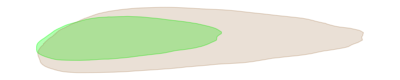

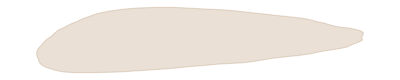

```mathematica
NICER=Show[{Graphics[{EdgeForm[Thick],Green,Opacity[0.3],Polygon[NCh1]}],Graphics[{EdgeForm[Thick],Brown,Opacity[0.2],Polygon[NCh2]}]}]
NICER2=Graphics[{EdgeForm[Thick],Brown,Opacity[0.2],Polygon[NCh2]}]
```

```mathematica
Max[sGw1[[All,1]]]
Max[Gw1[[All,1]]]
Max[sGw2[[All,1]]]
Max[Gw2[[All,1]]]
```

13.7527

13.4143

13.6928

13.3948

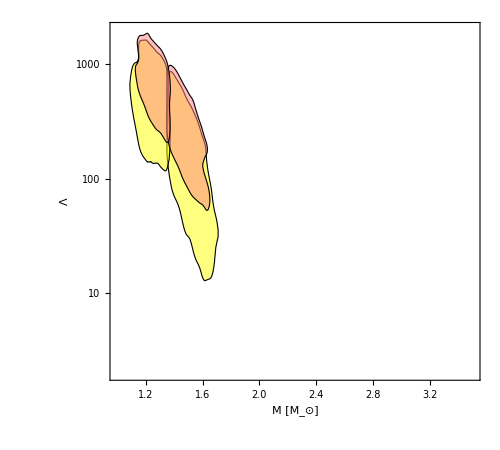

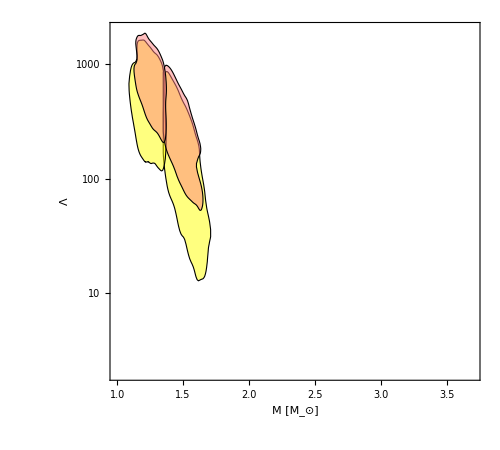

```mathematica
shade[gw1_,gw2_,ugw1_,ugw2_]:=Module[{pol1,pol2,pol3,pol4,out},

pol1={EdgeForm[Thick],Pink,Opacity[0.5],Polygon[gw1]};
pol2={EdgeForm[Thick],Pink,Opacity[0.5],Polygon[gw2]};
pol3={EdgeForm[Thick],Yellow,Opacity[0.5],Polygon[ugw1]};
pol4={EdgeForm[Thick],Yellow,Opacity[0.5],Polygon[ugw2]};
out=ListLogPlot[{{0,0}},PlotRange->{{1,3.5},{2,2*10^3}},Epilog->{(pol3/.{x_,y_?NumericQ}:>{x,Log[y]}),(pol4/.{x_,y_?NumericQ}:>{x,Log[y]}),(pol1/.{x_,y_?NumericQ}:>{x,Log[y]}),(pol2/.{x_,y_?NumericQ}:>{x,Log[y]})},AspectRatio->0.9,FrameLabel->{Style["M [M_⊙]",20],Style["Λ",20]},RotateLabel->False,ImageSize->500,Frame->True,Joined->True,LabelStyle->Directive[20]];


Return[out];

]
lamERR=shade[lamGw1,lamGw2,lamGwUni1,lamGwUni2]
shade[gw1_,gw2_,ugw1_,ugw2_]:=Module[{pol1,pol2,pol3,pol4,out},

pol1={EdgeForm[Thick],Pink,Opacity[0.5],Polygon[gw1]};
pol2={EdgeForm[Thick],Pink,Opacity[0.5],Polygon[gw2]};
pol3={EdgeForm[Thick],Yellow,Opacity[0.5],Polygon[ugw1]};
pol4={EdgeForm[Thick],Yellow,Opacity[0.5],Polygon[ugw2]};
out=ListLogPlot[{{0,0}},PlotRange->{{1,3.7},{2,2*10^3}},Epilog->{(pol3/.{x_,y_?NumericQ}:>{x,Log[y]}),(pol4/.{x_,y_?NumericQ}:>{x,Log[y]}),(pol1/.{x_,y_?NumericQ}:>{x,Log[y]}),(pol2/.{x_,y_?NumericQ}:>{x,Log[y]})},AspectRatio->0.9,FrameLabel->{Style["M [M_⊙]",20],Style["Λ",20]},RotateLabel->False,ImageSize->500,Frame->True,Joined->True,LabelStyle->Directive[20]];


Return[out];

]
lamERRwide=shade[lamGw1,lamGw2,lamGwUni1,lamGwUni2]
```

```mathematica
shade[gw1_,gw2_,NC1_,NC2_]:=Module[{pol1,pol2,pol3,pol4,out},

pol1=Polygon[gw1];
pol2=Polygon[gw2];
pol3=Polygon[NC1];
pol4=Polygon[NC2];
out=Show[{Plot[z/5,{z,0,2},PlotRange->{{5,15},{0,3}}],Graphics[{EdgeForm[Thick],Pink,Opacity[0.5],pol1}],Graphics[{EdgeForm[Thick],Pink,Opacity[0.5],pol2}],Graphics[{EdgeForm[Thick],Brown,Opacity[0.2],pol3}],NICER2}];


Return[out];

]
```

```mathematica
shade[gw1_,gw2_,sgw1_,sgw2_,NC1_,NC2_]:=Module[{pol1,pol2,spol1,spol2,pol3,pol4,out},

pol1=Polygon[gw1];
pol2=Polygon[gw2];
spol1=Polygon[sgw1];
spol2=Polygon[sgw2];
pol3=Polygon[NC1];
pol4=Polygon[NC2];
out=Show[{Plot[z/5,{z,0,2},PlotRange->{{5,15},{0,3}}],Graphics[{EdgeForm[Thick],Yellow,Opacity[0.5],spol1}],Graphics[{EdgeForm[Thick],Yellow,Opacity[0.5],spol2}],Graphics[{EdgeForm[Thick],Pink,Opacity[0.5],pol1}],Graphics[{EdgeForm[Thick],Pink,Opacity[0.5],pol2}],NICER2}];


Return[out];

]
```

```mathematica
shadeALL[gw1_,gw2_,sgw1_,sgw2_,NC1_,NC2_]:=Module[{pol1,pol2,pol4,spol1,spol2,pol3,out},

pol1=Polygon[gw1];
pol2=Polygon[gw2];
spol1=Polygon[sgw1];
spol2=Polygon[sgw2];
pol3=Polygon[NC1];
pol4=Polygon[NC2];
out=Show[{Plot[z/5,{z,0,2},PlotRange->{{5,15},{0,3}}],Graphics[{EdgeForm[Thick],Green,Opacity[0.3],pol4}],Graphics[{EdgeForm[Thick],Yellow,Opacity[0.5],spol1}],Graphics[{EdgeForm[Thick],Yellow,Opacity[0.5],spol2}],Graphics[{EdgeForm[Thick],Pink,Opacity[0.5],pol1}],Graphics[{EdgeForm[Thick],Pink,Opacity[0.5],pol2}],Graphics[{EdgeForm[Thick],Brown,Opacity[0.2],pol3}],NICER}];


Return[out];

]
```

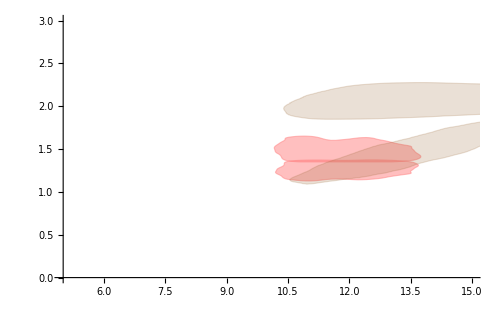

```mathematica
Ligoplot=shade[sGw1,sGw2,NC1,NC2]
```

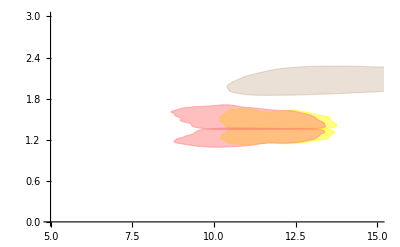

```mathematica
sLigoplot=shade[Gw1,Gw2,sGw1,sGw2,NC1,NC2]
```

#### Ligo/NICER plot

```mathematica
lines=Plot[{2.5+0.00001x,2.67+0.00001x},{x,0,30},PlotStyle->MyStyle[[{1,1,3,4,7}]],Filling->{1->{2}}];
lines2=Plot[{2.91-0.08+0.00001x,2.91+0.08+0.00001x},{x,0,30},PlotStyle->MyStyle[[{1,1,3,4,7}]],Filling->{1->{2}}];
```

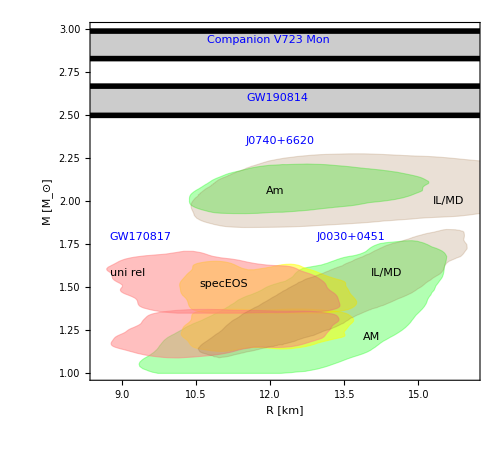

```mathematica
allcon=Show[{ListLinePlot[{0,0},AspectRatio->0.9,PlotRange->{{8.5,16.1},{1,3}},PlotStyle->MyStyle2[[klist]],FrameLabel->{Style["R [km]",20],Style["M [M_⊙]",20]},Joined->True,ImageSize->500,Frame->True,LabelStyle->Directive[20]],lines,lines2,shadeALL[Gw1,Gw2,sGw1,sGw2,NC1,NC2],txt["Am",0.45,0.53],txt["IL/MD",0.88,0.5],txtCL["J0740+6620",0.4,0.67],txtCL["Companion V723 Mon",0.3,0.95],txtCL["GW190814",0.4,0.79],txtCL["GW170817",0.05,0.4],txtCL["J0030+0451",0.58,0.4],txt["uni rel",0.05,0.3],txt["specEOS",0.28,0.27],txt["IL/MD",0.72,0.3],txt["AM",0.7,0.12]}](*Change color*)
(*Export["input_files/LVC_NICER/MRconstraints.pdf",allcon]*)
```

### EOS band

```mathematica
Clear[l1]
l1=Import["input_files/LVC_NICER/GW170817_logCnt[cgs]_logp5pc[cgs]_logp25pc[cgs]_logp75pc[cgs]_logp95pc[cgs].txt","Table"];
```

```mathematica
eosmin=Join[l1⟦All,{1,2}⟧,Reverse[l1⟦All,{1,5}⟧]];
eosmax=Join[l1⟦All,{1,3}⟧,Reverse[l1⟦All,{1,4}⟧]];
```

```mathematica
emin=Table[{10^eosmin[[i,1]],10^eosmin[[i,2]]},{i,Length[eosmin]}];
emax=Table[{10^eosmax[[i,1]],10^eosmax[[i,2]]},{i,Length[eosmax]}];
```

```mathematica
eosALL[min_,max_]:=Module[{pol1,pol2,pol4,spol1,spol2,pol3,out},

pol1=Polygon[min];


out=LogLogPlot[z/5,{z,0,2},PlotRange->{{10^14,2.5*10^15},{3*10^32,10^37}},AspectRatio->0.9,Epilog->{EdgeForm[Thick],Opacity[0.5],Yellow,(pol1/.{x_,y_?NumericQ}:>{Log[x],Log[y]})},FrameTicks->{{Automatic,Automatic},{{{10^14,Superscript[10,14]},{10^15,Superscript[10,15]}},Automatic}},FrameLabel->{Style["ε [g cm^-3]",20],Style["p [dyn cm^-3]",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]];


Return[out];

]
```

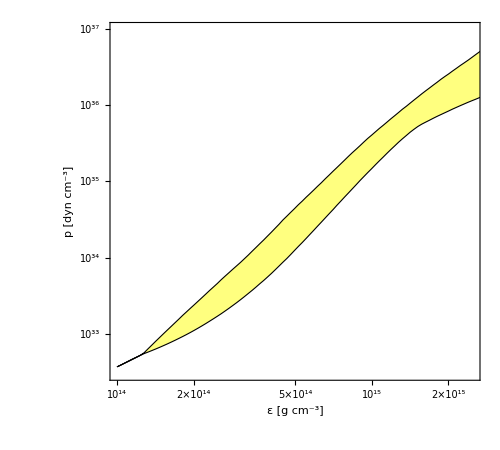

```mathematica
LIGO=eosALL[emin,emax]
```

## TOV Solver [Always run]

### Mass radius calc

```mathematica
dr=10^-7;
Rmax=10^20;
```

```mathematica
Clear[mr]
```

```mathematica
mr[p0_,en_]:=Module[{sol,f1,f2,rmax,mmax,minp,rlo,rhi,plo,phi},
Clear[M];
Clear[p];
minp=1.6906320566287588*10^-25;
sol=NDSolve[{p'[rr]==If[rr>dr,-(Gj*(M[rr] clight^2+4.π*rr^3 p[rr]))/(clight^4 rr^2)*(en[p[rr]] clight^2+p[rr])*(1-(2*Gj*M[rr])/(clight^2 rr))^-1,-(4π)/3. Gj/clight^4 rr*(en[p0]+p0)*(en[p0]+3p0)],M'[rr]==4π*rr^2 en[p[rr]] ,p[0]==p0,M[0]==0,WhenEvent[p[rr]≤minp,{R= rr,Mmax= M[rr],"StopIntegration"},"DetectionMethod"->"Interpolation"]},{p,M},{rr,0,20},Method->"StiffnessSwitching",WorkingPrecision->26];
f1[x_]:=M[x]/.sol[[1,2]];
f2[x_]:=p[x]/.sol[[1,1]];  
rmax=x/.FindRoot[f2[x]==0,{x,10}];
mmax=f1[rmax];

rlo=0.7*rmax;
rhi=0.1*rmax;
plo=f2[rlo];
phi=f2[rhi];

Return[{rmax,mmax,en[p0]/(scale*edconv),p0/(scale*edconv),en[plo]/(scale*edconv),en[phi]/(scale*edconv)}];

]
mre0[p0_,en_]:=Module[{sol,f1,f2,rmax,mmax},
Clear[M];
Clear[p];
sol=NDSolve[{p'[rr]==If[rr>dr,-(Gj*(M[rr] clight^2+4π*rr^3 p[rr]))/(clight^4 rr^2)*(en[p[rr]] clight^2+p[rr])*(1-(2*Gj*M[rr])/(clight^2 rr))^-1,-(4π)/3 Gj/clight^4 rr*(en[p0]+p0)*(en[p0]+3p0)],M'[rr]==4π*rr^2 en[p[rr]] ,p[0]==p0,M[0]==0,WhenEvent[p[rr]≤0,{R= rr,Mmax= M[rr],"StopIntegration"},"DetectionMethod"->"Interpolation"]},{p,M},{rr,0,20},Method->"StiffnessSwitching",AccuracyGoal->11,PrecisionGoal->10];
f1[x_]:=M[x]/.sol[[1,2]];
f2[x_]:=p[x]/.sol[[1,1]];
rmax=x/.FindRoot[f2[x]==0,{x,10}];
mmax=f1[rmax];
Return[{rmax,mmax,en[p0]/(scale*edconv),p0/(scale*edconv)}];

]
```

If you just want to get the mass-radius relationship, you just need to run genmr[enint]

```mathematica
p0list=Join[Table[x*10^-4,{x,0.01,1,0.01}],Table[x*10^-4,{x,1.1,15,0.1}],Table[x*10^-4,{x,101,1000,20}]];
p0twn=Join[Table[x*10^-4,{x,0.001,0.009,0.001}],Table[x*10^-4,{x,0.01,0.5,0.01}],Table[x*10^-4,{x,0.6,15,0.1}],Table[x*10^-4,{x,101,1000,10}],Table[x*10^-4,{x,1001,10000,100}]];
Length[p0list]
```

285

```mathematica
genmr[eos_]:=Select[Join[Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,0.01,1,0.01}]],Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,1.1,15,0.1}]],Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,101,1000,20}]]],#[[2]]>0&]
```

```mathematica
genmrTW[eos_]:=Select[Join[Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,0.001,0.009,0.001}]],Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,0.1,0.5,0.01}]],Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,0.5,1,0.0025}]],Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,1.1,15,0.1}]],Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,20,95,2.5}]]],#[[2]]>0&]
```

```mathematica
(*genmrTW[eos_]:=Select[Join[Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,0.1,1,0.01}]],Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,1,15,0.1}]],Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,20,95,2.5}]],Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,101,1000,10}]],Parallelize[Table[Quiet[mre0[x*10^-4,eos]],{x,1001,10000,100}]]],#[[2]]>0&]*)
```

```mathematica
genmrMORE[eos_]:=Select[Join[Parallelize[Table[Quiet[mre0[x*10^-4,eos]],{x,0.01,0.1,0.01}]],Parallelize[Table[Quiet[mre0[x*10^-4,eos]],{x,0.2,1,0.05}]],Parallelize[Table[Quiet[mre0[x*10^-4,eos]],{x,1,15,1.5}]],Parallelize[Table[Quiet[mre0[x*10^-4,eos]],{x,20,95,5}]],Parallelize[Table[Quiet[mre0[x*10^-4,eos]],{x,101,1000,20}]],Parallelize[Table[Quiet[mre0[x*10^-4,eos]],{x,1001,10000,100}]]],#[[2]]>0&]
```

```mathematica
(*function to add more low mass points*)
runlowM[path_,n_]:=Module[{in,out,eos,range,in2,mrtot,csp,mrout},
in=Import[StringJoin["output_files/",path,"/eos",ToString[n],".dat"]];
eos=ConvertInterpolate[in]; (* col2 energy, col3 pressure in MeV/fm3*)
range={0.009,0.01, 0.015,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09};
out=Table[mr[range[[i]]*10^-4,eos],{i,Length[range]}];
csp=Interpolation[in[[All,{2,1}]],InterpolationOrder->1];(*perssure vs. bayon density*)

Print[csp];
mrout=setcs[out,csp ]; (*addss baryon density to mass vs. r*)

in2=Import[StringJoin["output_files/",path,"/mr",ToString[n],".dat"]];
mrtot=Join[mrout,in2];
Export[StringJoin["output_files/",path,"/mr",ToString[n],".dat"],mrtot];
Return[out];
]
```

### ConvertToEOS

#### normal EOS reconstruct

```mathematica
EOSrecon[f_,ic_,dn_]:=Module[{e0,n0,p0,n,ee,p},
n0=ic[[1]];
e0=ic[[2]];
p0=ic[[3]];

n=n0+dn;
ee=e0+dn*(e0+p0)/n0;
p=p0+f[n0]*dn*(e0+p0)/n0;

Return[{n,ee,p}];
]
ConvertInterpolate[tabMeVfm3_]:=Module[{entab,enint},
entab=Table[{edconv*scale*tabMeVfm3[[i,2]],edconv*scale*tabMeVfm3[[i,3]]},{i,Length[tabMeVfm3]}]; (* table of energy density in terms of pressure *)
enint=Interpolation[entab,InterpolationOrder->1]; (*interpolation function, too high of order causes issues *)
Return[enint];
] 
comblowden[lowdenin_,frun_,rhosat_]:=Module[{enext,pnext,nc,ni,nn,lm,tlow,entab,alltab,en,Es,Ps,lowdensub,lowden,ttsub,ep,derv,erho,prho,murho, chi2,chi3,c2,c3,tabgcm3,ϵofp,pofϵ,tabMeVfm3},
erho=Interpolation[lowdenin[[All,{1,3}]],InterpolationOrder->1];
prho=Interpolation[lowdenin[[All,{1,2}]],InterpolationOrder->1];


Es=erho[rhosat];
Ps=prho[rhosat];

lowdensub=Select[lowdenin,#[[1]]<rhosat&]; (*rho/rho0 [fm^-3], pressure [MeV/fm^-3], energy density [MeV/fm^-3] *)
lowden=edconv*scale*lowdensub[[All,{3,2}]];
enext=Es;
pnext=Ps;
(*f[0]={0,0,0};
nc[1]=0;
ni=2;*)
ni=1;
For[nn=rhosat,nn≤50,nn=nn+0.005,
f[nn]=EOSrecon[frun,{nn,enext,pnext},0.005];

enext=f[nn][[2]];
pnext=f[nn][[3]];
nc[ni]=nn;
ni++;
];
(*FORMAT {{"n [fm^-3]","p [MeV/fm^3]","e [MeV/fm^3]","cs^2","muB [MeV]"}}*)
ttsub=Join[Table[{nsat*lowdensub[[i,1]],lowdensub[[i,2]],lowdensub[[i,3]],frun[lowdensub[[i,1]]],(lowdensub[[i,2]]+lowdensub[[i,3]])/(nsat*lowdensub[[i,1]])},{i,Length[lowdensub]}],Table[{nsat*nc[i],f[nc[i]][[3]],f[nc[i]][[2]],frun[nc[i]],(f[nc[i]][[3]]+f[nc[i]][[2]])/(nsat*nc[i])},{i,ni-1}]]; (* density,  pressure, energy density, cs2, muB *)



tabgcm3=Table[{gcm3toMeVfm3*ttsub[[i,2]],gcm3toMeVfm3*ttsub[[i,3]]},{i,2,Length[ttsub]}];
(* this table must be in the format  pressure [g/cm^3], energy density [g/cm^3] to use in the I Love Q below*)
(*EoS*)



(*EoSTable="eosAPR.dat";
{ϵofp,pofϵ}=InterpolatingEoS[tabgcm3,ChosenWorkingPrecision];*)

(*ep=Interpolation[Delete[ttsub[[All,{1,2}]],1]];

(*mu [fm-1], rho [fm^-3]*)
murho=Table[{ttsub[[i,5]]/197.3,ttsub[[i,1]]},{i,2,Length[ttsub]}];
chi2=dchi[murho];
chi3=dchi3[murho];
c2=ListLinePlot[chi2,ImageSize->500,PlotStyle->MyStyle,PlotRange->{{0.001,7},{0,0.1}},FrameLabel->{Style["n/n_sat",20],Style["χ_2/μ_B^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]];
c3=ListLinePlot[chi3,ImageSize->500,PlotStyle->MyStyle,PlotRange->{{0.001,7},{-2,2}},FrameLabel->{Style["n/n_sat",20],Style["χ_3/μ_B",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]];
Print[c2];
Print[c3];


entab=Table[{edconv*scale*f[nc[i]][[2]],edconv*scale*f[nc[i]][[3]]},{i,ni-1}]; (*pressure, energy density*)
alltab=Join[lowden,entab];
en=Interpolation[alltab[[All,{2,1}]],InterpolationOrder->1];

Return[en];*)
Return[ttsub];
]
```

## Style [Always run]

```mathematica
Needs["ErrorBarPlots`"]
thick=0.008;
MyStyle={
Directive[Thickness[thick],Black],
Directive[Thickness[thick],Red],(*"2bumpsfat"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Red],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Red],
Directive[Dashing[{0.01,0.01}],Red],
Directive[Thickness[thick],Blue],(*"endpoint"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Blue],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Blue],
Directive[Dashing[{0.01,0.01}],Blue],
Directive[Thickness[thick],Darker[Green]],(*"2bumpsthin"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Green]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Green]],
Directive[Dashing[{0.01,0.01}],Darker[Green]],
Directive[Thickness[thick],Cyan],(*"slanted"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Cyan],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Cyan],
Directive[Dashing[{0.01,0.01}],Cyan],
Directive[Thickness[thick],Magenta],(*"oscilliations"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Magenta],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Magenta],
Directive[Dashing[{0.01,0.01}],Magenta],
Directive[Thickness[thick],Orange],(*"adjustedwidth"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Orange],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Orange],
Directive[Dashing[{0.01,0.01}],Orange],
Directive[Thickness[thick],Orange],(*"peaklocation"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Orange],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Orange],
Directive[Dashing[{0.01,0.01}],Orange],
Directive[Thickness[thick],Darker[Green]],(*"endpoint_max"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Green]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Green]],
Directive[Dashing[{0.01,0.01}],Darker[Green]],
Directive[Thickness[thick],Brown],(*"peaklocation_adjustwidth"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Brown],Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Brown],
Directive[Dashing[{0.01,0.01}],Brown],
Directive[Thickness[thick],Darker[Gray]],(*"afterbump"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Gray]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Gray]],
Directive[Dashing[{0.01,0.01}],Darker[Gray]],
Directive[Thickness[thick],Darker[Green]],(*"endpoint_noslant"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Green]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Green]],
Directive[Dashing[{0.01,0.01}],Darker[Green]],
Directive[Thickness[thick],Pink],(*"endpoint2"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Pink],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Pink],
Directive[Dashing[{0.01,0.01}],Pink],
Directive[Thickness[thick],Black],
Directive[Thickness[thick],Darker[Red]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Red]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Red]],
Directive[Dashing[{0.01,0.01}],Darker[Red]],
Directive[Thickness[thick],Gray],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Gray],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Gray],
Directive[Dashing[{0.01,0.01}],Gray],
Directive[Thickness[thick],Darker[Green]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Green]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Green]],
Directive[Dashing[{0.01,0.01}],Darker[Green]],
Directive[Thickness[thick],Darker[Orange]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Orange]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Orange]],
Directive[Dashing[{0.01,0.01}],Darker[Orange]],
Directive[Thickness[thick],Darker[Purple]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Purple]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Purple]],
Directive[Dashing[{0.01,0.01}],Darker[Purple]],
Directive[Thickness[thick],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Brown]],
Directive[Dashing[{0.01,0.01}],Darker[Brown]],
Directive[Thickness[thick],Darker[Yellow]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Yellow]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Yellow]],
Directive[Dashing[{0.01,0.01}],Darker[Yellow]],
Directive[Thickness[thick],Darker[Magenta]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Magenta]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Magenta]],
Directive[Dashing[{0.01,0.01}],Darker[Magenta]],
Directive[Thickness[thick],Blue],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Blue],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Blue],
Directive[Dashing[{0.01,0.01}],Blue],
Directive[Thickness[thick],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Blue]],
Directive[Dashing[{0.01,0.01}],Darker[Blue]],Directive[Thickness[thick],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Brown]],
Directive[Dashing[{0.01,0.01}],Darker[Brown]],Directive[Thickness[thick],Gray],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Gray],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Gray],
Directive[Dashing[{0.01,0.01}],Gray],
Directive[Thickness[thick],Darker[Green]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Green]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Green]],
Directive[Dashing[{0.01,0.01}],Darker[Green]],
Directive[Thickness[thick],Darker[Orange]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Orange]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Orange]],
Directive[Dashing[{0.01,0.01}],Darker[Orange]],
Directive[Thickness[thick],Darker[Purple]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Purple]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Purple]],
Directive[Dashing[{0.01,0.01}],Darker[Purple]],
Directive[Thickness[thick],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Brown]],
Directive[Dashing[{0.01,0.01}],Darker[Brown]],
Directive[Thickness[thick],Darker[Yellow]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Yellow]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Yellow]],
Directive[Dashing[{0.01,0.01}],Darker[Yellow]],
Directive[Thickness[thick],Darker[Magenta]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Magenta]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Magenta]],
Directive[Dashing[{0.01,0.01}],Darker[Magenta]],
Directive[Thickness[thick],Blue],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Blue],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Blue],
Directive[Dashing[{0.01,0.01}],Blue],
Directive[Thickness[thick],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Blue]],
Directive[Dashing[{0.01,0.01}],Darker[Blue]],Directive[Thickness[thick],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Brown]],
Directive[Dashing[{0.01,0.01}],Darker[Brown]],Directive[Thickness[thick],Darker[Purple]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Purple]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Purple]],
Directive[Dashing[{0.01,0.01}],Darker[Purple]],
Directive[Thickness[thick],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Brown]],
Directive[Dashing[{0.01,0.01}],Darker[Brown]],
Directive[Thickness[thick],Darker[Yellow]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Yellow]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Yellow]],
Directive[Dashing[{0.01,0.01}],Darker[Yellow]],
Directive[Thickness[thick],Darker[Magenta]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Magenta]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Magenta]],
Directive[Dashing[{0.01,0.01}],Darker[Magenta]],
Directive[Thickness[thick],Blue],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Blue],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Blue],
Directive[Dashing[{0.01,0.01}],Blue],
Directive[Thickness[thick],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Blue]],
Directive[Dashing[{0.01,0.01}],Darker[Blue]],Directive[Thickness[thick],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Brown]],
Directive[Dashing[{0.01,0.01}],Darker[Brown]]};


MyStyle2={Directive[Thickness[thick],Black],
Directive[Thickness[thick],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.005,0.02}],Darker[Blue]],
Directive[Thickness[thick],Darker[Orange]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Orange]],
Directive[Thickness[thick],Darker[Green]],
Directive[Thickness[thick],Dashing[{0.01,0.01}],Darker[Green]],
Directive[Thickness[thick],Darker[Magenta]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Magenta]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Green],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Pink]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Pink],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Purple],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Blue],
Directive[Thickness[thick],Blue],
Directive[Thickness[thick],Red],
Directive[Thickness[thick],Green],
Directive[Thickness[thick],Brown],
Directive[Thickness[thick],Orange],
Directive[Thickness[thick],Purple],
Directive[Thickness[thick],Magenta],
Directive[Thickness[thick],Dashing[{0.005,0.02}],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Yellow]]};
MyStyle3={Directive[Thickness[thick],Black],
Directive[Thickness[thick],Dashing[{0.005,0.02}],Darker[Red]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Blue],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Yellow]],
Directive[Thickness[thick],Green],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Purple],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Brown]],
Directive[Thickness[thick],Darker[Orange]],
Directive[Thickness[thick],Darker[Purple]],
Directive[Thickness[thick],Darker[Magenta]],
Directive[Thickness[thick],Blue],
Directive[Thickness[thick],Red],
Directive[Thickness[thick],Green],
Directive[Thickness[thick],Brown],
Directive[Thickness[thick],Orange],
Directive[Thickness[thick],Purple],
Directive[Thickness[thick],Magenta],
Directive[Thickness[thick],Dashing[{0.005,0.02}],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Yellow]]};
txt[l_,x_,y_]:=Graphics[{FontSize->18,Text[l,Scaled[{x,y}],{-1,0}]}];
txtCL[l_,x_,y_]:=Graphics[{Blue,FontSize->18,Text[l,Scaled[{x,y}],{-1,0}]}];
txt[l_,x_,y_,siz_]:=Graphics[{FontSize->siz,Text[l,Scaled[{x,y}],{-1,0}]}];
txt25[l_,x_,y_]:=Graphics[{FontSize->25,Text[l,Scaled[{x,y}],{-1,0}]}];
ln1[horz_,vert_,st_]:=Graphics[{st[[1]],Line[{Scaled[{horz[[1]],vert[[1]]}],Scaled[{horz[[2]],vert[[1]]}]}]}];
txt1[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[1]],Scaled[{horz[[3]],vert[[1]]}],{-1,0}]}];
ln2[horz_,vert_,st_]:=Graphics[{st[[2]],Line[{Scaled[{horz[[1]],vert[[2]]}],Scaled[{horz[[2]],vert[[2]]}]}]}];
txt2[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[2]],Scaled[{horz[[3]],vert[[2]]}],{-1,0}]}];
ln3[horz_,vert_,st_]:=Graphics[{st[[3]],Line[{Scaled[{horz[[1]],vert[[3]]}],Scaled[{horz[[2]],vert[[3]]}]}]}];
txt3[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[3]],Scaled[{horz[[3]],vert[[3]]}],{-1,0}]}];
ln4[horz_,vert_,st_]:=Graphics[{st[[4]],Line[{Scaled[{horz[[1]],vert[[4]]}],Scaled[{horz[[2]],vert[[4]]}]}]}];
txt4[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[4]],Scaled[{horz[[3]],vert[[4]]}],{-1,0}]}];
ln5[horz_,vert_,st_]:=Graphics[{st[[5]],Line[{Scaled[{horz[[1]],vert[[5]]}],Scaled[{horz[[2]],vert[[5]]}]}]}];
txt5[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[5]],Scaled[{horz[[3]],vert[[5]]}],{-1,0}]}];
ln6[horz_,vert_,st_]:=Graphics[{st[[6]],Line[{Scaled[{horz[[1]],vert[[6]]}],Scaled[{horz[[2]],vert[[6]]}]}]}];
txt6[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[6]],Scaled[{horz[[3]],vert[[6]]}],{-1,0}]}];
ln7[horz_,vert_,st_]:=Graphics[{st[[7]],Line[{Scaled[{horz[[1]],vert[[7]]}],Scaled[{horz[[2]],vert[[7]]}]}]}];
txt7[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[7]],Scaled[{horz[[3]],vert[[7]]}],{-1,0}]}];

leg2[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert]];
leg3[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert],ln3[horz,vert,st],txt3[nm,horz,vert]];
leg3b[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert],ln4[horz,vert,st],txt4[nm,horz,vert]];
leg4[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert],ln3[horz,vert,st],txt3[nm,horz,vert],ln4[horz,vert,st],txt4[nm,horz,vert]];
leg5[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert],ln3[horz,vert,st],txt3[nm,horz,vert],ln4[horz,vert,st],txt4[nm,horz,vert],ln5[horz,vert,st],txt5[nm,horz,vert]];
leg5b[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln3[horz,vert,st],txt3[nm,horz,vert],ln4[horz,vert,st],txt4[nm,horz,vert],ln5[horz,vert,st],txt5[nm,horz,vert],ln6[horz,vert,st],txt6[nm,horz,vert]];
leg6[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert],ln3[horz,vert,st],txt3[nm,horz,vert],ln4[horz,vert,st],txt4[nm,horz,vert],ln5[horz,vert,st],txt5[nm,horz,vert],ln6[horz,vert,st],txt6[nm,horz,vert]];
leg7[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert],ln3[horz,vert,st],txt3[nm,horz,vert],ln4[horz,vert,st],txt4[nm,horz,vert],ln5[horz,vert,st],txt5[nm,horz,vert],ln6[horz,vert,st],txt6[nm,horz,vert],ln7[horz,vert,st],txt7[nm,horz,vert]];

lab[labi_]:=Join[{"PHENIX all^+"},labi];
lablhc[labi_]:=Join[{"CMS all^+"},labi];
```

```mathematica
txt1t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[1]],Scaled[{horz[[3]],vert[[1]]}],{-1,0}]}];
txt2t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[2]],Scaled[{horz[[3]],vert[[2]]}],{-1,0}]}];
txt3t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[3]],Scaled[{horz[[3]],vert[[3]]}],{-1,0}]}];
txt4t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[4]],Scaled[{horz[[3]],vert[[4]]}],{-1,0}]}];
txt5t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[5]],Scaled[{horz[[3]],vert[[5]]}],{-1,0}]}];
txt6t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[6]],Scaled[{horz[[3]],vert[[6]]}],{-1,0}]}];
txt7t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[7]],Scaled[{horz[[3]],vert[[7]]}],{-1,0}]}];

leg2t[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert]];
leg3t[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert],ln3[horz,vert,st],txt3t[nm,horz,vert]];
leg3bt[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert],ln4[horz,vert,st],txt4t[nm,horz,vert]];
leg4t[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert],ln3[horz,vert,st],txt3t[nm,horz,vert],ln4[horz,vert,st],txt4t[nm,horz,vert]];
leg5t[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert],ln3[horz,vert,st],txt3t[nm,horz,vert],ln4[horz,vert,st],txt4t[nm,horz,vert],ln5[horz,vert,st],txt5t[nm,horz,vert]];
leg5bt[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln3[horz,vert,st],txt3t[nm,horz,vert],ln4[horz,vert,st],txt4t[nm,horz,vert],ln5[horz,vert,st],txt5t[nm,horz,vert],ln6[horz,vert,st],txt6t[nm,horz,vert]];
leg6t[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert],ln3[horz,vert,st],txt3t[nm,horz,vert],ln4[horz,vert,st],txt4t[nm,horz,vert],ln5[horz,vert,st],txt5t[nm,horz,vert],ln6[horz,vert,st],txt6t[nm,horz,vert]];
leg7t[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert],ln3[horz,vert,st],txt3t[nm,horz,vert],ln4[horz,vert,st],txt4t[nm,horz,vert],ln5[horz,vert,st],txt5t[nm,horz,vert],ln6[horz,vert,st],txt6t[nm,horz,vert],ln7[horz,vert,st],txt7t[nm,horz,vert]];
```

```mathematica
lb1[horz_,vert_,st_]:=Graphics[{EdgeForm[Thick],st,Rectangle[Scaled[{horz[[1]],vert-0.04}],Scaled[{horz[[2]],vert+0.04}]]}];
tb1[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm,Scaled[{horz[[3]],vert}],{-1,0}]}];
legbox[nm_,horz_,vert_,st_]:=Show[lb1[horz,vert,st],tb1[nm,horz,vert]];
```

```mathematica
hashbox[h1_,h2_,v1_,v2_,st_]:=RegionPlot[Rectangle[{h1,v1},{h2,v2}],Mesh->10,MeshFunctions->{(0.005) #1-#2&},BoundaryStyle->Directive[Darker[Red],Thick],MeshStyle->Thickness[.005]]
```

## Functions needed for plotting cs2, organizing etc [Always run]

```mathematica
pcen=p0list/(edconv*scale);
```

```mathematica
(*fname={"2bumpsfat","endpoint","2bumpsthin","slanted","oscilliations","adjustedwidth","peaklocation","endpoint_max","peaklocation_adjustwidth","afterbump","endpoint2","flatpeak"};*)
```

```mathematica
fname={"2bumpsfat","endpoint","2bumpsthin","slanted","oscilliations","adjustedwidth","peaklocation","endpoint_max","peaklocation_adjustwidth","afterbump","endpoint_noslant"};
```

```mathematica
readin[folder_]:=Module[{eos,mr},
eos=ToExpression[Table[Import[StringJoin["output_files/",folder,"/eos",ToString[i],".dat"]],{i,1,4}]];
mr=Table[Import[StringJoin["output_files/",folder,"/mr",ToString[i],".dat"]],{i,1,4}];
Return[{eos,mr}];
]
readin2[folder_]:=Module[{eos,mr},
eos=ToExpression[Table[Import[StringJoin["output_files/",folder,"/eos",ToString[i],".dat"]],{i,1,4}]];
mr=Table[Select[Import[StringJoin["output_files/",folder,"/mr",ToString[i],".dat"]],#[[7]]<13&],{i,1,4}];
Return[{eos,mr}];
]
```

```mathematica
mcut[mr_]:=Module[{MM,pos,mfind},
MM=Max[mr[[All,2]]];

mfind=0;
For[i=1,i≤Length[mr],i++,
mfind=If[mr[[i,2]]>mfind,mr[[i,2]],Break[]];
];
MM=mfind;

pos=Position[mr[[All,2]],MM][[1,1]];
Return[Select[mr[[1;;pos]],#[[2]]>0.3&]];
]
mcuthi[mr_]:=Module[{MM,pos,mfind},
MM=Max[Select[mr[[All,2]],4>#>2.4&]];

(*mfind=0;
For[i=1,i≤Length[mr],i++,
mfind=If[mr[[i,2]]>mfind,mr[[i,2]],Break[]];
];
MM=mfind;*)

pos=Position[mr[[All,2]],MM][[1,1]];
Return[Select[mr[[1;;pos]],#[[2]]>0.3&]];
]
```

```mathematica
mcut2[mr_]:=Module[{MM,pos},
MM=Table[{mr[[i,1]],If[mr[[i+1,2]]>mr[[i,2]],mr[[i,2]],0]},{i,1,Length[mr]-1}];
Return[Select[MM,#[[2]]>0.3&]];
]
```

```mathematica
last[list_]:=list[[Length[list]]]
rck[in_]:=Module[{mrl,mr1,mr2,rad1,rad2,ok},
mrl=Select[in,0.52<#[[2]]<2.5&];
mr1=Select[mrl,GW17m1[[1]]≤#[[2]]≤GW17m1[[2]] &];
mr2=Select[mrl,GW17m2[[1]]≤#[[2]]≤GW17m2[[2]] &];
rad1=Select[mr1,GW17R1[[1]]≤#[[1]]≤GW17R1[[2]] &];
rad2=Select[mr2,GW17R2[[1]]≤#[[1]]≤GW17R2[[2]] &];
ok=If[Length[rad1]>0&&Length[rad2]>0,1,0];
Return[ok];
]
```

```mathematica
fname
```

{2bumpsfat,endpoint,2bumpsthin,slanted,oscilliations,adjustedwidth,peaklocation,endpoint_max,peaklocation_adjustwidth,afterbump,endpoint_noslant}

```mathematica
tr=Table[QuotientRemainder[klist[[i]]-2,4],{i,Length[klist]}]
Table[{fname[[tr[[i,1]]+1]],tr[[i,2]]+1},{i,Length[tr]}]
```

{}

{}

```mathematica
(*mrck=Import["~/Dropbox/neutronStars/TOV_public/endpoint/mr2.dat"];
rck[mrck]*)
```

```mathematica
readall[]:=Module[{all,eosall,mrall,mout,keep,Rrange,klist,mfin,eosfin},
all=Join[Table[readin[fname[[i]]],{i,Length[fname]}]];
eosall=Flatten[all[[All,1]],1];
mrall=Flatten[all[[All,2]],1];

mout=Table[mcut[mrall[[i]]],{i,Length[mrall]}];
keep=Select[Table[Flatten[{i,last[mout[[i]]],rck[mout[[i]]]}],{i,Length[mout]}],#[[3]]>2.5&&#[[6]]>0&];

Print[keep[[All,{1,6}]]];


Rrange=keep[[All,2]];
klist=keep[[All,1]];
mfin=mout[[klist]];
eosfin=eosall[[klist]];
Return[{Rrange,mfin,eosfin,keep[[All,1]]+1}];
]
{Rran,Mfin,eosfin,klist}=readall[];
csprint[eos_]:=Table[Transpose[{eos[[i,All,1]]/nsat,eos[[i,All,4]]}],{i,Length[eos]}]
cssum=csprint[eosfin];
```

Import::nffil: File output_files/2bumpsfat/eos1.dat not found during Import.

Import::nffil: File output_files/2bumpsfat/eos2.dat not found during Import.

Import::nffil: File output_files/2bumpsfat/eos3.dat not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 1 of {} does not exist.

Part::span: 1;;{}⟦1,1⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::span: 1;;{}⟦1,1⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::span: 1;;{}⟦1,1⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

{}

```mathematica
Min[Rran]
Max[Rran]
```

∞

-∞

```mathematica
1/gcm3toMeVfm3
1/(1.6022*10^33)
```

5.60947×10^-13

6.24142×10^-34

```mathematica
stupidunits[sly_,eosall_]:=Module[{out,sout,plots,len,sub},
len=Length[eosall];
sub[eossub_]:=Table[{gcm3toMeVfm3*eossub[[i,3]],1.6022*10^33*eossub[[i,2]]},{i,Length[eossub]}];
out=Table[sub[eosall[[j]]],{j,len}];
sout=Table[{gcm3toMeVfm3*sly[[i,3]],1.6022*10^33*sly[[i,2]]},{i,Length[sly]}];
plots=Show[{ListLogLogPlot[Join[{sout},out],PlotRange->{{2*10^14,2.5*10^15},{10^33,5*10^36}},AspectRatio->0.9,PlotStyle->MyStyle2[[Flatten[{1,klist}]]],FrameLabel->{Style["ε [g cm^-3]",20],Style["p [dyn cm^-3]",20]},ImageSize->500,Frame->True,Joined->True,LabelStyle->Directive[15]],LIGO[],leg2[{"SLy","GW170817 + GW190814","f2","f3","f4"},{0,0.10,0.12}+0.4,{0.3,0.2},MyStyle],txt["50% credible contour",0.52,0.15]}];
Return[plots];
]

MRmany[eosall_]:=Module[{mrall,plots,len,sub,lines},
mrall=eosall[[All,All,1;;2]] ;
lines=Plot[{2.5+0.00001x,2.67+0.00001x},{x,0,30},PlotStyle->MyStyle[[{1,2}]],Filling->{1->{2}}];
plots=Show[{ListPlot[mrall,AspectRatio->0.9,PlotRange->{{10,14.5},{0.3,3.1}},PlotStyle->MyStyle2[[2;;8]],FrameLabel->{Style["R [km]",20],Style["M [M_⊙]",20]},ImageSize->500,Frame->True,Joined->True,LabelStyle->Directive[15]],lines,txt["GW190814",0.05,0.815],txt["GW170817",0.03,0.33],txt["J0030+0451",0.68,0.4],Ligoplot,leg4[{"f1","f2","f3","f4"},{0,0.10,0.12}+0.05,{0.5,1.4,0.3,0.2,0.1}+0.4,MyStyle[[2;;8]]]}];
Return[plots];
]

csplottab[dat_]:=Module[{psly,lines,tab,out},
psly=ListLogLinearPlot[dat,PlotStyle->MyStyle2[[Flatten[{1,klist}]]],PlotRange->{{1.8,4},{0,1.1}},Joined->True,AspectRatio->0.9,FrameLabel->{Style["n_B/n_sat",20],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]];
lines=LogLinearPlot[{1/3+0.00001x,1+0.00001x},{x,0.001,10},PlotStyle->MyStyle[[{1,1,2,3,4,5,6}]],PlotRange->{{1.7,4},{0,1.1}},AspectRatio->0.9,FrameLabel->{Style["n_B/n_sat",20],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]];

out=Show[Flatten[{lines,psly,txt["ε=3p",0.02,0.34],txt["causal limit",0.02,0.95]}]];
Return[out];
]
```

```mathematica
csplotvar[dat_,ff_]:=Module[{psly,lines,tab,out},
psly=ListLinePlot[dat,PlotStyle->MyStyle[[1]],PlotRange->{{0,9},{0,1.2}},AspectRatio->0.9,FrameLabel->{Style["n/n_sat",15],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]];
lines=Plot[{1/3+0.00001x,1+0.00001x},{x,0,10},PlotStyle->MyStyle[[{1,1,2,3,4,5,6}]]];
tab=Table[Plot[ff[[i]][x],{x,0,10},PlotStyle->MyStyle2[[i+1]],PlotRange->All],{i,Length[ff]}];
out=Show[Flatten[{psly,tab,lines,txt["ε=3p",0.05,0.3],txt["speed of light",0.1,0.8]}]];
Return[out];
]
csplotvar20[dat_,ff_]:=Module[{psly,lines,tab,out},
psly=ListLinePlot[dat,PlotStyle->MyStyle[[1]],PlotRange->{{0,25},{0,1.2}},AspectRatio->0.9,FrameLabel->{Style["n/n_sat",15],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]];
lines=Plot[{1/3+0.00001x,1+0.00001x},{x,0,25},PlotStyle->MyStyle[[{1,1,2,3,4,5,6}]]];
tab=Table[Plot[ff[[i]][x],{x,0,25},PlotStyle->MyStyle2[[i+1]],PlotRange->All],{i,Length[ff]}];
out=Show[Flatten[{psly,tab,lines,txt["ε=3p",0.05,0.3],txt["speed of light",0.1,0.8]}]];
Return[out];
]
```

```mathematica
csplot[dat_,ff_]:=Show[{ListLinePlot[dat,PlotStyle->MyStyle[[1]],PlotRange->{{0,9},{0,1.2}},AspectRatio->0.9,FrameLabel->{Style["n/n_sat",15],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]],Plot[{1/3+0.00001x,1+0.00001x,ff[x]},{x,0,10},PlotStyle->MyStyle2[[{1,1,2,3,4,5,6}]]],txt["ε=3p",0.05,0.3],txt["speed of light",0.1,0.8],leg2[{"sly","f1"},{0,0.10,0.12}+0.7,{0.4,0.3,0.2,0.1}-0.2,MyStyle]}]
csplot[dat_,ff_,ff1_]:=Show[{ListLinePlot[dat,PlotStyle->MyStyle[[1]],PlotRange->{{0,9},{0,1.2}},AspectRatio->0.9,FrameLabel->{Style["n/n_sat",15],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]],Plot[{1/3+0.00001x,1+0.00001x,ff[x],ff1[x]},{x,0,10},PlotStyle->MyStyle2[[{1,1,2,3,4,5,6}]]],txt["ε=3p",0.05,0.3],txt["speed of light",0.1,0.8],leg3[{"sly","f1","f2"},{0,0.10,0.12}+0.7,{0.4,0.3,0.2,0.1}-0.2,MyStyle]}]
csplot[dat_,ff_,ff1_,ff2_]:=Show[{ListLinePlot[dat,PlotStyle->MyStyle[[1]],PlotRange->{{0,9},{0,1.2}},AspectRatio->0.9,FrameLabel->{Style["n/n_sat",15],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]],Plot[{1/3+0.00001x,1+0.00001x,ff[x],ff1[x],ff2[x]},{x,0,10},PlotStyle->MyStyle2[[{1,1,2,3,4,5,6}]]],txt["ε=3p",0.05,0.3],txt["speed of light",0.1,0.8],leg4[{"sly","f1","f2","f3"},{0,0.10,0.12}+0.7,{0.4,0.3,0.2,0.1}-0.2,MyStyle]}]
csplot[dat_,ff_,ff1_,ff2_,ff3_]:=Show[{ListLinePlot[dat,PlotStyle->MyStyle[[1]],PlotRange->{{0,9},{0,1.2}},AspectRatio->0.9,FrameLabel->{Style["n/n_sat",15],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]],Plot[{1/3+0.00001x,1+0.00001x,ff[x],ff1[x],ff2[x],ff3[x]},{x,0,10},PlotStyle->MyStyle2[[{1,1,2,3,4,5,6}]]],txt["ε=3p",0.05,0.3],txt["speed of light",0.1,0.8],leg5[{"sly","f1","f2","f3","f4"},{0,0.10,0.12}+0.8,{0.5,0.4,0.3,0.2,0.1}+0.25,MyStyle]}]
```

```mathematica
disjump[cs2nint_,b_,cmax_,ns_,mag_,width_,off_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,fout,m,bb,x1,x2,y1,y2,mb,bbb,x1b,x2b,y1b,y2b},

fun[x_]:=1/3.-mag*Exp[-(x-off)^2/width^2];
y1=cs2nint[ns[[1]]];
y2=cmax[[2]];
x1=ns[[1]];
x2=ns[[1]]+0.1;
m=(y2-y1)/(x2-x1);
bb=y2-m*x2;

y1b=y2;
y2b=fun[ns[[2]]];
x1b=x2;
x2b=ns[[2]];
mb=(y2b-y1b)/(x2b-x1b);
bbb=y2b-mb*x2b;
c2[x_]:=Which[x<ns[[1]],cs2nint[x],ns[[1]]≤ x≤ ns[[1]]+0.1,m*x+bb,ns[[1]]+0.1≤ x≤ ns[[2]],mb*x+bbb,x> ns[[2]],fun[x]];
Return[c2];
]
```

```mathematica
s[x_,a_,b_]:=0.5+0.5 Tanh[(x-a)/b]
fun[x_,mag_,width_,off_]:=1/3.-mag*Exp[-(x-off)^2/width^2]

cslist[ff_]:=Show[{ListLinePlot[ff,PlotStyle->MyStyle,PlotRange->{{0,6},{0,1.2}},AspectRatio->0.9,FrameLabel->{Style["n/n_sat",15],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]],Plot[{1/3+0.00001x,1+0.00001x},{x,0,10},PlotStyle->MyStyle[[{1,1,2,3,4}]]],txt["ε=3p",0.05,0.3],txt["speed of light",0.1,0.8]}]
```

```mathematica
runbump1[cs2nint_,b_,cmax_,ns_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,name},
c1[x_]:=s[x,ns,b] cmax+(1-s[x,ns,b])*cs2nint[x];
Return[c1];
]

runbump2[cs2nint_,b_,cmax_,ns_,mag_,width_,off_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name},
c1[x_]:=s[x,ns[[1]],b[[1]]] cmax[[1]]+(1-s[x,ns[[1]],b[[1]]])*cs2nint[x];
fun[x_]:=1/3.-mag*Exp[-(x-off)^2/width^2];
c2[x_]:=s[x,ns[[2]],b[[2]]]*fun[x]+(1-s[x,ns[[2]],b[[2]]])*c1[x];
Return[c2];
]
```

```mathematica
fff[x_]:=Exp[-x]+0.1
Solve[fff[x]==B,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-1. Log[-0.1+B]}}

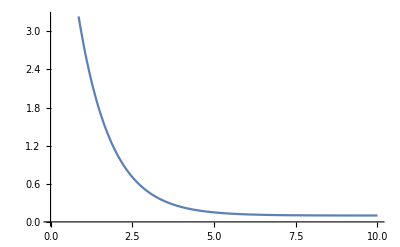

```mathematica
Plot[Exp[-(x-2)]+0.1,{x,0,10}]
```

```mathematica
bumpswitch[cs2nint_,b_,cmax_,ns_,mag_,width_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,dec,B},
(*start with sly, cs2nint,  then Gaussian, then exponential -> cmax*)

(*ns[[1]] ->  start bump
ns[[2]] -> downward after bump
*)
fun[x_]:=cs2nint[ns[[1]]]+mag[[1]]*Exp[-(x-ns[[2]])^2/width^2];
dec[x_]:=cmax+mag[[2]]*Exp[-(x-B)];

B=ns[[2]] -Log[(c1[ns[[2]]]+cmax)/mag[[2]]]  ;
c1[x_]:=s[x,ns[[1]],b]* fun[x]+(1-s[x,ns[[1]],b])*cs2nint[x];
(*c2[x_]:=s[x,ns[[2]],b[[2]]]*fun[x]+(1-s[x,ns[[2]],b[[2]]])*c1[x];*)
c2[x_]:=Which[x<ns[[2]],c1[x],x> ns[[2]],dec[x]];
Return[c2];
]
```

```mathematica
fx[f1_,f2_,ns_]:=Module[{p1,p2,x0,y0,f},
p1={ns[[1]],f1[ns[[1]]]};
p2={ns[[2]],f2[ns[[2]]]};

x0=(p2[[2]]-p1[[2]]+(p1[[1]]^2-p2[[1]]^2))/(2.(p1[[1]]-p2[[1]]));
y0=p2[[2]]-(p2[[1]]-x0)^2;

f[x_]:=(x-x0)^2+y0;
Return[f];
]
```

```mathematica
runosc[cs2nint_,b_,ns_,cmax_,mag_,width_,off_,freq_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,name,osc},
osc[x_]:=mag*Exp[(-b[[2]]*x)/(2width)]Cos[freq*x+off]+cmax;
c1[x_]:=s[x,ns,b[[1]]] osc[x]+(1-s[x,ns,b[[1]]])*cs2nint[x];

Return[c1];
]
```

```mathematica
disbump1[cs2nint_,b_,cmax_,ns_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,name},
c1[x_]:=If[x<ns,cs2nint[x], cmax];
Return[c1];
]

disbump2[cs2nint_,ns_,mag_,width_,off_]:=Module[{c2,out,fun,fout},

fun[x_]:=1/3.-mag*Exp[-(x-off)^2/width^2];
fout=fx[cs2nint,fun,ns];
c2[x_]:=Which[x<ns[[1]],cs2nint[x],ns[[1]]≤ x≤ ns[[2]],fout[x],x> ns[[2]],fun[x]];
Return[c2];
]
```

```mathematica
runoscbump[cs2nint_,b_,ns_,cmax_,mag_,width_,off_,freq_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,name,osc},
osc[x_]:=mag[[2]]*Exp[(-b[[3]]*x)/(2width[[2]])]Cos[freq*x+off[[2]]]+cmax[[2]];
c1[x_]:=s[x,ns[[1]],b[[1]]] (fun[x,mag[[1]],width[[1]],off[[1]]]+cmax[[1]])+(1-s[x,ns[[1]],b[[1]]])*cs2nint[x];
c2[x_]:=s[x,ns[[2]],b[[2]]]*osc[x]+(1-s[x,ns[[2]],b[[2]]])*c1[x];
Return[c2];
]
```

```mathematica
cp1=disbump1[cs2low,0.5,1./3,4]
cp2=disbump2[cs2low,{4,5},-0.3,0.2,6]
cp3=disjump[cs2low,{0.5,0.2},{0.5,0.7},{4,4.2},-0.5,0.1,4.5]
```

c1$610039

c2$610040

c2$610042

```mathematica
cs2EOS[f_,sly_,swt_]:=Module[{in,tabgcm3,ϵofp,pofϵ,out,dpde,plot,eosall,noout,eosmr,eosin,suot},
eosall=comblowden[sly,f,swt];
Print["eos done"];

(*out=Table[{sly[[i,1]],sly[[i,4]]},{i,Length[sly]}];
Print[csplot[out,f]];*)

(*out=Table[{gcm3toMeVfm3*eosall[[i,3]],1.6022*10^33*eosall[[i,2]]},{i,Length[eosall]}];
sout=Table[{gcm3toMeVfm3*sly[[i,3]],1.6022*10^33*sly[[i,2]]},{i,Length[sly]}];
Print[Show[{ListLogLogPlot[{sout,out},PlotRange->{{10^14,10^16},{10^32,10^37}},AspectRatio->0.9,PlotStyle->MyStyle,FrameLabel->{Style["ε [g cm^-3]",15],Style["p [dyn cm^-3]",20]},ImageSize->500,Frame->True,Joined->True,LabelStyle->Directive[15]],leg2[{"sly","function"},{0,0.10,0.12}+0.7,{0.4,0.3,0.2,0.1}-0.2,MyStyle]}]];*)

eosin=ConvertInterpolate[eosall];
noout=Select[genmr[eosin],#[[2]]<4&];

(*plot=ListLinePlot[noout[[All,1;;2]],PlotStyle->MyStyle,AspectRatio->0.9,PlotStyle->MyStyle,FrameLabel->{Style["R [km]",15],Style["M",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]];*)

Return[{noout,eosall}];
]
```

```mathematica
mrTWout[f_,sly_,swt_]:=Module[{in,tabgcm3,ϵofp,pofϵ,out,dpde,plot,eosall,noout,eosmr,eosin,suot},
eosall=comblowden[sly,f,swt];

eosin=ConvertInterpolate[eosall];
noout=Select[genmrTW[eosin],#[[2]]<4&];

Return[{noout,eosall}];
]
```

```mathematica
wraper[folder_,funs_]:=Module[{all,mrall,eosall,csplot,suplot,mrplot,csp,mrout},
CreateDirectory[StringJoin["output_files/",folder]];
all=Table[cs2EOS[funs[[i]],sly,0.8],{i,Length[funs]}];

Print["here"];
mrall=all[[All,1]];
eosall=all[[All,2]];

(*csp=Table[Interpolation[Select[eosall[[i,All,{2,1}]],#[[2]]>0.01&],InterpolationOrder->1],{i,4}];(*perssure vs. bayon density*)
mrout=Table[setcs[mrall[[i,1;;4]],csp[[i]],mrall[[i,5;;6]]],{i,Length[mrall]}]; (*addss baryon density to mass vs. r*)*)

csplot=csplotvar[cs2sly,funs];
suplot=stupidunits[sly,eosall];
mrplot=MRmany[mrsly,mrall];
SetDirectory[NotebookDirectory[]];

Export[StringJoin["output_files/",folder,"/cs2plot.png"],csplot];
Export[StringJoin["output_files/",folder,"/stupidunitsplot.png"],suplot];
Export[StringJoin["output_files/",folder,"/mrplot.png"],mrplot];
For[i=1,i≤Length[funs],i++,
Export[StringJoin["output_files/",folder,"/eos",ToString[i],".dat"],eosall[[i]]];
Export[StringJoin["output_files/",folder,"/mr",ToString[i],".dat"],mrall[[i]]];
]
]
```

```mathematica
(*FORMAT {{"n [fm^-3]","p [MeV/fm^3]","e [MeV/fm^3]","cs^2","muB [MeV]"}}*)
```

```mathematica
setcs[mr_,cs_]:=Table[Flatten[{mr[[i]],cs[mr[[i,4]]]/nsat}],{i,Length[mr]}] (*add nb/nsat to end of mr file*)
setcs[mra_,cs_,mrb_]:=Table[Flatten[{mra[[i]],cs[mr[[i,4]]]/nsat,mrb[[i]]}],{i,Length[mra]}] (*add nb/nsat to end of mr file*)
```

```mathematica
wraperTW[folder_,funs_]:=Module[{all,mrall,eosall,csplot,suplot,mrplot,csp,mrout},
CreateDirectory[StringJoin["output_files/",folder]];
all=Monitor[Table[mrTWout[funs[[i]],sly,0.8],{i,Length[funs]}],i];
Print["here"];
mrall=all[[All,1]];
eosall=all[[All,2]];

csp=Table[Interpolation[eosall[[i,All,{2,1}]],InterpolationOrder->1],{i,4}];(*perssure vs. bayon density*)
mrout=Table[setcs[mrall[[i]],csp[[i]]],{i,Length[mrall]}]; (*addss baryon density to mass vs. r*)

csplot=csplotvar[cs2sly,funs];
suplot=stupidunits[sly,eosall];
mrplot=MRmany[mrall];
SetDirectory[NotebookDirectory[]];
Print[mrplot];
Export[StringJoin["output_files/",folder,"/cs2plot.png"],csplot];
Export[StringJoin["output_files/",folder,"/stupidunitsplot.png"],suplot];
Export[StringJoin["output_files/",folder,"/mrplot.png"],mrplot];
For[i=1,i≤Length[funs],i++,
Export[StringJoin["output_files/",folder,"/eos",ToString[i],".dat"],eosall[[i]]];
Export[StringJoin["output_files/",folder,"/mr",ToString[i],".dat"],mrout[[i]]];
];

]
```

## Swamping out crusts [Always run]

### SLY [default]

```mathematica
sly=Import["input_files/sly/eos.dat"];
mrsly=Import["input_files/sly/mr.dat"];
cs2sly=Table[{sly[[i,1]],sly[[i,4]]},{i,Length[sly]}];
cs2low=Interpolation[cs2sly,InterpolationOrder->1];
```

```mathematica
cs2low[0.15]
```

0.00385773

## c_s^2 functional forms [run individually ONLY and as needed!]

### width of peak

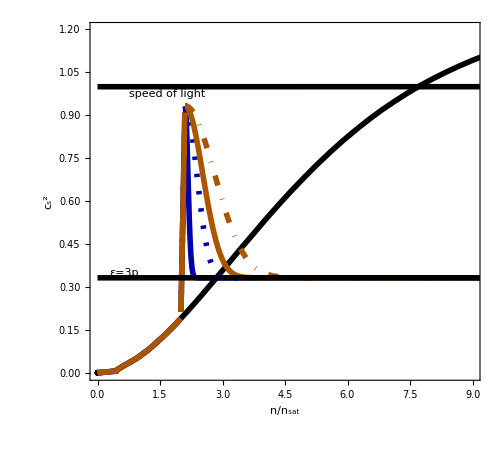

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/adjustedwidth already exists.

General::munfl: Exp[-710.222] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-712.89] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-715.562] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

eos done

$Aborted

```mathematica
f0=disbump2[cs2low,{2.0,2.1},-0.6,0.1,2.1];
f1=disbump2[cs2low,{2.0,2.1},-0.6,0.4,2.1];
f2=disbump2[cs2low,{2.0,2.1},-0.6,0.6,2.1];
f3=disbump2[cs2low,{2.0,2.1},-0.6,1,2.1];
csplotvar[cs2low,{f0,f1,f2,f3}]
wraper["adjustedwidth",{f0,f1,f2,f3}]
```

### location of peak

```mathematica
f0=disbump2[cs2low,{1.5,1.6},-0.6,1,1.6];
f1=disbump2[cs2low,{2.0,2.1},-0.6,1,2.1];
f2=disbump2[cs2low,{2.4,2.5},-0.6,1,2.5];
f3=disbump2[cs2low,{3.0,3.1},-0.6,1,3.1];
```

```mathematica
wraper["peaklocation",{f0,f1,f2,f3}]
```

wraper[peaklocation,{disbump2[InterpolatingFunction[…],{1.5,1.6},-0.6,1,1.6],disbump2[InterpolatingFunction[…],{2.,2.1},-0.6,1,2.1],disbump2[InterpolatingFunction[…],{2.4,2.5},-0.6,1,2.5],disbump2[InterpolatingFunction[…],{3.,3.1},-0.6,1,3.1]}]

```mathematica
csplot[cs2low,f0,f1,f2,f3]
stupidunits[sly,{f0eos,f1eos,f2eos,f3eos}]
MRmany[mrsly,{f0mr,f1mr,f2mr,f3mr}]
```

csplot[InterpolatingFunction[…],disbump2[InterpolatingFunction[…],{1.5,1.6},-0.6,1,1.6],disbump2[InterpolatingFunction[…],{2.,2.1},-0.6,1,2.1],disbump2[InterpolatingFunction[…],{2.4,2.5},-0.6,1,2.5],disbump2[InterpolatingFunction[…],{3.,3.1},-0.6,1,3.1]]

stupidunits[{{4.91649×10^-14,1.88644×10^-19,7.37866×10^-12,0.000753254},{1.55473×10^-13,1.20285×10^-18,2.33334×10^-11,0.000753254},{4.91649×10^-13,7.66973×10^-18,7.37866×10^-11,0.000753254},{1.55473×10^-12,4.89045×10^-17,2.33334×10^-10,0.000753254},{4.91649×10^-12,3.1183×10^-16,7.37867×10^-10,0.000753254},{1.55473×10^-11,1.98832×10^-15,2.33334×10^-9,0.000753254},{4.91649×10^-11,1.26781×10^-14,7.37868×10^-9,0.000753255},{1.55473×10^-10,8.08395×10^-14,2.33335×10^-8,0.000753257},{4.91649×10^-10,5.15457×10^-13,7.37875×10^-8,0.000753264},{1.55473×10^-9,3.28671×10^-12,2.33339×10^-7,0.000753288},{3.90518×10^-9,1.44675×10^-11,5.86113×10^-7,0.000753338},{9.80962×10^-9,6.08846×10^-11,1.47233×10^-6,0.000753463},{2.4641×10^-8,2.441×10^-10,3.69856×10^-6,0.000753769},{3.10187×10^-8,3.28234×10^-10,4.65591×10^-6,0.000753899},{6.18816×10^-8,8.95637×10^-10,9.28898×10^-6,0.000754511},{1.23493×10^-7,2.39232×10^-9,0.0000185389,0.000755686},{2.46449×10^-7,6.27882×10^-9,0.0000370008,0.000757918},{4.91656×10^-7,1.62525×10^-8,0.0000738252,0.000762087},{9.80941×10^-7,4.16674×10^-8,0.00014732,0.000769708},{1.2349×10^-6,5.45371×10^-8,0.000185472,0.000773706},{1.95752×10^-6,1.01672×10^-7,0.000294047,0.000783746},{3.10184×10^-6,1.89051×10^-7,0.00046602,0.000798035},{3.90548×10^-6,2.57706×10^-7,0.000586816,0.000807147},{4.5276×10^-6,3.14316×10^-7,0.000680337,0.000813762},{5.99337×10^-6,4.28158×10^-7,0.00090071,0.000831834},{9.49953×10^-6,7.93903×10^-7,0.00142797,0.000863215},{0.0000155462,1.47047×10^-6,0.00233758,0.000911562},{0.0000246406,2.72249×10^-6,0.00370622,0.00100269},{0.0000299508,3.53387×10^-6,0.0045056,0.00107045},{0.000037707,4.80711×10^-6,0.00567345,0.0011583},{0.0000491785,6.54096×10^-6,0.00740115,0.0012463},{0.0000619026,8.89396×10^-6,0.00931803,0.00131662},{0.0000779342,0.0000120958,0.0117339,0.00138761},{0.0000943975,0.0000156222,0.0142156,0.00136514},{0.000123496,0.0000212456,0.0186031,0.00129831},{0.000155459,0.0000288851,0.0234244,0.00119242},{0.000187647,0.0000371299,0.0282813,0.00152469},{0.000246411,0.0000504865,0.0371512,0.00242394},{0.000310261,0.0000686551,0.046793,0.00170315},{0.000381649,0.0000904999,0.0575777,0.00109434},{0.00040611,0.0000933086,0.0612739,0.00147743},{0.000526479,0.000126887,0.0794676,0.0023035},{0.000632561,0.000162089,0.0955087,0.00219234},{0.000685702,0.000180501,0.103547,0.00157504},{0.000779189,0.000205341,0.11769,0.00224698},{0.00101426,0.000279177,0.153269,0.00236129},{0.00123495,0.000362998,0.186687,0.00230707},{0.00155475,0.000470475,0.235139,0.00260471},{0.00159587,0.000487139,0.24137,0.00254558},{0.00160888,0.000492445,0.243342,0.00252721},{0.00167902,0.00052128,0.253973,0.00238095},{0.00179026,0.00056784,0.270836,0.00357559},{0.00184795,0.000592369,0.279581,0.00248777},{0.00189737,0.00061359,0.287074,0.00141655},{0.00212048,0.000675941,0.320906,0.000772426},{0.0078276,0.00134483,1.18686,0.00133148},{0.0117557,0.00213904,1.78336,0.0015668},{0.0165822,0.00328789,2.5166,0.00179316},{0.0223747,0.00486678,3.39711,0.0020077},{0.0292213,0.00695726,4.43834,0.00231187},{0.0465108,0.0130407,7.06975,0.00266688},{0.0694718,0.0223697,10.5678,0.00298948},{0.0992658,0.0359572,15.1129,0.00330879},{0.136952,0.0549971,20.8673,0.00367588},{0.18289,0.0808071,27.8887,0.00431613},{0.264833,0.134939,40.4304,0.00566584},{0.38592,0.240137,58.9975,0.00715331},{0.454008,0.314952,69.4564,0.00763657},{0.471288,0.335231,72.1118,0.0123508},{0.62045,0.61882,95.0729,0.0258497},{0.930675,1.86162,143.151,0.0509898},{1.2409,4.34312,191.818,0.0846221},{1.55113,8.53071,241.303,0.124646},{1.86135,14.8283,291.827,0.169674},{2.17158,23.6111,343.59,0.218394},{2.4818,35.2332,396.806,0.26976},{2.79203,50.0321,451.666,0.322759},{3.10225,68.3306,508.36,0.376522},{3.41248,90.4438,567.09,0.431034},{3.7227,116.67,627.935,0.483631},{4.03293,147.29,691.248,0.536645},{4.34315,182.591,757.029,0.587643},{4.65338,222.83,825.503,0.636871},{4.9636,268.261,896.838,0.683864},{5.27383,319.115,971.201,0.729106},{5.58405,375.625,1048.71,0.771767},{5.89428,437.995,1129.52,0.812288},{6.2045,506.419,1213.76,0.850078},{6.51473,581.078,1301.58,0.885724},{6.82495,662.148,1393.11,0.91909},{7.13518,749.776,1488.46,0.949472},{7.4454,844.084,1587.78,0.97819},{7.75563,945.194,1691.15,1.00492},{8.06585,1053.29,1798.72,1.02911},{8.37608,1168.39,1910.55,1.05162},{8.6863,1290.65,2026.82,1.0725},{8.99653,1420.16,2147.57,1.0919},{9.30675,1557.04,2272.93,1.10944},{9.61698,1701.27,2402.94,1.10944}},{f0eos,f1eos,f2eos,f3eos}]

MRmany[{{13.5546,0.311731,206.423,5.57909,10.7514,203.607},{13.14,0.352659,219.609,6.69491,25.8512,216.575},{12.8717,0.390733,232.795,7.81073,46.3728,229.487},{12.6865,0.425891,244.479,8.92654,68.53,242.038},{12.546,0.459622,253.431,10.0424,84.4591,250.837},{12.4487,0.492085,262.383,11.1582,97.6999,259.617},{12.3705,0.5231,271.335,12.274,105.921,268.386},{12.3053,0.552592,280.287,13.3898,114.51,277.145},{12.2611,0.580553,289.238,14.5056,123.01,285.89},{12.2198,0.607203,296.502,15.6215,131.958,293.905},{12.1868,0.63307,303.078,16.7373,141.232,300.356},{12.1501,0.658134,309.654,17.8531,147.259,306.806},{12.1359,0.682365,316.23,18.9689,151.904,313.243},{12.1171,0.705747,322.807,20.0847,156.774,319.68},{12.0994,0.728281,329.383,21.2005,161.703,326.113},{12.0848,0.749977,335.959,22.3164,166.614,332.542},{12.0703,0.770851,342.535,23.4322,171.586,338.968},{12.0591,0.791027,347.88,24.548,176.511,345.001},{12.0484,0.810704,352.989,25.6638,181.524,350.009},{12.0361,0.82988,358.098,26.7796,186.705,355.017},{12.03,0.848552,363.207,27.8955,191.716,360.019},{12.0221,0.86672,368.317,29.0113,194.856,365.021},{12.0167,0.884389,373.426,30.1271,197.893,370.02},{12.0078,0.901564,378.535,31.2429,201.04,375.019},{12.0033,0.918253,383.644,32.3587,204.06,380.014},{12.0048,0.934464,388.753,33.4745,206.891,385.004},{11.9882,0.950207,393.863,34.5904,210.292,390.003},{11.9839,0.965506,398.559,35.7062,213.297,394.995},{11.9784,0.980463,402.696,36.822,216.356,399.392},{11.97,0.995103,406.832,37.9378,219.535,403.445},{11.9674,1.00943,410.968,39.0536,222.525,407.494},{11.9622,1.02345,415.105,40.1694,225.617,411.543},{11.9574,1.03715,419.241,41.2853,228.706,415.591},{11.9501,1.05056,423.377,42.4011,231.908,419.64},{11.9474,1.06367,427.514,43.5169,234.932,423.685},{11.9431,1.07648,431.65,44.6327,238.021,427.73},{11.9386,1.089,435.786,45.7485,241.125,431.774},{11.9342,1.10124,439.923,46.8644,243.286,435.817},{11.9264,1.1132,444.059,47.9802,245.488,439.861},{11.9214,1.12488,448.195,49.096,247.594,443.903},{11.9201,1.1363,452.222,50.2118,249.575,447.941},{11.9147,1.1475,455.68,51.3276,251.685,451.935},{11.9104,1.15849,459.137,52.4434,253.76,455.32},{11.9046,1.16928,462.594,53.5593,255.887,458.704},{11.9014,1.17988,466.051,54.6751,257.921,462.086},{11.8967,1.19029,469.508,55.7909,260.012,465.469},{11.8927,1.2005,472.965,56.9067,262.074,468.85},{11.8887,1.21053,476.422,58.0225,264.133,472.231},{11.885,1.22037,479.879,59.1384,266.18,475.611},{11.879,1.23004,483.337,60.2542,268.313,478.992},{11.8745,1.23952,486.794,61.37,270.385,482.372},{11.8702,1.24883,490.251,62.4858,272.449,485.75},{11.8711,1.25796,493.708,63.6016,274.294,489.124},{11.8616,1.26693,497.165,64.7174,276.564,492.505},{11.8592,1.27573,500.622,65.8333,278.534,495.881},{11.8526,1.28436,504.079,66.9491,280.681,499.259},{11.8541,1.29284,507.536,68.0649,282.463,502.629},{11.8437,1.30116,510.617,69.1807,284.775,506.011},{11.838,1.30936,513.581,70.2965,286.88,509.246},{11.8392,1.31742,516.544,71.4124,288.665,512.141},{11.8299,1.32537,519.508,72.5282,290.938,515.042},{11.825,1.33319,522.471,73.644,292.694,517.941},{11.8394,1.34089,525.435,74.7598,293.521,520.823},{11.8163,1.34847,528.398,75.8756,295.692,523.735},{11.8115,1.35593,531.362,76.9914,297.201,526.632},{11.8119,1.36328,534.325,78.1073,298.518,529.524},{11.8034,1.37051,537.289,79.2231,300.16,532.423},{11.7974,1.37763,540.252,80.3389,301.71,535.32},{11.7935,1.38464,543.216,81.4547,303.175,538.214},{11.789,1.39154,546.179,82.5705,304.66,541.109},{11.7846,1.39834,549.143,83.6864,306.14,544.003},{11.7786,1.40503,552.106,84.8022,307.678,546.898},{11.7748,1.41161,555.07,85.918,309.125,549.791},{11.7705,1.4181,558.033,87.0338,310.591,552.684},{11.7664,1.42448,560.997,88.1496,312.045,555.576},{11.7618,1.43076,563.96,89.2654,313.514,558.469},{11.7617,1.43695,566.924,90.3813,314.783,561.356},{11.7517,1.44305,569.533,91.4971,316.478,564.255},{11.7478,1.44906,572.122,92.6129,317.91,567.142},{11.7432,1.45499,574.711,93.7287,319.372,569.672},{11.7377,1.46085,577.3,94.8445,320.876,572.203},{11.734,1.46663,579.888,95.9603,322.294,574.732},{11.7292,1.47233,582.477,97.0762,323.762,577.261},{11.7253,1.47795,585.066,98.192,325.185,579.79},{11.7199,1.4835,587.654,99.3078,326.678,582.319},{11.7158,1.48898,590.243,100.424,328.108,584.847},{11.7089,1.49438,592.832,101.539,329.675,587.377},{11.7065,1.49972,595.42,102.655,331.02,589.903},{11.7074,1.50498,598.009,103.771,332.195,592.425},{11.6975,1.51017,600.598,104.887,333.907,594.958},{11.692,1.5153,603.187,106.003,335.405,597.486},{11.6886,1.52035,605.775,107.119,336.789,600.011},{11.6906,1.52534,608.364,108.234,337.892,602.531},{11.68,1.53027,610.953,109.35,339.645,605.064},{11.6743,1.53512,613.541,110.466,341.144,607.591},{11.6682,1.53992,616.13,111.582,342.661,610.118},{11.6256,1.58462,640.485,122.74,353.802,634.566},{11.582,1.62434,663.557,133.898,364.627,657.076},{11.5382,1.65973,686.629,145.056,375.327,679.567},{11.4974,1.69139,707.878,156.215,385.735,700.99},{11.4539,1.71997,728.67,167.373,396.229,721.257},{11.4115,1.7458,749.463,178.531,404.707,741.509},{11.3731,1.7692,769.107,189.689,412.769,761.343},{11.3346,1.79054,788.095,200.847,420.765,779.831},{11.2962,1.81004,807.083,212.005,428.695,798.308},{11.2602,1.82786,826.027,223.164,436.405,816.771},{11.2213,1.84422,843.548,234.322,444.26,834.492},{11.1874,1.85927,861.068,245.48,451.729,851.525},{11.1521,1.87315,878.588,256.638,458.019,868.552},{11.119,1.88595,896.109,267.796,464.129,885.566},{11.0853,1.89778,912.475,278.955,470.234,902.19},{11.0545,1.90874,928.791,290.113,476.113,918.032},{11.023,1.91891,945.108,301.271,482.004,933.868},{10.9925,1.92835,961.424,312.429,487.791,949.695},{10.961,1.93711,977.335,323.587,493.628,965.52},{10.9327,1.94526,992.639,334.745,499.194,980.714},{10.9061,1.95286,1007.94,345.904,504.59,995.546},{10.8753,1.95994,1023.25,357.062,510.046,1010.38},{10.8535,1.96654,1038.55,368.22,514.259,1025.19},{10.8207,1.9727,1053.57,379.378,519.299,1040.02},{10.7955,1.97844,1068.03,390.536,523.729,1054.5},{10.7684,1.98382,1082.49,401.694,528.299,1068.5},{10.7423,1.98884,1096.94,412.853,532.777,1082.49},{10.7181,1.99353,1111.4,424.011,537.074,1096.47},{10.6934,1.99792,1125.86,435.169,541.401,1110.45},{10.67,2.00201,1139.78,446.327,545.599,1124.42},{10.6462,2.00585,1153.52,457.485,549.823,1137.95},{10.6223,2.00944,1167.25,468.644,554.04,1151.23},{10.6005,2.01279,1180.99,479.802,558.057,1164.5},{10.5779,2.01593,1194.73,490.96,562.134,1177.76},{10.5563,2.01886,1208.46,502.118,566.103,1191.01},{10.5341,2.0216,1221.82,513.276,569.751,1204.27},{10.5132,2.02416,1234.95,524.434,573.136,1217.36},{10.4931,2.02655,1248.08,535.593,576.441,1230.02},{10.4713,2.02878,1261.2,546.751,579.903,1242.68},{10.4559,2.03086,1274.33,557.909,582.731,1255.31},{10.4313,2.0328,1287.45,569.067,586.454,1267.98},{10.4135,2.03461,1300.58,580.225,589.5,1280.61},{10.3941,2.03628,1313.22,591.384,592.706,1293.25},{10.3753,2.03784,1325.82,602.542,595.839,1305.72},{10.3571,2.03928,1338.41,613.7,598.905,1317.85},{10.3388,2.04062,1351.01,624.858,601.972,1329.97},{10.3209,2.04186,1363.61,636.016,604.993,1342.09},{10.3033,2.043,1376.21,647.174,607.974,1354.2},{10.2866,2.04405,1388.81,658.333,610.856,1366.31},{10.2681,2.04501,1401.1,669.491,613.941,1378.42},{10.2519,2.04589,1413.24,680.649,616.753,1390.53},{10.2351,2.0467,1425.38,691.807,619.628,1402.29},{10.2187,2.04743,1437.52,702.965,622.45,1413.95},{10.2028,2.04809,1449.66,714.124,625.217,1425.6},{10.1869,2.04868,1461.8,725.282,627.98,1437.26},{10.1712,2.04921,1473.95,736.44,630.408,1448.91},{10.1557,2.04968,1486.09,747.598,632.821,1460.55},{10.1397,2.05009,1497.91,758.756,635.291,1472.2},{10.1246,2.05044,1509.67,769.914,637.645,1483.84},{10.1097,2.05075,1521.42,781.073,639.98,1495.25},{10.0954,2.051,1533.17,792.231,642.236,1506.52},{10.0813,2.05121,1544.92,803.389,644.48,1517.77},{10.0663,2.05137,1556.67,814.547,646.82,1529.03},{10.0526,2.05149,1568.43,825.705,649.002,1540.28},{10.0389,2.05157,1580.18,836.864,651.183,1551.53},{10.025,2.05161,1591.81,848.022,653.377,1562.78},{10.0124,2.05161,1603.21,859.18,655.411,1574.02}},{f0mr,f1mr,f2mr,f3mr}]

```mathematica
f0=disbump2[cs2low,{1.95,2.05},-0.65,0.7,2.05];
f1=disbump2[cs2low,{2.0,2.1},-0.6,1,2.1];
f2=disbump2[cs2low,{2.4,2.5},-0.6,2.5,2.5];
f3=runosc[cs2low,{0.2,0.005},3,0.91,0.1,0.5,0.5,0];
csplot[cs2sly,f0,f1,f2,f3]
wraper["peaklocation_adjustwidth",{f0,f1,f2,f3}]
```

csplot[{{4.91649×10^-14,0.000753254},{1.55473×10^-13,0.000753254},{4.91649×10^-13,0.000753254},{1.55473×10^-12,0.000753254},{4.91649×10^-12,0.000753254},{1.55473×10^-11,0.000753254},{4.91649×10^-11,0.000753255},{1.55473×10^-10,0.000753257},{4.91649×10^-10,0.000753264},{1.55473×10^-9,0.000753288},{3.90518×10^-9,0.000753338},{9.80962×10^-9,0.000753463},{2.4641×10^-8,0.000753769},{3.10187×10^-8,0.000753899},{6.18816×10^-8,0.000754511},{1.23493×10^-7,0.000755686},{2.46449×10^-7,0.000757918},{4.91656×10^-7,0.000762087},{9.80941×10^-7,0.000769708},{1.2349×10^-6,0.000773706},{1.95752×10^-6,0.000783746},{3.10184×10^-6,0.000798035},{3.90548×10^-6,0.000807147},{4.5276×10^-6,0.000813762},{5.99337×10^-6,0.000831834},{9.49953×10^-6,0.000863215},{0.0000155462,0.000911562},{0.0000246406,0.00100269},{0.0000299508,0.00107045},{0.000037707,0.0011583},{0.0000491785,0.0012463},{0.0000619026,0.00131662},{0.0000779342,0.00138761},{0.0000943975,0.00136514},{0.000123496,0.00129831},{0.000155459,0.00119242},{0.000187647,0.00152469},{0.000246411,0.00242394},{0.000310261,0.00170315},{0.000381649,0.00109434},{0.00040611,0.00147743},{0.000526479,0.0023035},{0.000632561,0.00219234},{0.000685702,0.00157504},{0.000779189,0.00224698},{0.00101426,0.00236129},{0.00123495,0.00230707},{0.00155475,0.00260471},{0.00159587,0.00254558},{0.00160888,0.00252721},{0.00167902,0.00238095},{0.00179026,0.00357559},{0.00184795,0.00248777},{0.00189737,0.00141655},{0.00212048,0.000772426},{0.0078276,0.00133148},{0.0117557,0.0015668},{0.0165822,0.00179316},{0.0223747,0.0020077},{0.0292213,0.00231187},{0.0465108,0.00266688},{0.0694718,0.00298948},{0.0992658,0.00330879},{0.136952,0.00367588},{0.18289,0.00431613},{0.264833,0.00566584},{0.38592,0.00715331},{0.454008,0.00763657},{0.471288,0.0123508},{0.62045,0.0258497},{0.930675,0.0509898},{1.2409,0.0846221},{1.55113,0.124646},{1.86135,0.169674},{2.17158,0.218394},{2.4818,0.26976},{2.79203,0.322759},{3.10225,0.376522},{3.41248,0.431034},{3.7227,0.483631},{4.03293,0.536645},{4.34315,0.587643},{4.65338,0.636871},{4.9636,0.683864},{5.27383,0.729106},{5.58405,0.771767},{5.89428,0.812288},{6.2045,0.850078},{6.51473,0.885724},{6.82495,0.91909},{7.13518,0.949472},{7.4454,0.97819},{7.75563,1.00492},{8.06585,1.02911},{8.37608,1.05162},{8.6863,1.0725},{8.99653,1.0919},{9.30675,1.10944},{9.61698,1.10944}},disbump2[InterpolatingFunction[…],{1.95,2.05},-0.65,0.7,2.05],disbump2[InterpolatingFunction[…],{2.,2.1},-0.6,1,2.1],disbump2[InterpolatingFunction[…],{2.4,2.5},-0.6,2.5,2.5],c1$36339]

wraper[peaklocation_adjustwidth,{disbump2[InterpolatingFunction[…],{1.95,2.05},-0.65,0.7,2.05],disbump2[InterpolatingFunction[…],{2.,2.1},-0.6,1,2.1],disbump2[InterpolatingFunction[…],{2.4,2.5},-0.6,2.5,2.5],c1$36339}]

```mathematica
csplot[cs2ex,f0,f1,f2,f3]
stupidunits[sly,{f0eos,f1eos,f2eos,f3eos}]
MRmany[mrsly,{f0mr,f1mr,f2mr,f3mr}]
```

csplot[cs2ex,disbump2[InterpolatingFunction[…],{1.95,2.05},-0.65,0.7,2.05],disbump2[InterpolatingFunction[…],{2.,2.1},-0.6,1,2.1],disbump2[InterpolatingFunction[…],{2.4,2.5},-0.6,2.5,2.5],c1$36339]

stupidunits[{{4.91649×10^-14,1.88644×10^-19,7.37866×10^-12,0.000753254},{1.55473×10^-13,1.20285×10^-18,2.33334×10^-11,0.000753254},{4.91649×10^-13,7.66973×10^-18,7.37866×10^-11,0.000753254},{1.55473×10^-12,4.89045×10^-17,2.33334×10^-10,0.000753254},{4.91649×10^-12,3.1183×10^-16,7.37867×10^-10,0.000753254},{1.55473×10^-11,1.98832×10^-15,2.33334×10^-9,0.000753254},{4.91649×10^-11,1.26781×10^-14,7.37868×10^-9,0.000753255},{1.55473×10^-10,8.08395×10^-14,2.33335×10^-8,0.000753257},{4.91649×10^-10,5.15457×10^-13,7.37875×10^-8,0.000753264},{1.55473×10^-9,3.28671×10^-12,2.33339×10^-7,0.000753288},{3.90518×10^-9,1.44675×10^-11,5.86113×10^-7,0.000753338},{9.80962×10^-9,6.08846×10^-11,1.47233×10^-6,0.000753463},{2.4641×10^-8,2.441×10^-10,3.69856×10^-6,0.000753769},{3.10187×10^-8,3.28234×10^-10,4.65591×10^-6,0.000753899},{6.18816×10^-8,8.95637×10^-10,9.28898×10^-6,0.000754511},{1.23493×10^-7,2.39232×10^-9,0.0000185389,0.000755686},{2.46449×10^-7,6.27882×10^-9,0.0000370008,0.000757918},{4.91656×10^-7,1.62525×10^-8,0.0000738252,0.000762087},{9.80941×10^-7,4.16674×10^-8,0.00014732,0.000769708},{1.2349×10^-6,5.45371×10^-8,0.000185472,0.000773706},{1.95752×10^-6,1.01672×10^-7,0.000294047,0.000783746},{3.10184×10^-6,1.89051×10^-7,0.00046602,0.000798035},{3.90548×10^-6,2.57706×10^-7,0.000586816,0.000807147},{4.5276×10^-6,3.14316×10^-7,0.000680337,0.000813762},{5.99337×10^-6,4.28158×10^-7,0.00090071,0.000831834},{9.49953×10^-6,7.93903×10^-7,0.00142797,0.000863215},{0.0000155462,1.47047×10^-6,0.00233758,0.000911562},{0.0000246406,2.72249×10^-6,0.00370622,0.00100269},{0.0000299508,3.53387×10^-6,0.0045056,0.00107045},{0.000037707,4.80711×10^-6,0.00567345,0.0011583},{0.0000491785,6.54096×10^-6,0.00740115,0.0012463},{0.0000619026,8.89396×10^-6,0.00931803,0.00131662},{0.0000779342,0.0000120958,0.0117339,0.00138761},{0.0000943975,0.0000156222,0.0142156,0.00136514},{0.000123496,0.0000212456,0.0186031,0.00129831},{0.000155459,0.0000288851,0.0234244,0.00119242},{0.000187647,0.0000371299,0.0282813,0.00152469},{0.000246411,0.0000504865,0.0371512,0.00242394},{0.000310261,0.0000686551,0.046793,0.00170315},{0.000381649,0.0000904999,0.0575777,0.00109434},{0.00040611,0.0000933086,0.0612739,0.00147743},{0.000526479,0.000126887,0.0794676,0.0023035},{0.000632561,0.000162089,0.0955087,0.00219234},{0.000685702,0.000180501,0.103547,0.00157504},{0.000779189,0.000205341,0.11769,0.00224698},{0.00101426,0.000279177,0.153269,0.00236129},{0.00123495,0.000362998,0.186687,0.00230707},{0.00155475,0.000470475,0.235139,0.00260471},{0.00159587,0.000487139,0.24137,0.00254558},{0.00160888,0.000492445,0.243342,0.00252721},{0.00167902,0.00052128,0.253973,0.00238095},{0.00179026,0.00056784,0.270836,0.00357559},{0.00184795,0.000592369,0.279581,0.00248777},{0.00189737,0.00061359,0.287074,0.00141655},{0.00212048,0.000675941,0.320906,0.000772426},{0.0078276,0.00134483,1.18686,0.00133148},{0.0117557,0.00213904,1.78336,0.0015668},{0.0165822,0.00328789,2.5166,0.00179316},{0.0223747,0.00486678,3.39711,0.0020077},{0.0292213,0.00695726,4.43834,0.00231187},{0.0465108,0.0130407,7.06975,0.00266688},{0.0694718,0.0223697,10.5678,0.00298948},{0.0992658,0.0359572,15.1129,0.00330879},{0.136952,0.0549971,20.8673,0.00367588},{0.18289,0.0808071,27.8887,0.00431613},{0.264833,0.134939,40.4304,0.00566584},{0.38592,0.240137,58.9975,0.00715331},{0.454008,0.314952,69.4564,0.00763657},{0.471288,0.335231,72.1118,0.0123508},{0.62045,0.61882,95.0729,0.0258497},{0.930675,1.86162,143.151,0.0509898},{1.2409,4.34312,191.818,0.0846221},{1.55113,8.53071,241.303,0.124646},{1.86135,14.8283,291.827,0.169674},{2.17158,23.6111,343.59,0.218394},{2.4818,35.2332,396.806,0.26976},{2.79203,50.0321,451.666,0.322759},{3.10225,68.3306,508.36,0.376522},{3.41248,90.4438,567.09,0.431034},{3.7227,116.67,627.935,0.483631},{4.03293,147.29,691.248,0.536645},{4.34315,182.591,757.029,0.587643},{4.65338,222.83,825.503,0.636871},{4.9636,268.261,896.838,0.683864},{5.27383,319.115,971.201,0.729106},{5.58405,375.625,1048.71,0.771767},{5.89428,437.995,1129.52,0.812288},{6.2045,506.419,1213.76,0.850078},{6.51473,581.078,1301.58,0.885724},{6.82495,662.148,1393.11,0.91909},{7.13518,749.776,1488.46,0.949472},{7.4454,844.084,1587.78,0.97819},{7.75563,945.194,1691.15,1.00492},{8.06585,1053.29,1798.72,1.02911},{8.37608,1168.39,1910.55,1.05162},{8.6863,1290.65,2026.82,1.0725},{8.99653,1420.16,2147.57,1.0919},{9.30675,1557.04,2272.93,1.10944},{9.61698,1701.27,2402.94,1.10944}},{f0eos,f1eos,f2eos,f3eos}]

MRmany[{{13.5546,0.311731,206.423,5.57909,10.7514,203.607},{13.14,0.352659,219.609,6.69491,25.8512,216.575},{12.8717,0.390733,232.795,7.81073,46.3728,229.487},{12.6865,0.425891,244.479,8.92654,68.53,242.038},{12.546,0.459622,253.431,10.0424,84.4591,250.837},{12.4487,0.492085,262.383,11.1582,97.6999,259.617},{12.3705,0.5231,271.335,12.274,105.921,268.386},{12.3053,0.552592,280.287,13.3898,114.51,277.145},{12.2611,0.580553,289.238,14.5056,123.01,285.89},{12.2198,0.607203,296.502,15.6215,131.958,293.905},{12.1868,0.63307,303.078,16.7373,141.232,300.356},{12.1501,0.658134,309.654,17.8531,147.259,306.806},{12.1359,0.682365,316.23,18.9689,151.904,313.243},{12.1171,0.705747,322.807,20.0847,156.774,319.68},{12.0994,0.728281,329.383,21.2005,161.703,326.113},{12.0848,0.749977,335.959,22.3164,166.614,332.542},{12.0703,0.770851,342.535,23.4322,171.586,338.968},{12.0591,0.791027,347.88,24.548,176.511,345.001},{12.0484,0.810704,352.989,25.6638,181.524,350.009},{12.0361,0.82988,358.098,26.7796,186.705,355.017},{12.03,0.848552,363.207,27.8955,191.716,360.019},{12.0221,0.86672,368.317,29.0113,194.856,365.021},{12.0167,0.884389,373.426,30.1271,197.893,370.02},{12.0078,0.901564,378.535,31.2429,201.04,375.019},{12.0033,0.918253,383.644,32.3587,204.06,380.014},{12.0048,0.934464,388.753,33.4745,206.891,385.004},{11.9882,0.950207,393.863,34.5904,210.292,390.003},{11.9839,0.965506,398.559,35.7062,213.297,394.995},{11.9784,0.980463,402.696,36.822,216.356,399.392},{11.97,0.995103,406.832,37.9378,219.535,403.445},{11.9674,1.00943,410.968,39.0536,222.525,407.494},{11.9622,1.02345,415.105,40.1694,225.617,411.543},{11.9574,1.03715,419.241,41.2853,228.706,415.591},{11.9501,1.05056,423.377,42.4011,231.908,419.64},{11.9474,1.06367,427.514,43.5169,234.932,423.685},{11.9431,1.07648,431.65,44.6327,238.021,427.73},{11.9386,1.089,435.786,45.7485,241.125,431.774},{11.9342,1.10124,439.923,46.8644,243.286,435.817},{11.9264,1.1132,444.059,47.9802,245.488,439.861},{11.9214,1.12488,448.195,49.096,247.594,443.903},{11.9201,1.1363,452.222,50.2118,249.575,447.941},{11.9147,1.1475,455.68,51.3276,251.685,451.935},{11.9104,1.15849,459.137,52.4434,253.76,455.32},{11.9046,1.16928,462.594,53.5593,255.887,458.704},{11.9014,1.17988,466.051,54.6751,257.921,462.086},{11.8967,1.19029,469.508,55.7909,260.012,465.469},{11.8927,1.2005,472.965,56.9067,262.074,468.85},{11.8887,1.21053,476.422,58.0225,264.133,472.231},{11.885,1.22037,479.879,59.1384,266.18,475.611},{11.879,1.23004,483.337,60.2542,268.313,478.992},{11.8745,1.23952,486.794,61.37,270.385,482.372},{11.8702,1.24883,490.251,62.4858,272.449,485.75},{11.8711,1.25796,493.708,63.6016,274.294,489.124},{11.8616,1.26693,497.165,64.7174,276.564,492.505},{11.8592,1.27573,500.622,65.8333,278.534,495.881},{11.8526,1.28436,504.079,66.9491,280.681,499.259},{11.8541,1.29284,507.536,68.0649,282.463,502.629},{11.8437,1.30116,510.617,69.1807,284.775,506.011},{11.838,1.30936,513.581,70.2965,286.88,509.246},{11.8392,1.31742,516.544,71.4124,288.665,512.141},{11.8299,1.32537,519.508,72.5282,290.938,515.042},{11.825,1.33319,522.471,73.644,292.694,517.941},{11.8394,1.34089,525.435,74.7598,293.521,520.823},{11.8163,1.34847,528.398,75.8756,295.692,523.735},{11.8115,1.35593,531.362,76.9914,297.201,526.632},{11.8119,1.36328,534.325,78.1073,298.518,529.524},{11.8034,1.37051,537.289,79.2231,300.16,532.423},{11.7974,1.37763,540.252,80.3389,301.71,535.32},{11.7935,1.38464,543.216,81.4547,303.175,538.214},{11.789,1.39154,546.179,82.5705,304.66,541.109},{11.7846,1.39834,549.143,83.6864,306.14,544.003},{11.7786,1.40503,552.106,84.8022,307.678,546.898},{11.7748,1.41161,555.07,85.918,309.125,549.791},{11.7705,1.4181,558.033,87.0338,310.591,552.684},{11.7664,1.42448,560.997,88.1496,312.045,555.576},{11.7618,1.43076,563.96,89.2654,313.514,558.469},{11.7617,1.43695,566.924,90.3813,314.783,561.356},{11.7517,1.44305,569.533,91.4971,316.478,564.255},{11.7478,1.44906,572.122,92.6129,317.91,567.142},{11.7432,1.45499,574.711,93.7287,319.372,569.672},{11.7377,1.46085,577.3,94.8445,320.876,572.203},{11.734,1.46663,579.888,95.9603,322.294,574.732},{11.7292,1.47233,582.477,97.0762,323.762,577.261},{11.7253,1.47795,585.066,98.192,325.185,579.79},{11.7199,1.4835,587.654,99.3078,326.678,582.319},{11.7158,1.48898,590.243,100.424,328.108,584.847},{11.7089,1.49438,592.832,101.539,329.675,587.377},{11.7065,1.49972,595.42,102.655,331.02,589.903},{11.7074,1.50498,598.009,103.771,332.195,592.425},{11.6975,1.51017,600.598,104.887,333.907,594.958},{11.692,1.5153,603.187,106.003,335.405,597.486},{11.6886,1.52035,605.775,107.119,336.789,600.011},{11.6906,1.52534,608.364,108.234,337.892,602.531},{11.68,1.53027,610.953,109.35,339.645,605.064},{11.6743,1.53512,613.541,110.466,341.144,607.591},{11.6682,1.53992,616.13,111.582,342.661,610.118},{11.6256,1.58462,640.485,122.74,353.802,634.566},{11.582,1.62434,663.557,133.898,364.627,657.076},{11.5382,1.65973,686.629,145.056,375.327,679.567},{11.4974,1.69139,707.878,156.215,385.735,700.99},{11.4539,1.71997,728.67,167.373,396.229,721.257},{11.4115,1.7458,749.463,178.531,404.707,741.509},{11.3731,1.7692,769.107,189.689,412.769,761.343},{11.3346,1.79054,788.095,200.847,420.765,779.831},{11.2962,1.81004,807.083,212.005,428.695,798.308},{11.2602,1.82786,826.027,223.164,436.405,816.771},{11.2213,1.84422,843.548,234.322,444.26,834.492},{11.1874,1.85927,861.068,245.48,451.729,851.525},{11.1521,1.87315,878.588,256.638,458.019,868.552},{11.119,1.88595,896.109,267.796,464.129,885.566},{11.0853,1.89778,912.475,278.955,470.234,902.19},{11.0545,1.90874,928.791,290.113,476.113,918.032},{11.023,1.91891,945.108,301.271,482.004,933.868},{10.9925,1.92835,961.424,312.429,487.791,949.695},{10.961,1.93711,977.335,323.587,493.628,965.52},{10.9327,1.94526,992.639,334.745,499.194,980.714},{10.9061,1.95286,1007.94,345.904,504.59,995.546},{10.8753,1.95994,1023.25,357.062,510.046,1010.38},{10.8535,1.96654,1038.55,368.22,514.259,1025.19},{10.8207,1.9727,1053.57,379.378,519.299,1040.02},{10.7955,1.97844,1068.03,390.536,523.729,1054.5},{10.7684,1.98382,1082.49,401.694,528.299,1068.5},{10.7423,1.98884,1096.94,412.853,532.777,1082.49},{10.7181,1.99353,1111.4,424.011,537.074,1096.47},{10.6934,1.99792,1125.86,435.169,541.401,1110.45},{10.67,2.00201,1139.78,446.327,545.599,1124.42},{10.6462,2.00585,1153.52,457.485,549.823,1137.95},{10.6223,2.00944,1167.25,468.644,554.04,1151.23},{10.6005,2.01279,1180.99,479.802,558.057,1164.5},{10.5779,2.01593,1194.73,490.96,562.134,1177.76},{10.5563,2.01886,1208.46,502.118,566.103,1191.01},{10.5341,2.0216,1221.82,513.276,569.751,1204.27},{10.5132,2.02416,1234.95,524.434,573.136,1217.36},{10.4931,2.02655,1248.08,535.593,576.441,1230.02},{10.4713,2.02878,1261.2,546.751,579.903,1242.68},{10.4559,2.03086,1274.33,557.909,582.731,1255.31},{10.4313,2.0328,1287.45,569.067,586.454,1267.98},{10.4135,2.03461,1300.58,580.225,589.5,1280.61},{10.3941,2.03628,1313.22,591.384,592.706,1293.25},{10.3753,2.03784,1325.82,602.542,595.839,1305.72},{10.3571,2.03928,1338.41,613.7,598.905,1317.85},{10.3388,2.04062,1351.01,624.858,601.972,1329.97},{10.3209,2.04186,1363.61,636.016,604.993,1342.09},{10.3033,2.043,1376.21,647.174,607.974,1354.2},{10.2866,2.04405,1388.81,658.333,610.856,1366.31},{10.2681,2.04501,1401.1,669.491,613.941,1378.42},{10.2519,2.04589,1413.24,680.649,616.753,1390.53},{10.2351,2.0467,1425.38,691.807,619.628,1402.29},{10.2187,2.04743,1437.52,702.965,622.45,1413.95},{10.2028,2.04809,1449.66,714.124,625.217,1425.6},{10.1869,2.04868,1461.8,725.282,627.98,1437.26},{10.1712,2.04921,1473.95,736.44,630.408,1448.91},{10.1557,2.04968,1486.09,747.598,632.821,1460.55},{10.1397,2.05009,1497.91,758.756,635.291,1472.2},{10.1246,2.05044,1509.67,769.914,637.645,1483.84},{10.1097,2.05075,1521.42,781.073,639.98,1495.25},{10.0954,2.051,1533.17,792.231,642.236,1506.52},{10.0813,2.05121,1544.92,803.389,644.48,1517.77},{10.0663,2.05137,1556.67,814.547,646.82,1529.03},{10.0526,2.05149,1568.43,825.705,649.002,1540.28},{10.0389,2.05157,1580.18,836.864,651.183,1551.53},{10.025,2.05161,1591.81,848.022,653.377,1562.78},{10.0124,2.05161,1603.21,859.18,655.411,1574.02}},{f0mr,f1mr,f2mr,f3mr}]

```mathematica
f0=disbump2[cs2low,{1.5,1.6},-0.6,1,1.6];
f1=disbump2[cs2low,{3.0,3.1},-0.6,1,3.1];
f2=disbump2[cs2low,{1.5,1.6},-0.3,1,1.6];
f3=runosc[cs2low,{0.2,0.005},1.6,0.91,0.1,0.5,0.5,0];
csplot[cs2sly,f0,f1,f2,f3]
```

csplot[{{4.91649×10^-14,0.000753254},{1.55473×10^-13,0.000753254},{4.91649×10^-13,0.000753254},{1.55473×10^-12,0.000753254},{4.91649×10^-12,0.000753254},{1.55473×10^-11,0.000753254},{4.91649×10^-11,0.000753255},{1.55473×10^-10,0.000753257},{4.91649×10^-10,0.000753264},{1.55473×10^-9,0.000753288},{3.90518×10^-9,0.000753338},{9.80962×10^-9,0.000753463},{2.4641×10^-8,0.000753769},{3.10187×10^-8,0.000753899},{6.18816×10^-8,0.000754511},{1.23493×10^-7,0.000755686},{2.46449×10^-7,0.000757918},{4.91656×10^-7,0.000762087},{9.80941×10^-7,0.000769708},{1.2349×10^-6,0.000773706},{1.95752×10^-6,0.000783746},{3.10184×10^-6,0.000798035},{3.90548×10^-6,0.000807147},{4.5276×10^-6,0.000813762},{5.99337×10^-6,0.000831834},{9.49953×10^-6,0.000863215},{0.0000155462,0.000911562},{0.0000246406,0.00100269},{0.0000299508,0.00107045},{0.000037707,0.0011583},{0.0000491785,0.0012463},{0.0000619026,0.00131662},{0.0000779342,0.00138761},{0.0000943975,0.00136514},{0.000123496,0.00129831},{0.000155459,0.00119242},{0.000187647,0.00152469},{0.000246411,0.00242394},{0.000310261,0.00170315},{0.000381649,0.00109434},{0.00040611,0.00147743},{0.000526479,0.0023035},{0.000632561,0.00219234},{0.000685702,0.00157504},{0.000779189,0.00224698},{0.00101426,0.00236129},{0.00123495,0.00230707},{0.00155475,0.00260471},{0.00159587,0.00254558},{0.00160888,0.00252721},{0.00167902,0.00238095},{0.00179026,0.00357559},{0.00184795,0.00248777},{0.00189737,0.00141655},{0.00212048,0.000772426},{0.0078276,0.00133148},{0.0117557,0.0015668},{0.0165822,0.00179316},{0.0223747,0.0020077},{0.0292213,0.00231187},{0.0465108,0.00266688},{0.0694718,0.00298948},{0.0992658,0.00330879},{0.136952,0.00367588},{0.18289,0.00431613},{0.264833,0.00566584},{0.38592,0.00715331},{0.454008,0.00763657},{0.471288,0.0123508},{0.62045,0.0258497},{0.930675,0.0509898},{1.2409,0.0846221},{1.55113,0.124646},{1.86135,0.169674},{2.17158,0.218394},{2.4818,0.26976},{2.79203,0.322759},{3.10225,0.376522},{3.41248,0.431034},{3.7227,0.483631},{4.03293,0.536645},{4.34315,0.587643},{4.65338,0.636871},{4.9636,0.683864},{5.27383,0.729106},{5.58405,0.771767},{5.89428,0.812288},{6.2045,0.850078},{6.51473,0.885724},{6.82495,0.91909},{7.13518,0.949472},{7.4454,0.97819},{7.75563,1.00492},{8.06585,1.02911},{8.37608,1.05162},{8.6863,1.0725},{8.99653,1.0919},{9.30675,1.10944},{9.61698,1.10944}},disbump2[InterpolatingFunction[…],{1.5,1.6},-0.6,1,1.6],disbump2[InterpolatingFunction[…],{3.,3.1},-0.6,1,3.1],disbump2[InterpolatingFunction[…],{1.5,1.6},-0.3,1,1.6],c1$36808]

```mathematica
wraper["lambdaEX",{f0,f1,f2,f3}]
```

wraper[lambdaEX,{disbump2[InterpolatingFunction[…],{1.5,1.6},-0.6,1,1.6],disbump2[InterpolatingFunction[…],{3.,3.1},-0.6,1,3.1],disbump2[InterpolatingFunction[…],{1.5,1.6},-0.3,1,1.6],c1$36808}]

### runbump3

```mathematica
runbump3[cs2nint_,b_,cmax_,ns_,mag_,width_,off_,g_,meq_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,name,ff},

c1[x_]:=s[x,ns[[1]],b[[1]]] cmax[[1]]+(1-s[x,ns[[1]],b[[1]]])*cs2nint[x];

c2[x_]:=s[x,ns[[2]],b[[2]]]*fun[x,mag[[1]],width[[1]],off[[1]]]+(1-s[x,ns[[2]],b[[2]]])*c1[x];
c3[x_]:=s[x,ns[[3]],b[[3]]]*fun[x,mag[[2]],width[[2]],off[[2]]]+(1-s[x,ns[[3]],b[[3]]])*c2[x];

Return[c3];
]
```

```mathematica
mroutsly=runbump3[{0.2,0.2,0.2},{0.9},{3,4,9},{0.1,-0.8},{0.1,0.1},{2,5},1,master];
```

### runoscbump

```mathematica
f1=runoscbump[cs2low,{0.01,0.05,0.005},{2.0,2.5},{0.1,0.5},{89,0.6},{0.1,0.05},{0.01,0.5},2.5]
cs2EOS[f1,sly,2.5]
```

c2$37121

cs2EOS[c2$37121,{{4.91649×10^-14,1.88644×10^-19,7.37866×10^-12,0.000753254},{1.55473×10^-13,1.20285×10^-18,2.33334×10^-11,0.000753254},{4.91649×10^-13,7.66973×10^-18,7.37866×10^-11,0.000753254},{1.55473×10^-12,4.89045×10^-17,2.33334×10^-10,0.000753254},{4.91649×10^-12,3.1183×10^-16,7.37867×10^-10,0.000753254},{1.55473×10^-11,1.98832×10^-15,2.33334×10^-9,0.000753254},{4.91649×10^-11,1.26781×10^-14,7.37868×10^-9,0.000753255},{1.55473×10^-10,8.08395×10^-14,2.33335×10^-8,0.000753257},{4.91649×10^-10,5.15457×10^-13,7.37875×10^-8,0.000753264},{1.55473×10^-9,3.28671×10^-12,2.33339×10^-7,0.000753288},{3.90518×10^-9,1.44675×10^-11,5.86113×10^-7,0.000753338},{9.80962×10^-9,6.08846×10^-11,1.47233×10^-6,0.000753463},{2.4641×10^-8,2.441×10^-10,3.69856×10^-6,0.000753769},{3.10187×10^-8,3.28234×10^-10,4.65591×10^-6,0.000753899},{6.18816×10^-8,8.95637×10^-10,9.28898×10^-6,0.000754511},{1.23493×10^-7,2.39232×10^-9,0.0000185389,0.000755686},{2.46449×10^-7,6.27882×10^-9,0.0000370008,0.000757918},{4.91656×10^-7,1.62525×10^-8,0.0000738252,0.000762087},{9.80941×10^-7,4.16674×10^-8,0.00014732,0.000769708},{1.2349×10^-6,5.45371×10^-8,0.000185472,0.000773706},{1.95752×10^-6,1.01672×10^-7,0.000294047,0.000783746},{3.10184×10^-6,1.89051×10^-7,0.00046602,0.000798035},{3.90548×10^-6,2.57706×10^-7,0.000586816,0.000807147},{4.5276×10^-6,3.14316×10^-7,0.000680337,0.000813762},{5.99337×10^-6,4.28158×10^-7,0.00090071,0.000831834},{9.49953×10^-6,7.93903×10^-7,0.00142797,0.000863215},{0.0000155462,1.47047×10^-6,0.00233758,0.000911562},{0.0000246406,2.72249×10^-6,0.00370622,0.00100269},{0.0000299508,3.53387×10^-6,0.0045056,0.00107045},{0.000037707,4.80711×10^-6,0.00567345,0.0011583},{0.0000491785,6.54096×10^-6,0.00740115,0.0012463},{0.0000619026,8.89396×10^-6,0.00931803,0.00131662},{0.0000779342,0.0000120958,0.0117339,0.00138761},{0.0000943975,0.0000156222,0.0142156,0.00136514},{0.000123496,0.0000212456,0.0186031,0.00129831},{0.000155459,0.0000288851,0.0234244,0.00119242},{0.000187647,0.0000371299,0.0282813,0.00152469},{0.000246411,0.0000504865,0.0371512,0.00242394},{0.000310261,0.0000686551,0.046793,0.00170315},{0.000381649,0.0000904999,0.0575777,0.00109434},{0.00040611,0.0000933086,0.0612739,0.00147743},{0.000526479,0.000126887,0.0794676,0.0023035},{0.000632561,0.000162089,0.0955087,0.00219234},{0.000685702,0.000180501,0.103547,0.00157504},{0.000779189,0.000205341,0.11769,0.00224698},{0.00101426,0.000279177,0.153269,0.00236129},{0.00123495,0.000362998,0.186687,0.00230707},{0.00155475,0.000470475,0.235139,0.00260471},{0.00159587,0.000487139,0.24137,0.00254558},{0.00160888,0.000492445,0.243342,0.00252721},{0.00167902,0.00052128,0.253973,0.00238095},{0.00179026,0.00056784,0.270836,0.00357559},{0.00184795,0.000592369,0.279581,0.00248777},{0.00189737,0.00061359,0.287074,0.00141655},{0.00212048,0.000675941,0.320906,0.000772426},{0.0078276,0.00134483,1.18686,0.00133148},{0.0117557,0.00213904,1.78336,0.0015668},{0.0165822,0.00328789,2.5166,0.00179316},{0.0223747,0.00486678,3.39711,0.0020077},{0.0292213,0.00695726,4.43834,0.00231187},{0.0465108,0.0130407,7.06975,0.00266688},{0.0694718,0.0223697,10.5678,0.00298948},{0.0992658,0.0359572,15.1129,0.00330879},{0.136952,0.0549971,20.8673,0.00367588},{0.18289,0.0808071,27.8887,0.00431613},{0.264833,0.134939,40.4304,0.00566584},{0.38592,0.240137,58.9975,0.00715331},{0.454008,0.314952,69.4564,0.00763657},{0.471288,0.335231,72.1118,0.0123508},{0.62045,0.61882,95.0729,0.0258497},{0.930675,1.86162,143.151,0.0509898},{1.2409,4.34312,191.818,0.0846221},{1.55113,8.53071,241.303,0.124646},{1.86135,14.8283,291.827,0.169674},{2.17158,23.6111,343.59,0.218394},{2.4818,35.2332,396.806,0.26976},{2.79203,50.0321,451.666,0.322759},{3.10225,68.3306,508.36,0.376522},{3.41248,90.4438,567.09,0.431034},{3.7227,116.67,627.935,0.483631},{4.03293,147.29,691.248,0.536645},{4.34315,182.591,757.029,0.587643},{4.65338,222.83,825.503,0.636871},{4.9636,268.261,896.838,0.683864},{5.27383,319.115,971.201,0.729106},{5.58405,375.625,1048.71,0.771767},{5.89428,437.995,1129.52,0.812288},{6.2045,506.419,1213.76,0.850078},{6.51473,581.078,1301.58,0.885724},{6.82495,662.148,1393.11,0.91909},{7.13518,749.776,1488.46,0.949472},{7.4454,844.084,1587.78,0.97819},{7.75563,945.194,1691.15,1.00492},{8.06585,1053.29,1798.72,1.02911},{8.37608,1168.39,1910.55,1.05162},{8.6863,1290.65,2026.82,1.0725},{8.99653,1420.16,2147.57,1.0919},{9.30675,1557.04,2272.93,1.10944},{9.61698,1701.27,2402.94,1.10944}},2.5]

```mathematica
f1=runoscbump[cs2low,{0.01,0.05,0.005},{2.0,2.5},{0.1,0.5},{89,0.6},{0.1,0.05},{0.01,0.5},2.5]
cs2EOS[f1,sly,2.5]
```

c2$37122

cs2EOS[c2$37122,{{4.91649×10^-14,1.88644×10^-19,7.37866×10^-12,0.000753254},{1.55473×10^-13,1.20285×10^-18,2.33334×10^-11,0.000753254},{4.91649×10^-13,7.66973×10^-18,7.37866×10^-11,0.000753254},{1.55473×10^-12,4.89045×10^-17,2.33334×10^-10,0.000753254},{4.91649×10^-12,3.1183×10^-16,7.37867×10^-10,0.000753254},{1.55473×10^-11,1.98832×10^-15,2.33334×10^-9,0.000753254},{4.91649×10^-11,1.26781×10^-14,7.37868×10^-9,0.000753255},{1.55473×10^-10,8.08395×10^-14,2.33335×10^-8,0.000753257},{4.91649×10^-10,5.15457×10^-13,7.37875×10^-8,0.000753264},{1.55473×10^-9,3.28671×10^-12,2.33339×10^-7,0.000753288},{3.90518×10^-9,1.44675×10^-11,5.86113×10^-7,0.000753338},{9.80962×10^-9,6.08846×10^-11,1.47233×10^-6,0.000753463},{2.4641×10^-8,2.441×10^-10,3.69856×10^-6,0.000753769},{3.10187×10^-8,3.28234×10^-10,4.65591×10^-6,0.000753899},{6.18816×10^-8,8.95637×10^-10,9.28898×10^-6,0.000754511},{1.23493×10^-7,2.39232×10^-9,0.0000185389,0.000755686},{2.46449×10^-7,6.27882×10^-9,0.0000370008,0.000757918},{4.91656×10^-7,1.62525×10^-8,0.0000738252,0.000762087},{9.80941×10^-7,4.16674×10^-8,0.00014732,0.000769708},{1.2349×10^-6,5.45371×10^-8,0.000185472,0.000773706},{1.95752×10^-6,1.01672×10^-7,0.000294047,0.000783746},{3.10184×10^-6,1.89051×10^-7,0.00046602,0.000798035},{3.90548×10^-6,2.57706×10^-7,0.000586816,0.000807147},{4.5276×10^-6,3.14316×10^-7,0.000680337,0.000813762},{5.99337×10^-6,4.28158×10^-7,0.00090071,0.000831834},{9.49953×10^-6,7.93903×10^-7,0.00142797,0.000863215},{0.0000155462,1.47047×10^-6,0.00233758,0.000911562},{0.0000246406,2.72249×10^-6,0.00370622,0.00100269},{0.0000299508,3.53387×10^-6,0.0045056,0.00107045},{0.000037707,4.80711×10^-6,0.00567345,0.0011583},{0.0000491785,6.54096×10^-6,0.00740115,0.0012463},{0.0000619026,8.89396×10^-6,0.00931803,0.00131662},{0.0000779342,0.0000120958,0.0117339,0.00138761},{0.0000943975,0.0000156222,0.0142156,0.00136514},{0.000123496,0.0000212456,0.0186031,0.00129831},{0.000155459,0.0000288851,0.0234244,0.00119242},{0.000187647,0.0000371299,0.0282813,0.00152469},{0.000246411,0.0000504865,0.0371512,0.00242394},{0.000310261,0.0000686551,0.046793,0.00170315},{0.000381649,0.0000904999,0.0575777,0.00109434},{0.00040611,0.0000933086,0.0612739,0.00147743},{0.000526479,0.000126887,0.0794676,0.0023035},{0.000632561,0.000162089,0.0955087,0.00219234},{0.000685702,0.000180501,0.103547,0.00157504},{0.000779189,0.000205341,0.11769,0.00224698},{0.00101426,0.000279177,0.153269,0.00236129},{0.00123495,0.000362998,0.186687,0.00230707},{0.00155475,0.000470475,0.235139,0.00260471},{0.00159587,0.000487139,0.24137,0.00254558},{0.00160888,0.000492445,0.243342,0.00252721},{0.00167902,0.00052128,0.253973,0.00238095},{0.00179026,0.00056784,0.270836,0.00357559},{0.00184795,0.000592369,0.279581,0.00248777},{0.00189737,0.00061359,0.287074,0.00141655},{0.00212048,0.000675941,0.320906,0.000772426},{0.0078276,0.00134483,1.18686,0.00133148},{0.0117557,0.00213904,1.78336,0.0015668},{0.0165822,0.00328789,2.5166,0.00179316},{0.0223747,0.00486678,3.39711,0.0020077},{0.0292213,0.00695726,4.43834,0.00231187},{0.0465108,0.0130407,7.06975,0.00266688},{0.0694718,0.0223697,10.5678,0.00298948},{0.0992658,0.0359572,15.1129,0.00330879},{0.136952,0.0549971,20.8673,0.00367588},{0.18289,0.0808071,27.8887,0.00431613},{0.264833,0.134939,40.4304,0.00566584},{0.38592,0.240137,58.9975,0.00715331},{0.454008,0.314952,69.4564,0.00763657},{0.471288,0.335231,72.1118,0.0123508},{0.62045,0.61882,95.0729,0.0258497},{0.930675,1.86162,143.151,0.0509898},{1.2409,4.34312,191.818,0.0846221},{1.55113,8.53071,241.303,0.124646},{1.86135,14.8283,291.827,0.169674},{2.17158,23.6111,343.59,0.218394},{2.4818,35.2332,396.806,0.26976},{2.79203,50.0321,451.666,0.322759},{3.10225,68.3306,508.36,0.376522},{3.41248,90.4438,567.09,0.431034},{3.7227,116.67,627.935,0.483631},{4.03293,147.29,691.248,0.536645},{4.34315,182.591,757.029,0.587643},{4.65338,222.83,825.503,0.636871},{4.9636,268.261,896.838,0.683864},{5.27383,319.115,971.201,0.729106},{5.58405,375.625,1048.71,0.771767},{5.89428,437.995,1129.52,0.812288},{6.2045,506.419,1213.76,0.850078},{6.51473,581.078,1301.58,0.885724},{6.82495,662.148,1393.11,0.91909},{7.13518,749.776,1488.46,0.949472},{7.4454,844.084,1587.78,0.97819},{7.75563,945.194,1691.15,1.00492},{8.06585,1053.29,1798.72,1.02911},{8.37608,1168.39,1910.55,1.05162},{8.6863,1290.65,2026.82,1.0725},{8.99653,1420.16,2147.57,1.0919},{9.30675,1557.04,2272.93,1.10944},{9.61698,1701.27,2402.94,1.10944}},2.5]

```mathematica
runoscbump[{0.2,0.1,0.005},{2,3},{0.3,0.5},{1,0.4},{0.1,0.4},{0.08,0.5},3]
(*runoscbump[{0.1,0.1,0.005},{4.5,5},{0.6,0.33},{4,0.01},{0.5,0.5},{0.08,0.5},3]
runoscbump[{0.1,0.1,0.005},{3,4},{0.6,0.33},{3,0.01},{0.5,0.5},{0.08,0.5},3]*)
```

runoscbump[{0.2,0.1,0.005},{2,3},{0.3,0.5},{1,0.4},{0.1,0.4},{0.08,0.5},3]

```mathematica
runoscbump[{0.2,0.1,0.005},{2,3},{0.3,0.5},{1,0.01},{0.1,0.4},{0.08,0.5},3]
```

runoscbump[{0.2,0.1,0.005},{2,3},{0.3,0.5},{1,0.01},{0.1,0.4},{0.08,0.5},3]

```mathematica
runoscbump[{0.1,0.1,0.005},{2,3},{0.6,0.33},{2,0.01},{0.5,0.5},{0.08,0.5},3]
runoscbump[{0.1,0.1,0.005},{4.5,5},{0.6,0.33},{4,0.01},{0.5,0.5},{0.08,0.5},3]
runoscbump[{0.1,0.1,0.005},{3,4},{0.6,0.33},{3,0.01},{0.5,0.5},{0.08,0.5},3]
```

runoscbump[{0.1,0.1,0.005},{2,3},{0.6,0.33},{2,0.01},{0.5,0.5},{0.08,0.5},3]

runoscbump[{0.1,0.1,0.005},{4.5,5},{0.6,0.33},{4,0.01},{0.5,0.5},{0.08,0.5},3]

runoscbump[{0.1,0.1,0.005},{3,4},{0.6,0.33},{3,0.01},{0.5,0.5},{0.08,0.5},3]

```mathematica
runoscbump[{0.1,0.1,0.005},{4.5,5},{0.6,0.33},{4,0.1},{0.5,0.5},{0.08,0.5},3]
```

runoscbump[{0.1,0.1,0.005},{4.5,5},{0.6,0.33},{4,0.1},{0.5,0.5},{0.08,0.5},3]

```mathematica
runoscbump[{0.1,0.1,0.005},{3,4},{0.6,0.33},{3,0.1},{0.5,0.5},{0.08,0.5},3]
```

runoscbump[{0.1,0.1,0.005},{3,4},{0.6,0.33},{3,0.1},{0.5,0.5},{0.08,0.5},3]

```mathematica
runoscbump[{0.1,0.1,0.005},{2,3},{0.6,0.33},{2,0.1},{0.5,0.5},{0.08,0.5},3]
```

runoscbump[{0.1,0.1,0.005},{2,3},{0.6,0.33},{2,0.1},{0.5,0.5},{0.08,0.5},3]

### oscilllations

```mathematica
runoscbump[cs2nint_,b_,ns_,cmax_,mag_,width_,off_,freq_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,name,osc},
osc[x_]:=mag[[2]]*Exp[(-b[[3]]*x)/(2width[[2]])]Cos[freq*x+off[[2]]]+cmax[[2]];
c1[x_]:=s[x,ns[[1]],b[[1]]] (fun[x,mag[[1]],width[[1]],off[[1]]]+cmax[[1]])+(1-s[x,ns[[1]],b[[1]]])*cs2nint[x];
c2[x_]:=s[x,ns[[2]],b[[2]]]*osc[x]+(1-s[x,ns[[2]],b[[2]]])*c1[x];
Return[c2];
]
```

```mathematica
o1=runosc[cs2low,{0.2,0.005},2,0.8,0.1,0.5,0.5,0]
o2=runoscbump[cs2low,{0.01,0.05,0.005},{2.0,2.5},{0.1,0.5},{89,0.6},{0.1,0.05},{0.01,0.5},2.5]
o3=runoscbump[cs2low,{0.01,0.05,0.005},{2.0,2.1},{0.1,0.5},{89,0.4},{0.1,0.05},{0.01,0.5},2.1]
o4=runoscbump[cs2low,{0.01,0.05,0.005},{2.0,3},{0.5,0.3},{0.7,0.1},{0.1,0.05},{0.01,0.5},3]
wraper["oscilliations",{o1,o2,o3,o4}]
```

c1$37123

c2$37124

c2$37125

c2$37126

wraper[oscilliations,{c1$37123,c2$37124,c2$37125,c2$37126}]

```mathematica
csplot[cs2ex,o1,o2,o3,o4]
stupidunits[sly,{o0eos,o1eos,o2eos,o3eos}]
MRmany[mrsly,{o0mr,o1mr,o2mr,o3mr}]
```

csplot[cs2ex,c1$37123,c2$37124,c2$37125,c2$37126]

stupidunits[{{4.91649×10^-14,1.88644×10^-19,7.37866×10^-12,0.000753254},{1.55473×10^-13,1.20285×10^-18,2.33334×10^-11,0.000753254},{4.91649×10^-13,7.66973×10^-18,7.37866×10^-11,0.000753254},{1.55473×10^-12,4.89045×10^-17,2.33334×10^-10,0.000753254},{4.91649×10^-12,3.1183×10^-16,7.37867×10^-10,0.000753254},{1.55473×10^-11,1.98832×10^-15,2.33334×10^-9,0.000753254},{4.91649×10^-11,1.26781×10^-14,7.37868×10^-9,0.000753255},{1.55473×10^-10,8.08395×10^-14,2.33335×10^-8,0.000753257},{4.91649×10^-10,5.15457×10^-13,7.37875×10^-8,0.000753264},{1.55473×10^-9,3.28671×10^-12,2.33339×10^-7,0.000753288},{3.90518×10^-9,1.44675×10^-11,5.86113×10^-7,0.000753338},{9.80962×10^-9,6.08846×10^-11,1.47233×10^-6,0.000753463},{2.4641×10^-8,2.441×10^-10,3.69856×10^-6,0.000753769},{3.10187×10^-8,3.28234×10^-10,4.65591×10^-6,0.000753899},{6.18816×10^-8,8.95637×10^-10,9.28898×10^-6,0.000754511},{1.23493×10^-7,2.39232×10^-9,0.0000185389,0.000755686},{2.46449×10^-7,6.27882×10^-9,0.0000370008,0.000757918},{4.91656×10^-7,1.62525×10^-8,0.0000738252,0.000762087},{9.80941×10^-7,4.16674×10^-8,0.00014732,0.000769708},{1.2349×10^-6,5.45371×10^-8,0.000185472,0.000773706},{1.95752×10^-6,1.01672×10^-7,0.000294047,0.000783746},{3.10184×10^-6,1.89051×10^-7,0.00046602,0.000798035},{3.90548×10^-6,2.57706×10^-7,0.000586816,0.000807147},{4.5276×10^-6,3.14316×10^-7,0.000680337,0.000813762},{5.99337×10^-6,4.28158×10^-7,0.00090071,0.000831834},{9.49953×10^-6,7.93903×10^-7,0.00142797,0.000863215},{0.0000155462,1.47047×10^-6,0.00233758,0.000911562},{0.0000246406,2.72249×10^-6,0.00370622,0.00100269},{0.0000299508,3.53387×10^-6,0.0045056,0.00107045},{0.000037707,4.80711×10^-6,0.00567345,0.0011583},{0.0000491785,6.54096×10^-6,0.00740115,0.0012463},{0.0000619026,8.89396×10^-6,0.00931803,0.00131662},{0.0000779342,0.0000120958,0.0117339,0.00138761},{0.0000943975,0.0000156222,0.0142156,0.00136514},{0.000123496,0.0000212456,0.0186031,0.00129831},{0.000155459,0.0000288851,0.0234244,0.00119242},{0.000187647,0.0000371299,0.0282813,0.00152469},{0.000246411,0.0000504865,0.0371512,0.00242394},{0.000310261,0.0000686551,0.046793,0.00170315},{0.000381649,0.0000904999,0.0575777,0.00109434},{0.00040611,0.0000933086,0.0612739,0.00147743},{0.000526479,0.000126887,0.0794676,0.0023035},{0.000632561,0.000162089,0.0955087,0.00219234},{0.000685702,0.000180501,0.103547,0.00157504},{0.000779189,0.000205341,0.11769,0.00224698},{0.00101426,0.000279177,0.153269,0.00236129},{0.00123495,0.000362998,0.186687,0.00230707},{0.00155475,0.000470475,0.235139,0.00260471},{0.00159587,0.000487139,0.24137,0.00254558},{0.00160888,0.000492445,0.243342,0.00252721},{0.00167902,0.00052128,0.253973,0.00238095},{0.00179026,0.00056784,0.270836,0.00357559},{0.00184795,0.000592369,0.279581,0.00248777},{0.00189737,0.00061359,0.287074,0.00141655},{0.00212048,0.000675941,0.320906,0.000772426},{0.0078276,0.00134483,1.18686,0.00133148},{0.0117557,0.00213904,1.78336,0.0015668},{0.0165822,0.00328789,2.5166,0.00179316},{0.0223747,0.00486678,3.39711,0.0020077},{0.0292213,0.00695726,4.43834,0.00231187},{0.0465108,0.0130407,7.06975,0.00266688},{0.0694718,0.0223697,10.5678,0.00298948},{0.0992658,0.0359572,15.1129,0.00330879},{0.136952,0.0549971,20.8673,0.00367588},{0.18289,0.0808071,27.8887,0.00431613},{0.264833,0.134939,40.4304,0.00566584},{0.38592,0.240137,58.9975,0.00715331},{0.454008,0.314952,69.4564,0.00763657},{0.471288,0.335231,72.1118,0.0123508},{0.62045,0.61882,95.0729,0.0258497},{0.930675,1.86162,143.151,0.0509898},{1.2409,4.34312,191.818,0.0846221},{1.55113,8.53071,241.303,0.124646},{1.86135,14.8283,291.827,0.169674},{2.17158,23.6111,343.59,0.218394},{2.4818,35.2332,396.806,0.26976},{2.79203,50.0321,451.666,0.322759},{3.10225,68.3306,508.36,0.376522},{3.41248,90.4438,567.09,0.431034},{3.7227,116.67,627.935,0.483631},{4.03293,147.29,691.248,0.536645},{4.34315,182.591,757.029,0.587643},{4.65338,222.83,825.503,0.636871},{4.9636,268.261,896.838,0.683864},{5.27383,319.115,971.201,0.729106},{5.58405,375.625,1048.71,0.771767},{5.89428,437.995,1129.52,0.812288},{6.2045,506.419,1213.76,0.850078},{6.51473,581.078,1301.58,0.885724},{6.82495,662.148,1393.11,0.91909},{7.13518,749.776,1488.46,0.949472},{7.4454,844.084,1587.78,0.97819},{7.75563,945.194,1691.15,1.00492},{8.06585,1053.29,1798.72,1.02911},{8.37608,1168.39,1910.55,1.05162},{8.6863,1290.65,2026.82,1.0725},{8.99653,1420.16,2147.57,1.0919},{9.30675,1557.04,2272.93,1.10944},{9.61698,1701.27,2402.94,1.10944}},{o0eos,o1eos,o2eos,o3eos}]

MRmany[{{13.5546,0.311731,206.423,5.57909,10.7514,203.607},{13.14,0.352659,219.609,6.69491,25.8512,216.575},{12.8717,0.390733,232.795,7.81073,46.3728,229.487},{12.6865,0.425891,244.479,8.92654,68.53,242.038},{12.546,0.459622,253.431,10.0424,84.4591,250.837},{12.4487,0.492085,262.383,11.1582,97.6999,259.617},{12.3705,0.5231,271.335,12.274,105.921,268.386},{12.3053,0.552592,280.287,13.3898,114.51,277.145},{12.2611,0.580553,289.238,14.5056,123.01,285.89},{12.2198,0.607203,296.502,15.6215,131.958,293.905},{12.1868,0.63307,303.078,16.7373,141.232,300.356},{12.1501,0.658134,309.654,17.8531,147.259,306.806},{12.1359,0.682365,316.23,18.9689,151.904,313.243},{12.1171,0.705747,322.807,20.0847,156.774,319.68},{12.0994,0.728281,329.383,21.2005,161.703,326.113},{12.0848,0.749977,335.959,22.3164,166.614,332.542},{12.0703,0.770851,342.535,23.4322,171.586,338.968},{12.0591,0.791027,347.88,24.548,176.511,345.001},{12.0484,0.810704,352.989,25.6638,181.524,350.009},{12.0361,0.82988,358.098,26.7796,186.705,355.017},{12.03,0.848552,363.207,27.8955,191.716,360.019},{12.0221,0.86672,368.317,29.0113,194.856,365.021},{12.0167,0.884389,373.426,30.1271,197.893,370.02},{12.0078,0.901564,378.535,31.2429,201.04,375.019},{12.0033,0.918253,383.644,32.3587,204.06,380.014},{12.0048,0.934464,388.753,33.4745,206.891,385.004},{11.9882,0.950207,393.863,34.5904,210.292,390.003},{11.9839,0.965506,398.559,35.7062,213.297,394.995},{11.9784,0.980463,402.696,36.822,216.356,399.392},{11.97,0.995103,406.832,37.9378,219.535,403.445},{11.9674,1.00943,410.968,39.0536,222.525,407.494},{11.9622,1.02345,415.105,40.1694,225.617,411.543},{11.9574,1.03715,419.241,41.2853,228.706,415.591},{11.9501,1.05056,423.377,42.4011,231.908,419.64},{11.9474,1.06367,427.514,43.5169,234.932,423.685},{11.9431,1.07648,431.65,44.6327,238.021,427.73},{11.9386,1.089,435.786,45.7485,241.125,431.774},{11.9342,1.10124,439.923,46.8644,243.286,435.817},{11.9264,1.1132,444.059,47.9802,245.488,439.861},{11.9214,1.12488,448.195,49.096,247.594,443.903},{11.9201,1.1363,452.222,50.2118,249.575,447.941},{11.9147,1.1475,455.68,51.3276,251.685,451.935},{11.9104,1.15849,459.137,52.4434,253.76,455.32},{11.9046,1.16928,462.594,53.5593,255.887,458.704},{11.9014,1.17988,466.051,54.6751,257.921,462.086},{11.8967,1.19029,469.508,55.7909,260.012,465.469},{11.8927,1.2005,472.965,56.9067,262.074,468.85},{11.8887,1.21053,476.422,58.0225,264.133,472.231},{11.885,1.22037,479.879,59.1384,266.18,475.611},{11.879,1.23004,483.337,60.2542,268.313,478.992},{11.8745,1.23952,486.794,61.37,270.385,482.372},{11.8702,1.24883,490.251,62.4858,272.449,485.75},{11.8711,1.25796,493.708,63.6016,274.294,489.124},{11.8616,1.26693,497.165,64.7174,276.564,492.505},{11.8592,1.27573,500.622,65.8333,278.534,495.881},{11.8526,1.28436,504.079,66.9491,280.681,499.259},{11.8541,1.29284,507.536,68.0649,282.463,502.629},{11.8437,1.30116,510.617,69.1807,284.775,506.011},{11.838,1.30936,513.581,70.2965,286.88,509.246},{11.8392,1.31742,516.544,71.4124,288.665,512.141},{11.8299,1.32537,519.508,72.5282,290.938,515.042},{11.825,1.33319,522.471,73.644,292.694,517.941},{11.8394,1.34089,525.435,74.7598,293.521,520.823},{11.8163,1.34847,528.398,75.8756,295.692,523.735},{11.8115,1.35593,531.362,76.9914,297.201,526.632},{11.8119,1.36328,534.325,78.1073,298.518,529.524},{11.8034,1.37051,537.289,79.2231,300.16,532.423},{11.7974,1.37763,540.252,80.3389,301.71,535.32},{11.7935,1.38464,543.216,81.4547,303.175,538.214},{11.789,1.39154,546.179,82.5705,304.66,541.109},{11.7846,1.39834,549.143,83.6864,306.14,544.003},{11.7786,1.40503,552.106,84.8022,307.678,546.898},{11.7748,1.41161,555.07,85.918,309.125,549.791},{11.7705,1.4181,558.033,87.0338,310.591,552.684},{11.7664,1.42448,560.997,88.1496,312.045,555.576},{11.7618,1.43076,563.96,89.2654,313.514,558.469},{11.7617,1.43695,566.924,90.3813,314.783,561.356},{11.7517,1.44305,569.533,91.4971,316.478,564.255},{11.7478,1.44906,572.122,92.6129,317.91,567.142},{11.7432,1.45499,574.711,93.7287,319.372,569.672},{11.7377,1.46085,577.3,94.8445,320.876,572.203},{11.734,1.46663,579.888,95.9603,322.294,574.732},{11.7292,1.47233,582.477,97.0762,323.762,577.261},{11.7253,1.47795,585.066,98.192,325.185,579.79},{11.7199,1.4835,587.654,99.3078,326.678,582.319},{11.7158,1.48898,590.243,100.424,328.108,584.847},{11.7089,1.49438,592.832,101.539,329.675,587.377},{11.7065,1.49972,595.42,102.655,331.02,589.903},{11.7074,1.50498,598.009,103.771,332.195,592.425},{11.6975,1.51017,600.598,104.887,333.907,594.958},{11.692,1.5153,603.187,106.003,335.405,597.486},{11.6886,1.52035,605.775,107.119,336.789,600.011},{11.6906,1.52534,608.364,108.234,337.892,602.531},{11.68,1.53027,610.953,109.35,339.645,605.064},{11.6743,1.53512,613.541,110.466,341.144,607.591},{11.6682,1.53992,616.13,111.582,342.661,610.118},{11.6256,1.58462,640.485,122.74,353.802,634.566},{11.582,1.62434,663.557,133.898,364.627,657.076},{11.5382,1.65973,686.629,145.056,375.327,679.567},{11.4974,1.69139,707.878,156.215,385.735,700.99},{11.4539,1.71997,728.67,167.373,396.229,721.257},{11.4115,1.7458,749.463,178.531,404.707,741.509},{11.3731,1.7692,769.107,189.689,412.769,761.343},{11.3346,1.79054,788.095,200.847,420.765,779.831},{11.2962,1.81004,807.083,212.005,428.695,798.308},{11.2602,1.82786,826.027,223.164,436.405,816.771},{11.2213,1.84422,843.548,234.322,444.26,834.492},{11.1874,1.85927,861.068,245.48,451.729,851.525},{11.1521,1.87315,878.588,256.638,458.019,868.552},{11.119,1.88595,896.109,267.796,464.129,885.566},{11.0853,1.89778,912.475,278.955,470.234,902.19},{11.0545,1.90874,928.791,290.113,476.113,918.032},{11.023,1.91891,945.108,301.271,482.004,933.868},{10.9925,1.92835,961.424,312.429,487.791,949.695},{10.961,1.93711,977.335,323.587,493.628,965.52},{10.9327,1.94526,992.639,334.745,499.194,980.714},{10.9061,1.95286,1007.94,345.904,504.59,995.546},{10.8753,1.95994,1023.25,357.062,510.046,1010.38},{10.8535,1.96654,1038.55,368.22,514.259,1025.19},{10.8207,1.9727,1053.57,379.378,519.299,1040.02},{10.7955,1.97844,1068.03,390.536,523.729,1054.5},{10.7684,1.98382,1082.49,401.694,528.299,1068.5},{10.7423,1.98884,1096.94,412.853,532.777,1082.49},{10.7181,1.99353,1111.4,424.011,537.074,1096.47},{10.6934,1.99792,1125.86,435.169,541.401,1110.45},{10.67,2.00201,1139.78,446.327,545.599,1124.42},{10.6462,2.00585,1153.52,457.485,549.823,1137.95},{10.6223,2.00944,1167.25,468.644,554.04,1151.23},{10.6005,2.01279,1180.99,479.802,558.057,1164.5},{10.5779,2.01593,1194.73,490.96,562.134,1177.76},{10.5563,2.01886,1208.46,502.118,566.103,1191.01},{10.5341,2.0216,1221.82,513.276,569.751,1204.27},{10.5132,2.02416,1234.95,524.434,573.136,1217.36},{10.4931,2.02655,1248.08,535.593,576.441,1230.02},{10.4713,2.02878,1261.2,546.751,579.903,1242.68},{10.4559,2.03086,1274.33,557.909,582.731,1255.31},{10.4313,2.0328,1287.45,569.067,586.454,1267.98},{10.4135,2.03461,1300.58,580.225,589.5,1280.61},{10.3941,2.03628,1313.22,591.384,592.706,1293.25},{10.3753,2.03784,1325.82,602.542,595.839,1305.72},{10.3571,2.03928,1338.41,613.7,598.905,1317.85},{10.3388,2.04062,1351.01,624.858,601.972,1329.97},{10.3209,2.04186,1363.61,636.016,604.993,1342.09},{10.3033,2.043,1376.21,647.174,607.974,1354.2},{10.2866,2.04405,1388.81,658.333,610.856,1366.31},{10.2681,2.04501,1401.1,669.491,613.941,1378.42},{10.2519,2.04589,1413.24,680.649,616.753,1390.53},{10.2351,2.0467,1425.38,691.807,619.628,1402.29},{10.2187,2.04743,1437.52,702.965,622.45,1413.95},{10.2028,2.04809,1449.66,714.124,625.217,1425.6},{10.1869,2.04868,1461.8,725.282,627.98,1437.26},{10.1712,2.04921,1473.95,736.44,630.408,1448.91},{10.1557,2.04968,1486.09,747.598,632.821,1460.55},{10.1397,2.05009,1497.91,758.756,635.291,1472.2},{10.1246,2.05044,1509.67,769.914,637.645,1483.84},{10.1097,2.05075,1521.42,781.073,639.98,1495.25},{10.0954,2.051,1533.17,792.231,642.236,1506.52},{10.0813,2.05121,1544.92,803.389,644.48,1517.77},{10.0663,2.05137,1556.67,814.547,646.82,1529.03},{10.0526,2.05149,1568.43,825.705,649.002,1540.28},{10.0389,2.05157,1580.18,836.864,651.183,1551.53},{10.025,2.05161,1591.81,848.022,653.377,1562.78},{10.0124,2.05161,1603.21,859.18,655.411,1574.02}},{o0mr,o1mr,o2mr,o3mr}]

```mathematica
Log[10,14.]
```

1.14613

### double small bumps

```mathematica
cp0=disjump[cs2low,{0.5,0.2},{0.5,1.0},{1.5,1.65},-0.66,0.32,2]
cp1=disjump[cs2low,{0.5,0.2},{0.5,1.0},{2,2.15},-0.66,0.32,2.5]
cp2=disjump[cs2low,{0.5,0.2},{0.5,1.0},{3,3.15},-0.66,0.32,3.5]
cp3=disjump[cs2low,{0.5,0.2},{0.5,1.0},{4,4.15},-0.66,0.32,4.5]
csplotvar[cs2low,{cp0,cp1,cp2,cp3}]
wraper["2bumpsfat",{cp0,cp1,cp2,cp3}]
```

disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{1.5,1.65},-0.66,0.32,2]

disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{2,2.15},-0.66,0.32,2.5]

disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{3,3.15},-0.66,0.32,3.5]

disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{4,4.15},-0.66,0.32,4.5]

csplotvar[InterpolatingFunction[…],{disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{1.5,1.65},-0.66,0.32,2],disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{2,2.15},-0.66,0.32,2.5],disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{3,3.15},-0.66,0.32,3.5],disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{4,4.15},-0.66,0.32,4.5]}]

wraper[2bumpsfat,{disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{1.5,1.65},-0.66,0.32,2],disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{2,2.15},-0.66,0.32,2.5],disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{3,3.15},-0.66,0.32,3.5],disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{4,4.15},-0.66,0.32,4.5]}]

```mathematica
cp0=disjump[cs2low,{0.5,0.2},{0.5,1.0},{1.5,1.65},-0.65,0.1,2]
cp1=disjump[cs2low,{0.5,0.2},{0.5,1.0},{2,2.15},-0.65,0.1,2.5]
cp2=disjump[cs2low,{0.5,0.2},{0.5,1.0},{3,3.15},-0.65,0.1,3.5]
cp3=disjump[cs2low,{0.5,0.2},{0.5,1.0},{4,4.15},-0.65,0.1,4.5]
csplotvar[cs2low,{cp0,cp1,cp2,cp3}]
wraper["2bumpsthin",{cp0,cp1,cp2,cp3}]
```

disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{1.5,1.65},-0.65,0.1,2]

disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{2,2.15},-0.65,0.1,2.5]

disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{3,3.15},-0.65,0.1,3.5]

disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{4,4.15},-0.65,0.1,4.5]

csplotvar[InterpolatingFunction[…],{disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{1.5,1.65},-0.65,0.1,2],disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{2,2.15},-0.65,0.1,2.5],disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{3,3.15},-0.65,0.1,3.5],disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{4,4.15},-0.65,0.1,4.5]}]

wraper[2bumpsthin,{disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{1.5,1.65},-0.65,0.1,2],disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{2,2.15},-0.65,0.1,2.5],disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{3,3.15},-0.65,0.1,3.5],disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{4,4.15},-0.65,0.1,4.5]}]

```mathematica
cp0=disjump[cs2low,{0.5,0.2},{0.5,1.0},{1.5,1.65},-0.6,0.1,2]
cp1=disjump[cs2low,{0.5,0.2},{0.5,1.0},{2,2.15},-0.6,0.1,2.5]
cp2=disjump[cs2low,{0.5,0.2},{0.5,1.0},{3,3.15},-0.6,0.1,3.5]
cp3=disjump[cs2low,{0.5,0.2},{0.5,1.0},{4,4.15},-0.6,0.1,4.5]
csplotvar[cs2low,{cp0,cp1,cp2,cp3}]
```

disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{1.5,1.65},-0.6,0.1,2]

disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{2,2.15},-0.6,0.1,2.5]

disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{3,3.15},-0.6,0.1,3.5]

disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{4,4.15},-0.6,0.1,4.5]

csplotvar[InterpolatingFunction[…],{disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{1.5,1.65},-0.6,0.1,2],disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{2,2.15},-0.6,0.1,2.5],disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{3,3.15},-0.6,0.1,3.5],disjump[InterpolatingFunction[…],{0.5,0.2},{0.5,1.},{4,4.15},-0.6,0.1,4.5]}]

### end point

```mathematica
disbumpend[cs2nint_,ns_,mag_,width_,off_,final_]:=Module[{c2,out,fun,fout},

fun[x_]:=final-mag*Exp[-(x-off)^2/width^2];
fout=fx[cs2nint,fun,ns];
c2[x_]:=Which[x<ns[[1]],cs2nint[x],ns[[1]]≤ x≤ ns[[2]],fout[x],x> ns[[2]],fun[x]];
Return[c2];
]
```

```mathematica
f0=disbumpend[cs2low,{2.0,2.1},-0.6,0.6,2.1,1/3.];
f1=disbumpend[cs2low,{2.0,2.1},-0.43,0.6,2.1,0.5];
f2=disbumpend[cs2low,{2.0,2.1},-0.13,0.6,2.1,0.8];
f3=disbumpend[cs2low,{2.0,2.1},0,0.6,2.1,0.93];
csplotvar[cs2low,{f0,f1,f2,f3}]
wraper["endpoint",{f0,f1,f2,f3}]
```

csplotvar[InterpolatingFunction[…],{c2$38948,c2$38949,c2$38950,c2$38951}]

wraper[endpoint,{c2$38948,c2$38949,c2$38950,c2$38951}]

```mathematica
disbumpend[cs2nint_,ns_,mag_,width_,off_,final_]:=Module[{c2,out,fun,fout},

fun[x_]:=final-mag*Exp[-(x-off)^2/width^2];
fout=fx[cs2nint,fun,ns];
c2[x_]:=Which[x<ns[[1]],cs2nint[x],ns[[1]]≤ x≤ ns[[2]],fout[x],x> ns[[2]],fun[x]];
Return[c2];
]
```

```mathematica
f0=disbumpend[cs2low,{2.0,2.1},-0.6,0.66,2.1,1/3.];
f1=disbumpend[cs2low,{2.0,2.1},-0.43,0.65,2.1,0.5];
f2=disbumpend[cs2low,{2.0,2.1},-0.13,0.65,2.1,0.8];
f3=disbumpend[cs2low,{2.0,2.1},0,0.6,2.1,0.935];
csplotvar[cs2low,{f0,f1,f2,f3}]
(*wraper["endpoint2",{f0,f1,f2,f3}]*)
```

csplotvar[InterpolatingFunction[…],{c2$39004,c2$39005,c2$39006,c2$39007}]

```mathematica
`
```

```mathematica
0.1/2.8*100
```

3.57143

```mathematica
(16-15.5)/16*100
```

3.125

```mathematica
0.1/1.1*100
```

9.09091

```mathematica
(11.81958427590623-11.549349555966765)/11.549349555966765*100
```

2.33983

3.5 % change in n/sat -> 2 % change in R (high n/nsat)
9 % change in n/nsat -> 3 % change in R (low n/nsat)

```mathematica
f0=disbumpend[cs2low,{1.95,1.97},0,0.6,1.95,0.999];
f1=disbumpend[cs2low,{2.0,2.02},0,0.6,2.0,0.999];
f2=disbumpend[cs2low,{2.7,2.8},0,0.6,2.1,0.999];
f3=disbumpend[cs2low,{2.8,2.9},0,0.6,2.1,0.999];
csplotvar[cs2low,{f0,f1,f2,f3}]
wraper["endpoint_max",{f0,f1,f2,f3}]
```

csplotvar[InterpolatingFunction[…],{c2$39062,c2$39063,c2$39064,c2$39065}]

wraper[endpoint_max,{c2$39062,c2$39063,c2$39064,c2$39065}]

```mathematica
f0=disbumpend[cs2low,{1.0,1.001},0,0.6,1.1,0.999];
f1=disbumpend[cs2low,{1.5,1.501},0,0.6,2.1,0.999];
f2=disbumpend[cs2low,{2.0,2.001},0,0.6,2.1,0.999];
f3=disbumpend[cs2low,{3.0,3.001},0,0.6,2.1,0.999];
csplotvar[cs2sly,{f0,f1,f2,f3}]
wraper["endpoint_noslant",{f0,f1,f2,f3}]
```

csplotvar[{{4.91649×10^-14,0.000753254},{1.55473×10^-13,0.000753254},{4.91649×10^-13,0.000753254},{1.55473×10^-12,0.000753254},{4.91649×10^-12,0.000753254},{1.55473×10^-11,0.000753254},{4.91649×10^-11,0.000753255},{1.55473×10^-10,0.000753257},{4.91649×10^-10,0.000753264},{1.55473×10^-9,0.000753288},{3.90518×10^-9,0.000753338},{9.80962×10^-9,0.000753463},{2.4641×10^-8,0.000753769},{3.10187×10^-8,0.000753899},{6.18816×10^-8,0.000754511},{1.23493×10^-7,0.000755686},{2.46449×10^-7,0.000757918},{4.91656×10^-7,0.000762087},{9.80941×10^-7,0.000769708},{1.2349×10^-6,0.000773706},{1.95752×10^-6,0.000783746},{3.10184×10^-6,0.000798035},{3.90548×10^-6,0.000807147},{4.5276×10^-6,0.000813762},{5.99337×10^-6,0.000831834},{9.49953×10^-6,0.000863215},{0.0000155462,0.000911562},{0.0000246406,0.00100269},{0.0000299508,0.00107045},{0.000037707,0.0011583},{0.0000491785,0.0012463},{0.0000619026,0.00131662},{0.0000779342,0.00138761},{0.0000943975,0.00136514},{0.000123496,0.00129831},{0.000155459,0.00119242},{0.000187647,0.00152469},{0.000246411,0.00242394},{0.000310261,0.00170315},{0.000381649,0.00109434},{0.00040611,0.00147743},{0.000526479,0.0023035},{0.000632561,0.00219234},{0.000685702,0.00157504},{0.000779189,0.00224698},{0.00101426,0.00236129},{0.00123495,0.00230707},{0.00155475,0.00260471},{0.00159587,0.00254558},{0.00160888,0.00252721},{0.00167902,0.00238095},{0.00179026,0.00357559},{0.00184795,0.00248777},{0.00189737,0.00141655},{0.00212048,0.000772426},{0.0078276,0.00133148},{0.0117557,0.0015668},{0.0165822,0.00179316},{0.0223747,0.0020077},{0.0292213,0.00231187},{0.0465108,0.00266688},{0.0694718,0.00298948},{0.0992658,0.00330879},{0.136952,0.00367588},{0.18289,0.00431613},{0.264833,0.00566584},{0.38592,0.00715331},{0.454008,0.00763657},{0.471288,0.0123508},{0.62045,0.0258497},{0.930675,0.0509898},{1.2409,0.0846221},{1.55113,0.124646},{1.86135,0.169674},{2.17158,0.218394},{2.4818,0.26976},{2.79203,0.322759},{3.10225,0.376522},{3.41248,0.431034},{3.7227,0.483631},{4.03293,0.536645},{4.34315,0.587643},{4.65338,0.636871},{4.9636,0.683864},{5.27383,0.729106},{5.58405,0.771767},{5.89428,0.812288},{6.2045,0.850078},{6.51473,0.885724},{6.82495,0.91909},{7.13518,0.949472},{7.4454,0.97819},{7.75563,1.00492},{8.06585,1.02911},{8.37608,1.05162},{8.6863,1.0725},{8.99653,1.0919},{9.30675,1.10944},{9.61698,1.10944}},{c2$39118,c2$39119,c2$39120,c2$39121}]

wraper[endpoint_noslant,{c2$39118,c2$39119,c2$39120,c2$39121}]

```mathematica
ffas[x_]:=1/x
Integrate[ffas[x],x]
```

Log[x]

```mathematica
f1=disbumpend[cs2low,{2.9,2.91},0,0.6,2.1,0.999];
f2=disbumpend[cs2low,{1.51,1.511},0,0.6,2.1,0.999];
f3=disbumpend[cs2low,{1.4,1.401},0,0.6,1.4,0.999];
f4=disbumpend[cs2low,{1.45,1.461},0,0.6,1.45,0.999];
csplotvar[cs2low,{f1,f2,f3,f4}]
wraper["endpoint_maxfull",{f1,f2,f3,f4}]
```

```mathematica
convHung[mr_,eos_]:=Module[{pe,tab},

pe=Interpolation[eos[[All,{3,2}]],InterpolationOrder->1];

tab=Table[{mr[[i,2]],mr[[i,3]],mr[[i,1]],pe[mr[[i,1]]],mr[[i,4]],mr[[i,5]],mr[[i,6]]},{i,Length[mr]}];

Return[tab];
]
```

```mathematica
convHung2[mr_,eos_]:=Module[{pe,tab},

pe=Interpolation[eos[[All,{3,2}]],InterpolationOrder->1];

tab=Table[{mr[[i,2]],mr[[i,3]],mr[[i,1]],pe[mr[[i,1]]],0,0,0},{i,Length[mr]}];

Return[tab];
]
```

### slanted

```mathematica
runosc[cs2nint_,b_,ns_,cmax_,mag_,width_,off_,freq_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,name,osc},
osc[x_]:=mag*Exp[(-b[[2]]*x)/(2width)]Cos[freq*x+off]+cmax;
c1[x_]:=s[x,ns,b[[1]]] osc[x]+(1-s[x,ns,b[[1]]])*cs2nint[x];

Return[c1];
]
```

```mathematica
cp0=runosc[cs2low,{0.5,0.005},2,0.8,0.1,0.5,0.5,0]
cp1=runosc[cs2low,{0.2,0.005},2.5,0.8,0.1,0.5,0.5,0]
cp2=runosc[cs2low,{0.7,0.005},3,0.8,0.1,0.5,0.5,0]
cp3=runosc[cs2low,{0.7,0.005},2.5,0.8,0.1,0.7,0.5,0]
csplotvar[cs2low,{cp0,cp1,cp2,cp3}]
wraper["slanted",{cp0,cp1,cp2,cp3}]
```

c1$41962

c1$41963

c1$41964

c1$41965

csplotvar[InterpolatingFunction[…],{c1$41962,c1$41963,c1$41964,c1$41965}]

wraper[slanted,{c1$41962,c1$41963,c1$41964,c1$41965}]

```mathematica
cp0=runosc[cs2low,{0.9,0.005},2,0.8,0.1,0.9,0.5,0]
cp1=runosc[cs2low,{0.9,0.005},3,0.8,0.1,0.9,0.5,0]
cp2=runosc[cs2low,{0.9,0.005},4,0.8,0.1,0.9,0.5,0]
cp3=runosc[cs2low,{0.9,0.005},5,0.8,0.1,0.9,0.5,0]
csplotvar[cs2low,{cp0,cp1,cp2,cp3}]
wraper["slanted_location",{cp0,cp1,cp2,cp3}]
```

c1$42018

c1$42019

c1$42020

c1$42021

csplotvar[InterpolatingFunction[…],{c1$42018,c1$42019,c1$42020,c1$42021}]

wraper[slanted_location,{c1$42018,c1$42019,c1$42020,c1$42021}]

### Bigbump

```mathematica
cp0=runosc[cs2low,{0.2,0.005},2,0.5,0.6,0.5,0.1,1]
cp1=runosc[cs2low,{0.2,0.005},2,0.9,0.1,0.5,0.5,1]
cp2=runosc[cs2low,{0.2,0.005},2,0.9,0.1,0.5,0.5,1]
cp3=runosc[cs2low,{0.2,0.005},2,0.9,0.1,0.5,0.5,1]
csplotvar[cs2ex,{cp0,cp1,cp2,cp3}]
(*wraper["2bumpsfat",{cp0,cp1,cp2,cp3}]*)
```

c1$42074

c1$42075

c1$42076

c1$42077

csplotvar[cs2ex,{c1$42074,c1$42075,c1$42076,c1$42077}]

### After Bump

```mathematica
runbump2[cs2nint_,b_,cmax_,ns_,mag_,width_,off_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot},
c1[x_]:=s[x,ns[[1]],b[[1]]] cmax[[1]]+(1-s[x,ns[[1]],b[[1]]])*cs2nint[x];

c2[x_]:=s[x,ns[[2]],b[[2]]]*fun[x,mag[[1]],width[[1]],off[[1]]]+(1-s[x,ns[[2]],b[[2]]])*c1[x];
c3[x_]:=s[x,ns[[3]],b[[3]]]*fun[x,mag[[2]],width[[2]],off[[2]]]+(1-s[x,ns[[3]],b[[3]]])*c2[x];

Return[c3];
]
```

```mathematica
eosall=comblowden[sly,crz0,0.8];
eosin=ConvertInterpolate[eosall];
```

$Aborted

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

c3$584900

c3$584901

c3$584902

c3$584903

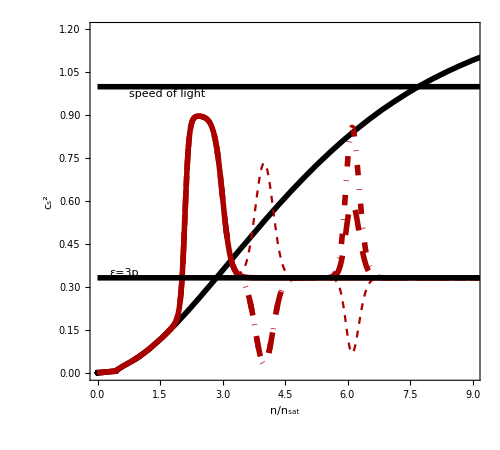

```mathematica
crz0=runbump2[cs2low,{0.1,0.2,0.2},{0.9,1./3,1./3},{2.1,3,7},{0,0},{0.3,0.3},{5,7}]
crz1=runbump2[cs2low,{0.1,0.2,0.2},{0.9,1./3,1./3},{2.1,3,6},{0.3,-0.4},{0.3,0.3},{4,6}]
crz2=runbump2[cs2low,{0.1,0.2,0.2},{0.9,1./3,1./3},{2.1,3,6},{0.3,-0.8},{0.3,0.3},{4,6}]
crz3=runbump2[cs2low,{0.1,0.2,0.2},{0.9,1./3,1./3},{2.1,3,6},{-0.4,0.4},{0.3,0.3},{4,6}]
csplotvar[cs2low,{crz0,crz1,crz2,crz3}]
```

```mathematica
wraper["afterbump",{crz0,crz1,crz2,crz3}]
```

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/afterbump already exists.

InterpolatingFunction::dmval: Input value {9.62} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.64} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: Exp[-709.334] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-711.111] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-712.89] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

eos done

eos done

eos done

«1 more identical outputs»

here

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

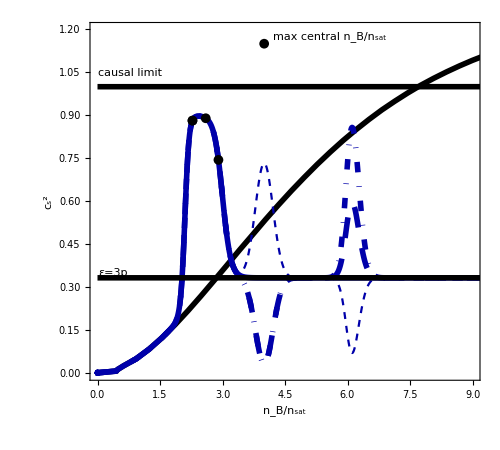
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
miniplots[10]
```

### Boring

```mathematica
runbump2[cs2nint_,b_,cmax_,ns_,mag_,width_,off_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot},
c1[x_]:=s[x,ns[[1]],b[[1]]] cmax[[1]]+(1-s[x,ns[[1]],b[[1]]])*cs2nint[x];

c2[x_]:=s[x,ns[[2]],b[[2]]]*fun[x,mag[[1]],width[[1]],off[[1]]]+(1-s[x,ns[[2]],b[[2]]])*c1[x];

Return[c2];
]
```

c3$845753

c3$845754

c3$845755

c3$845756

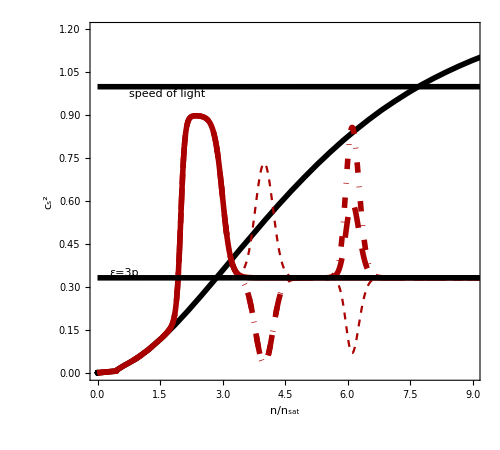

```mathematica
crz0=runbump2[cs2low,{0.1,0.2,0.2},{0.9,1./3,1./3},{2,3,7},{0,0},{0.3,0.3},{5,7}]
crz1=runbump2[cs2low,{0.1,0.2,0.2},{0.9,1./3,1./3},{2,3,6},{0.3,-0.4},{0.3,0.3},{4,6}]
crz2=runbump2[cs2low,{0.1,0.2,0.2},{0.9,1./3,1./3},{2,3,6},{0.3,-0.8},{0.3,0.3},{4,6}]
crz3=runbump2[cs2low,{0.1,0.2,0.2},{0.9,1./3,1./3},{2,3,6},{-0.4,0.4},{0.3,0.3},{4,6}]
csplotvar[cs2ex,{crz0,crz1,crz2,crz3}]
```

```mathematica
wraper["afterbump",{crz0,crz1,crz2,crz3}]
```

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/afterbump already exists.

InterpolatingFunction::dmval: Input value {9.62} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.64} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: Exp[-709.334] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-711.111] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-712.89] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

here

### runosc

```mathematica
cp=runosc[cs2low,{0.2,0.005},4,0.5,0.1,0.5,0.5,3]
cp1=disbump1[cs2low,0.5,1./3,4]
cp2=disbump2[cs2low,{0.5,0.2},{0.5,0.1},{4,5},-0.3,0.2,6]
cp3=disjump[cs2low,{0.5,0.2},{0.5,0.7},{4,4.2},-0.5,0.1,4.5]
```

c1$80212

InterpolatingFunction::dmval: Input value {9.62} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.64} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

-Graphics-

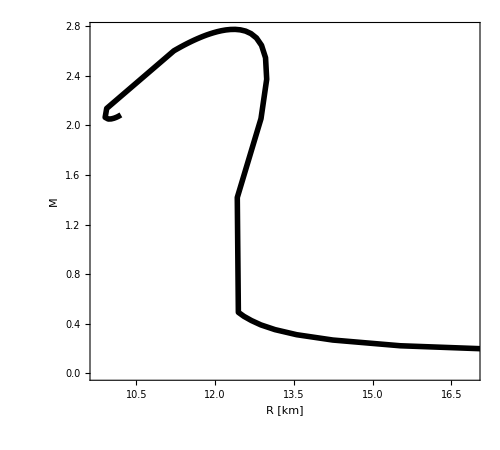
{-Graphics-,{{23.2037,0.115136},{18.8825,0.170535},{15.5263,0.222573},{14.241,0.268786},{13.5538,0.311731},{13.141,0.352659},{12.8723,0.390733},{12.6921,0.425891},{12.5501,0.459622},{12.4436,0.492085},{12.423,1.41807},{12.8744,2.05394},{12.9829,2.37146},{12.9609,2.5446},{12.8847,2.64464},{12.7881,2.70407},{12.6839,2.73933},{12.5815,2.75945},{12.4802,2.76973},{12.3844,2.77343},{12.2925,2.77265},{12.2041,2.76877},{12.1226,2.76273},{12.0443,2.7552},{11.9713,2.74662},{11.9015,2.73733},{11.8345,2.72758},{11.7723,2.71754},{11.7133,2.70734},{11.6568,2.69708},{11.6031,2.68683},{11.5518,2.67664},{11.5031,2.66656},{11.4565,2.65661},{11.4119,2.64681},{11.3693,2.63719},{11.3288,2.62774},{11.2897,2.61848},{11.2517,2.60941},{11.2158,2.60054},{9.93713,2.1361},{9.9078,2.06409},{9.96716,2.0506},{10.0237,2.0516},{10.0751,2.0571},{10.1178,2.06393},{10.1532,2.07093},{10.1814,2.07764},{10.2075,2.08391}}}

```mathematica
cp=runosc[cs2low,{0.2,0.005},2,0.8,0.1,0.5,0.5,0]
cs2EOS[cp,sly,2]
```

c1$77469

InterpolatingFunction::dmval: Input value {9.62} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.64} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

-Graphics-

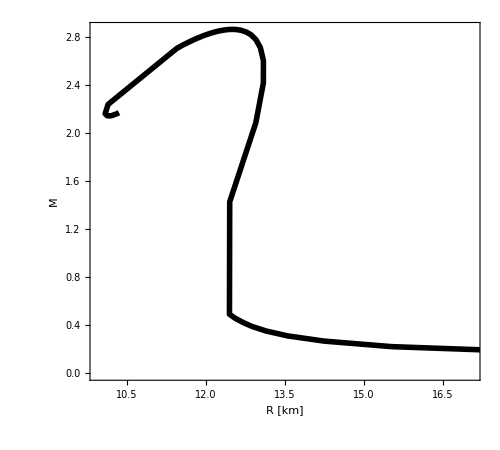
{-Graphics-,{{23.2037,0.115136},{18.8825,0.170535},{15.5263,0.222573},{14.241,0.268786},{13.5538,0.311731},{13.141,0.352659},{12.8723,0.390733},{12.6921,0.425891},{12.5501,0.459622},{12.4436,0.492085},{12.4484,1.42879},{12.9438,2.0853},{13.0883,2.41877},{13.0888,2.60353},{13.0312,2.71219},{12.948,2.77819},{12.8567,2.81858},{12.7614,2.84281},{12.668,2.85643},{12.5773,2.86291},{12.4906,2.86444},{12.4081,2.86253},{12.329,2.85817},{12.2544,2.85208},{12.1826,2.84475},{12.1163,2.83656},{12.0521,2.82777},{11.9914,2.81858},{11.9335,2.80913},{11.8807,2.79954},{11.8261,2.78989},{11.7758,2.78024},{11.7281,2.77063},{11.6818,2.76111},{11.639,2.7517},{11.5967,2.74243},{11.5537,2.7333},{11.5177,2.72432},{11.4813,2.71551},{11.4456,2.70687},{10.1361,2.23939},{10.0811,2.16223},{10.119,2.1455},{10.1759,2.14425},{10.2209,2.1481},{10.2506,2.15368},{10.2917,2.15971},{10.3198,2.16566},{10.3436,2.1713}}}

```mathematica
cp=runosc[cs2low,{0.2,0.005},2,0.9,0.1,0.5,0.5,0]
cs2EOS[cp,sly,2]
```

c1$74726

InterpolatingFunction::dmval: Input value {9.62} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.64} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

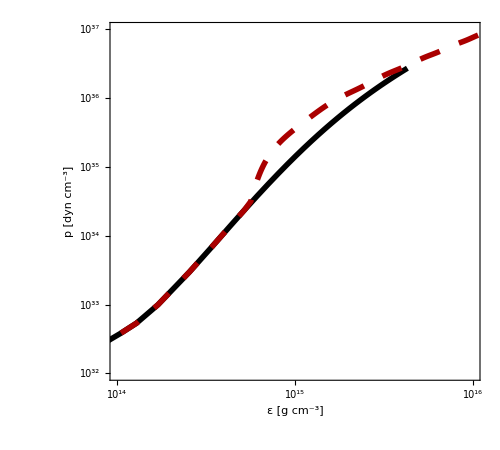

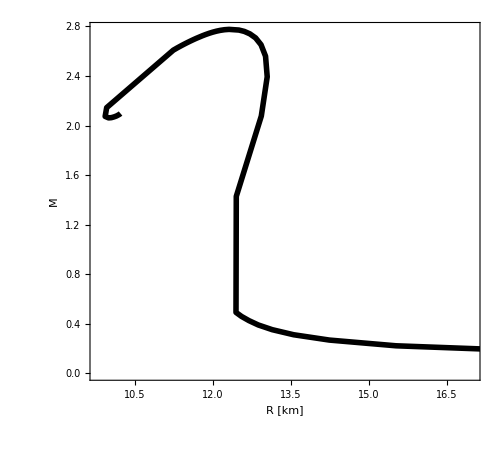
{-Graphics-,{{23.2037,0.115136},{18.8825,0.170535},{15.5263,0.222573},{14.241,0.268786},{13.5538,0.311731},{13.141,0.352659},{12.8723,0.390733},{12.6921,0.425891},{12.5501,0.459622},{12.4436,0.492085},{12.4492,1.42857},{12.931,2.07691},{13.0447,2.39374},{13.0126,2.55972},{12.9256,2.65254},{12.8215,2.7072},{12.7104,2.7402},{12.6039,2.75989},{12.5,2.77083},{12.3101,2.77627},{12.2234,2.77359},{12.1418,2.7685},{12.0653,2.76162},{11.9925,2.75346},{11.924,2.74439},{11.8587,2.73474},{11.7965,2.72473},{11.6804,2.70426},{11.6265,2.69402},{11.5748,2.68386},{11.5256,2.67383},{11.4784,2.66396},{11.4335,2.65426},{11.3906,2.64476},{11.3496,2.63547},{11.3099,2.62637},{11.2736,2.61747},{11.2371,2.60876},{9.95326,2.14473},{9.92387,2.07387},{9.98997,2.06198},{10.0447,2.06399},{10.0963,2.07008},{10.1418,2.07726},{10.1739,2.08444},{10.2023,2.09124},{10.2197,2.09753}}}

```mathematica
cp=runosc[cs2low,{0.2,0.005},2,0.9,0.1,0.5,0.5,3]
cs2EOS[cp,sly,2]
```

```mathematica
cp=runosc[cs2low,{0.2,0.005},4,0.33,0.1,0.5,0.5,3]
cp1=disbump1[cs2low,0.5,1./3,4]
cp2=disbump2[cs2low,{0.5,0.2},{0.5,0.1},{4,5},-0.3,0.2,6]
cp3=disjump[cs2low,{0.5,0.2},{0.5,0.7},{4,4.2},-0.5,0.1,4.5]
csplot[cs2ex,cp3]
eosout=comblowden[tabMeVfm3,cp3,4]
(*mrout=genmr[eosout]
ListLinePlot[mrout]*)
```

c1$5176

c1$5177

{4,0.531019}

{5,0.333333}

{4.59884,0.172406}

c2$5178

c2$5180

-Graphics-

General::munfl: Exp[-712.89] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-718.24] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-723.61] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{InterpolatingFunction[…],21[…],{1},{{2.14432×10^-6,41.5964},{0.0000136728,131.539},{0.000087182,415.964},{0.000555899,1315.39},{0.00354458,4159.65},{0.0226013,13154.},1667,{3.17202×10^15,9.80841×10^15},{3.17419×10^15,9.81491×10^15},{3.17635×10^15,9.82142×10^15},{3.17852×10^15,9.82793×10^15},{3.18069×10^15,9.83444×10^15},{3.18286×10^15,9.84095×10^15}}}
 |  |  |  |

```mathematica
cso[list_]:=Delete[Table[{list[[i,1]]/nsat,list[[i,4]]},{i,Length[list]}],1]
```

```mathematica
(*runbump3[b_,cmax_,ns_,mag_,width_,off_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,name},
c1[x_]:=s[x,ns[[1]],b[[1]]] cmax[[1]]+(1-s[x,ns[[1]],b[[1]]])*cs2nint[x];

c2[x_]:=s[x,ns[[2]],b[[2]]]*fun[x,mag[[1]],width[[1]],off[[1]]]+(1-s[x,ns[[2]],b[[2]]])*c1[x];
c3[x_]:=s[x,ns[[3]],b[[3]]]*fun[x,mag[[2]],width[[2]],off[[2]]]+(1-s[x,ns[[3]],b[[3]]])*c2[x];*)
```

```mathematica
runbump1[0.5,1./3,4]
```

InterpolatingFunction::dmval: Input value {9.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.07} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.08} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

DeleteFile::fdnfnd: Directory or file /Users/jacquelynnoronhahostler/Dropbox/neutronStars/data/1bump_b0.5_csfin0.333_switch4/eos.dat not found.

```mathematica
runbump2[{0.5,0.2},{0.5,1./3},{4,6},-0.3,0.2,6]
```

General::munfl: Exp[-899.939] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

InterpolatingFunction::dmval: Input value {9.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.07} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.08} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: -0.3 5.13566×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710.222] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

DeleteFile::fdnfnd: Directory or file /Users/jacquelynnoronhahostler/Dropbox/neutronStars/data/2bump_b0.5_0.2_csfin0.5_0.333_switch4_6_mag-0.3_width0.2_width6/eos.dat not found.

### playing with interpolation function

28.0771-16.698 x+3.31267 x^2-0.21646 x^3

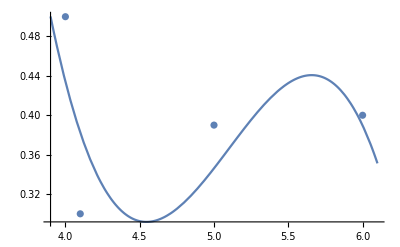

```mathematica
para=Fit[{{4,0.5},{4.1,0.3},{5,0.39},{5.5,0.395},{6,0.4}},{1,x,x^2,x^3},x]
Show[{Plot[para,{x,3.9,6.1}],ListPlot[{{4,0.5},{4.1,0.3},{5,0.39},{6,0.4}}]}]
```

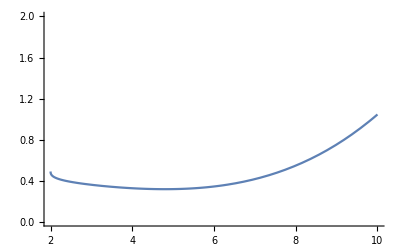

```mathematica
f3[x_,a1_,n1_,a2_,n2_]:=0.5-0.2((x-2)/a1)^n1+0.3((x-3)/a2)^n2
Plot[f3[x,3,1/3,5,3],{x,0,10},PlotRange->{All,{0,2}}]
```

```mathematica
fde[x_]:=0.5-c1((x-b1)/a1)^n1+c2((x-b2)/a2)^n2
```

```mathematica
D[0.5-c1((x-b1)/a1)^n1+c2((x-b2)/a2)^n2,x]
```

```mathematica
Solve[0==-(c1 n1 ((-b1+x)/a1)^(-1+n1))/a1+(c2 n2 ((-b2+x)/a2)^(-1+n2))/a2,x]
```

$Aborted

```mathematica
Solve[A*(-b1+x)^-2==(-b2+x)^-3,x]
```

{{x→-(-1-3 A b2)/(3 A)-(2^(1/3) (-1+6 A b1-6 A b2))/(3 A (2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2+√(4 (-1+6 A b1-6 A b2)^3+(2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2)^2))^(1/3))+((2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2+√(4 (-1+6 A b1-6 A b2)^3+(2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2)^2))^(1/3))/(3 2^(1/3) A)},{x→-(-1-3 A b2)/(3 A)+((1+ⅈ √3) (-1+6 A b1-6 A b2))/(3 2^(2/3) A (2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2+√(4 (-1+6 A b1-6 A b2)^3+(2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2)^2))^(1/3))-((1-ⅈ √3) (2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2+√(4 (-1+6 A b1-6 A b2)^3+(2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2)^2))^(1/3))/(6 2^(1/3) A)},{x→-(-1-3 A b2)/(3 A)+((1-ⅈ √3) (-1+6 A b1-6 A b2))/(3 2^(2/3) A (2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2+√(4 (-1+6 A b1-6 A b2)^3+(2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2)^2))^(1/3))-((1+ⅈ √3) (2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2+√(4 (-1+6 A b1-6 A b2)^3+(2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2)^2))^(1/3))/(6 2^(1/3) A)}}

### flat peak

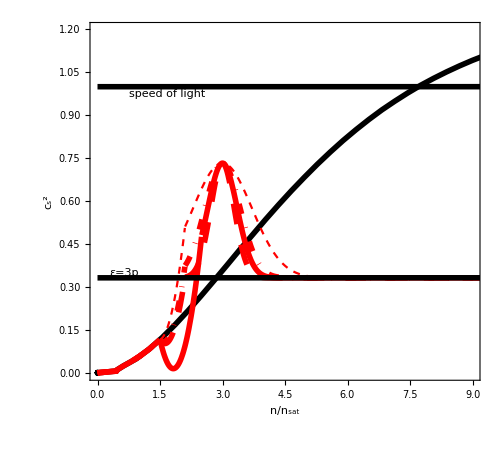

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/flatpeak already exists.

General::munfl: -0.4 5.13566×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.624] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.69] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

eos done

eos done

eos done

«1 more identical outputs»

here

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
f0=disbump2[cs2low,{1.5,2.5},-0.4,0.5,3];
f1=disbump2[cs2low,{1.5,2.1},-0.4,0.4,3];
f2=disbump2[cs2low,{1.5,2.1},-0.4,0.6,3];
f3=disbump2[cs2low,{1.5,2.1},-0.4,1,3];
csplotvar[cs2low,{f0,f1,f2,f3}]
wraper["flatpeak",{f0,f1,f2,f3}]
```

```mathematica
bumpswitch[cs2nint_,b_,cmax_,ns_,mag_,width_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,dec,B},
(*start with sly, cs2nint,  then Gaussian, then exponential -> cmax*)

(*ns[[1]] ->  start bump
ns[[2]] -> downward after bump
*)
fun[x_]:=cs2nint[ns[[1]]]+mag*Exp[-(x-ns[[2]])^2/width^2];
B=ns[[2]] +Log[(c1[ns[[2]]]-cmax) ]  ;
dec[x_]:=cmax+Exp[-(x-B)];


c1[x_]:=s[x,ns[[1]],b]* fun[x]+(1-s[x,ns[[1]],b])*cs2nint[x];
c2[x_]:=Which[x<=ns[[2]],c1[x],x> ns[[2]],dec[x]];
Return[c2];
]
bumpswitch2[cs2nint_,b_,cmax_,ns_,mag_,width_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,dec,B,dec2,B2,fun2,call},
(*start with sly, cs2nint,  then Gaussian, then exponential -> cmax*)

(*ns[[1]] ->  start bump
ns[[2]] -> downward after bump
*)
fun[x_]:=cs2nint[ns[[1]]]+mag[[1]]*Exp[-(x-ns[[2]])^2/width[[1]]^2];
B=ns[[2]] +Log[(c1[ns[[2]]]-cmax[[1]])]  ;
dec[x_]:=cmax[[1]]+Exp[-(x-B)];

fun2[x_]:=dec[ns[[3]]]+mag[[2]]*Exp[-(x-ns[[4]])^2/width[[2]]^2];
B2=ns[[4]] +Log[(c2[ns[[4]]]-cmax[[2]])]  ;
dec2[x_]:=cmax[[2]]+Exp[-(x-B2)];


c1[x_]:=s[x,ns[[1]],b]* fun[x]+(1-s[x,ns[[1]],b])*cs2nint[x];
c2[x_]:=s[x,ns[[3]],b]*fun2[x]+(1-s[x,ns[[3]],b])*dec[x];
call[x_]:=Which[x<=ns[[2]],c1[x], ns[[2]]<x<= ns[[3]],dec[x],ns[[3]]<x≤ns[[4]],c2[x],ns[[4]]<x,dec2[x]];
Return[call];
]
```

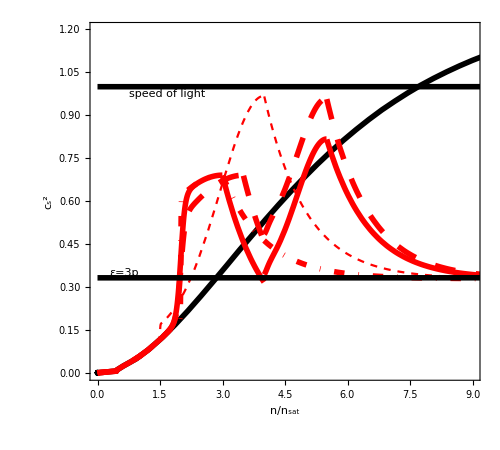

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/flatpeak already exists.

eos done

eos done

eos done

«1 more identical outputs»

here

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*bumpswitch[cs2nint_,b_,cmax_,ns_,mag_,width_]*)
f0=bumpswitch2[cs2low,0.1,{0.1,0.33},{2,3,4,5.5},{0.5,0.5},{2.5,1}];
f1=bumpswitch2[cs2low,0.1,{0.1,0.33},{2,3.5,4,5.5},{0.5,0.5},{2.5,1}];
f2=bumpswitch[cs2low,0.01,0.33,{2,3},0.5,2.5];

f3=bumpswitch[cs2low,0.01,0.33,{1.5,4},0.85,1.5]; (*ok*)

csplotvar[cs2low,{f0,f1,f2,f3}]
wraper["flatpeak",{f0,f1,f2,f3}]
```

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

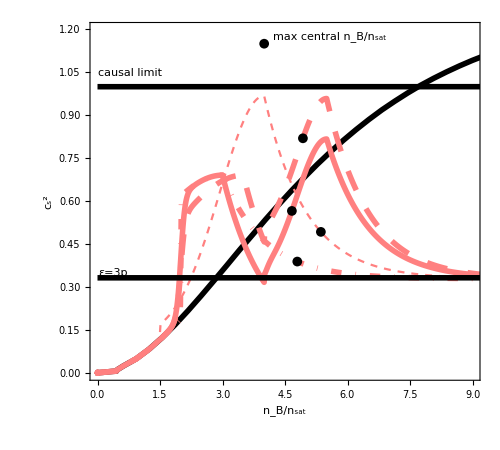
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
miniplots[12]
```

### Stair steps

```mathematica
disbumpend[cs2nint_,ns_,mag_,width_,off_,final_]:=Module[{c2,out,fun,fout},

fun[x_]:=final[[1]]-mag*Exp[-(x-off)^2/width^2];
fout=fx[cs2nint,fun,ns];
c2[x_]:=Which[x<ns[[1]],cs2nint[x],ns[[1]]≤ x≤ ns[[2]],fout[x],ns[[2]]<x< ns[[3]],fun[x],ns[[3]]≤x≤ns[[4]],final[[2]],ns[[4]]<x<ns[[5]],final[[3]],  ns[[5]]≤ x,final[[4]]];
Return[c2];
]
```

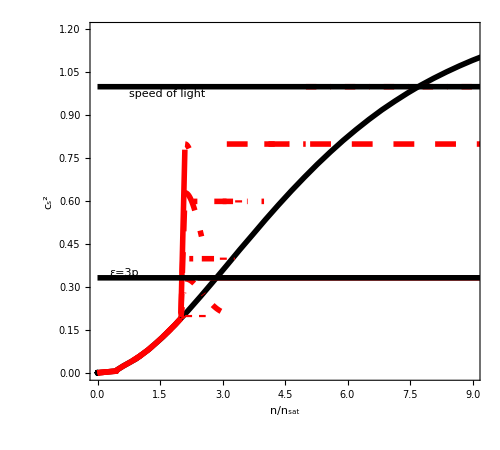

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/steps already exists.

eos done

eos done

eos done

«1 more identical outputs»

here

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
f0=disbumpend[cs2low,{2.0,2.1,2.2,2.3,2.4,2.5,2.6},-0.6,0.6,2.1,{0.2,0.4,0.6,0.8}];
f1=disbumpend[cs2low,{2.0,2.1,2.5,2.8,3.1},-0.43,0.6,2.1,{0.2,0.4,0.6,0.8}];
f2=disbumpend[cs2low,{2.0,2.1,3.,4.,5.,6.},-0.13,0.6,2.1,{0.2,0.6,0.8,1.}];
f3=disbumpend[cs2low,{2.0,2.1,2.6,3.1,3.6,4.1},0,0.6,2.1,{0.2,0.4,0.6,1.}];
csplotvar[cs2low,{f0,f1,f2,f3}]
wraper["steps",{f0,f1,f2,f3}]
```

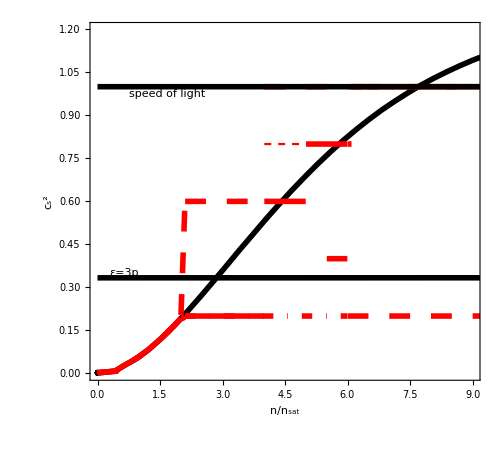

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/steps2 already exists.

eos done

eos done

eos done

«1 more identical outputs»

here

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
f0=disbumpend[cs2low,{2.0,2.1,4.,5.,6.,8.},0,0.6,2.1,{0.2,0.6,0.8,1.}];
f1=disbumpend[cs2low,{2.0,2.1,4.,5.5,6.,8.},0,0.6,2.1,{0.6,1.0,0.4,0.2}];
f2=disbumpend[cs2low,{2.0,2.1,6.,6.1,6.5,8.},0,0.6,2.1,{0.2,0.8,1.0,1.0}];
f3=disbumpend[cs2low,{2.0,2.1,4.,5.,6.,8.},0,0.6,2.1,{0.2,0.8,1.,1.}];
csplotvar[cs2low,{f0,f1,f2,f3}]
wraper["steps2",{f0,f1,f2,f3}]
```

```mathematica
find0[eos_,mr_,cor_]:=Module[{out,csint,mrs,pt,cs0,o2,tab,pts,dots},

cs0=cs1PT[eos];
pt=ptmark[mr,cs0[[1]],cs0[[2]]];

csint=Interpolation[Table[{eos[[i,1]]/nsat,eos[[i,4]]},{i,Length[eos]}],InterpolationOrder->1];
(*Print[Plot[csint[x],{x,0.1,10},FrameLabel->{Style["n_B/n_sat",20],Style["c_s^2",20]},PlotStyle->MyStyle,ImageSize->500,Frame->True,LabelStyle->Directive[20],PlotRange->{{0,10},{0,1}}]];
Print[ListPlot[mr[[1;;300,{5,2}]],PlotMarkers->Automatic,PlotRange->{{0,10},{0.5,2.5}},PlotStyle->MyStyle,FrameLabel->{Style["n_B/n_sat",20],Style["M",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]]];
Print[ListPlot[mr[[1;;300,{5,1}]],PlotMarkers->Automatic,PlotRange->{{0,10},{8,15}},PlotStyle->MyStyle,FrameLabel->{Style["n_B/n_sat",20],Style["R",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]]];*)
mrs=Table[{mr[[i,1]],mr[[i,2]],0},{i,Length[mr]}];
(*Print[ListPlot[mrs[[1;;300,{2,3}]],Joined->True,PlotRange->All,FrameLabel->{Style["M",20],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]]];*)
out=ListLinePlot[mrs[[1;;250,1;;2]],PlotRange->{{8,20},{0.5,4}},PlotStyle->MyStyle[[cor]],FrameLabel->{Style["R",20],Style["M",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]];

tab=Table[{eos[[i,1]]/nsat,eos[[i,4]]},{i,Length[eos]}];
o2=ListLinePlot[tab,PlotRange->{{0,5},{0,1}},PlotStyle->MyStyle[[cor]],FrameLabel->{Style["n_B/n_sat",20],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]];

Return[{out,o2}];
]
```

## Mass twins construction

### nobump

```mathematica
nobump[cs2nint_,tr_,b_,ns_,dn_,cmax_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,fout,m,bb,x1,x2,y1,y2,mb,bbb,x1b,x2b,y1b,y2b},


y1=cs2nint[ns[[1]]];
x1=ns[[1]];
x2=ns[[1]]+dn[[1]];
m=-y1/dn[[1]];
bb=-m*x2;


mb=cmax/dn[[2]];
bbb=-mb*ns[[2]];

c1[x_]:=s[x,tr,b] fun[x]+(1-s[x,tr,b])*cs2nint[x];

c2[x_]:=Which[x≤ ns[[1]],cs2nint[x],ns[[1]]<  x< (ns[[1]]+dn[[1]]),m*x+bb,(ns[[1]]+dn[[1]])≤ x≤ ns[[2]],0.0001,ns[[2]]< x≤( ns[[2]]+dn[[2]]),mb*x+bbb,x> (ns[[2]]+dn[[2]]),cmax];
Return[c2];
]
```

c2$296829

c2$296830

c2$296831

c2$296832

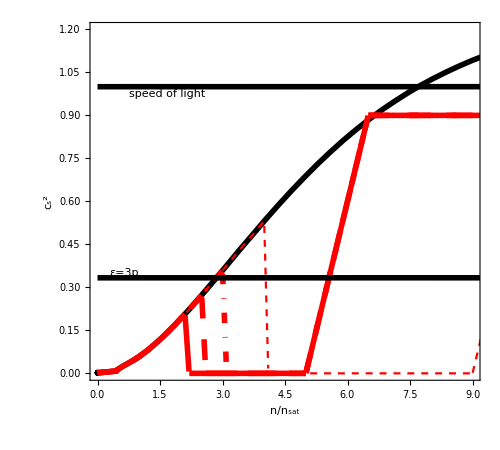

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/TW/nobump already exists.

Interpolation::inddp: The point 0.0000674241 in dimension 1 is duplicated.

$Aborted

```mathematica
tw1=nobump[cs2low,2,0.1,{2.1,5},{0.1,1.5},0.9]
tw2=nobump[cs2low,2,0.1,{2.5,5},{0.1,1.5},0.9]
tw3=nobump[cs2low,2,0.1,{3,5},{0.1,1.5},0.9]
tw4=nobump[cs2low,2,0.1,{4,9},{0.1,1.5},0.9]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/nobump",{tw1,tw2,tw3,tw4}]
```

### width of cs=0

```mathematica
Clear[cs0]
```

```mathematica
cs0[cs2nint_,tr_,b_,ns_,dn_,dn2_,mag_,width_,off_,cmax_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,fout,m,bb,x1,x2,y1,y2,mb,bbb,x1b,x2b,y1b,y2b},

fun[x_]:=1/3.-mag*Exp[-(x-off)^2/width^2];
y1=fun[ns[[1]]];
x1=ns[[1]];
x2=ns[[1]]+dn;
m=-y1/dn;
bb=-m*x2;


mb=cmax/dn2;
bbb=-mb*ns[[2]];

c1[x_]:=s[x,tr,b] fun[x]+(1-s[x,tr,b])*cs2nint[x];

c2[x_]:=Which[x≤ ns[[1]],c1[x],ns[[1]]<  x< (ns[[1]]+dn),m*x+bb,(ns[[1]]+dn)≤ x≤ ns[[2]],0.0001,ns[[2]]< x≤( ns[[2]]+dn2),mb*x+bbb,x> (ns[[2]]+dn2),cmax];
Return[c2];
]
```

c2$238914

c2$238915

c2$238916

c2$238917

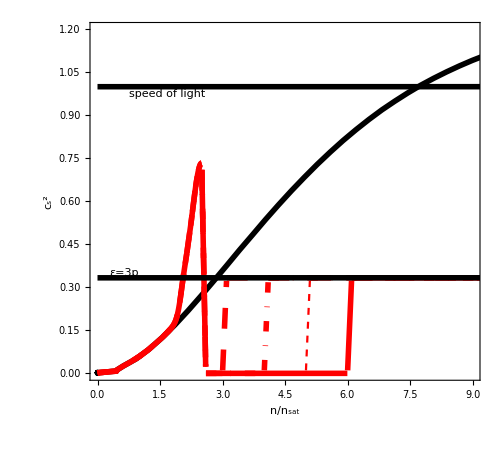

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/TW/cs0 already exists.

here

InterpolatingFunction::dmval: Input value {4742.23} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5021.18} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5300.14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
tw1=cs0[cs2low,2,0.1,{2.5,6},0.1,0.1,-0.4,0.3,2.5,1./3]
tw2=cs0[cs2low,2,0.1,{2.5,3},0.1,0.1,-0.4,0.3,2.5,1./3]
tw3=cs0[cs2low,2,0.1,{2.5,4},0.1,0.1,-0.4,0.3,2.5,1./3]
tw4=cs0[cs2low,2,0.1,{2.5,5},0.1,0.1,-0.4,0.3,2.5,1./3]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/cs0",{tw1,tw2,tw3,tw4}]
```

### height peak of cs=0

```mathematica
cs0[cs2nint_,tr_,b_,ns_,dn_,dn2_,mag_,width_,off_,cmax_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,fout,m,bb,x1,x2,y1,y2,mb,bbb,x1b,x2b,y1b,y2b},

fun[x_]:=1/3.-mag*Exp[-(x-off)^2/width^2];
y1=fun[ns[[1]]];
x1=ns[[1]];
x2=ns[[1]]+dn;
m=-y1/dn;
bb=-m*x2;


mb=cmax/dn2;
bbb=-mb*ns[[2]];

c1[x_]:=s[x,tr,b] fun[x]+(1-s[x,tr,b])*cs2nint[x];

c2[x_]:=Which[x≤ ns[[1]],c1[x],ns[[1]]<  x< (ns[[1]]+dn),m*x+bb,(ns[[1]]+dn)≤ x≤ ns[[2]],0.0001,ns[[2]]< x≤( ns[[2]]+dn2),mb*x+bbb,x> (ns[[2]]+dn2),cmax];
Return[c2];
]
```

c2$343652

c2$343653

c2$343654

c2$343655

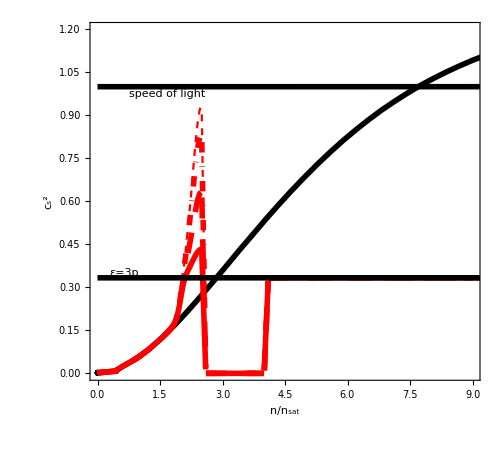

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/TW/peak already exists.

here

InterpolatingFunction::dmval: Input value {5300.14} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5579.09} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5858.04} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
tw1=cs0[cs2low,2,0.1,{2.5,4},0.1,0.1,-0.1,0.3,2.5,1/3.]
tw2=cs0[cs2low,2,0.1,{2.5,4},0.1,0.1,-0.3,0.3,2.5,1/3.]
tw3=cs0[cs2low,2,0.1,{2.5,4},0.1,0.1,-0.5,0.3,2.5,1/3.]
tw4=cs0[cs2low,2,0.1,{2.5,4},0.1,0.1,-0.6,0.3,2.5,1/3.]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/peak",{tw1,tw2,tw3,tw4}]
```

### height peak of cs=0 twin high

```mathematica
cs0[cs2nint_,tr_,b_,ns_,dn_,dn2_,mag_,width_,off_,cmax_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,fout,m,bb,x1,x2,y1,y2,mb,bbb,x1b,x2b,y1b,y2b},

fun[x_]:=1/3.-mag*Exp[-(x-off)^2/width^2];
y1=fun[ns[[1]]];
x1=ns[[1]];
x2=ns[[1]]+dn;
m=-y1/dn;
bb=-m*x2;


mb=cmax/dn2;
bbb=-mb*ns[[2]];

c1[x_]:=s[x,tr,b] fun[x]+(1-s[x,tr,b])*cs2nint[x];

c2[x_]:=Which[x≤ ns[[1]],c1[x],ns[[1]]<  x< (ns[[1]]+dn),m*x+bb,(ns[[1]]+dn)≤ x≤ ns[[2]],0.0001,ns[[2]]< x≤( ns[[2]]+dn2),mb*x+bbb,x> (ns[[2]]+dn2),cmax];
Return[c2];
]
```

c2$385196

c2$385197

c2$385198

c2$385199

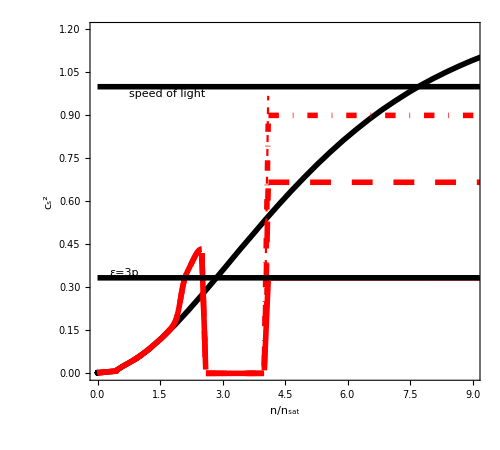

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/TW/peak_endhigh already exists.

here

InterpolatingFunction::dmval: Input value {5300.14} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5579.09} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5858.04} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
tw1=cs0[cs2low,2,0.1,{2.5,4},0.1,0.1,-0.1,0.3,2.5,1/3]
tw2=cs0[cs2low,2,0.1,{2.5,4},0.1,0.1,-0.1,0.3,2.5,2/3]
tw3=cs0[cs2low,2,0.1,{2.5,4},0.1,0.1,-0.1,0.3,2.5,0.9]
tw4=cs0[cs2low,2,0.1,{2.5,4},0.1,0.1,-0.1,0.3,2.5,1.]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/peak_endhigh",{tw1,tw2,tw3,tw4}]
```

c2$426610

c2$426611

c2$426612

c2$426613

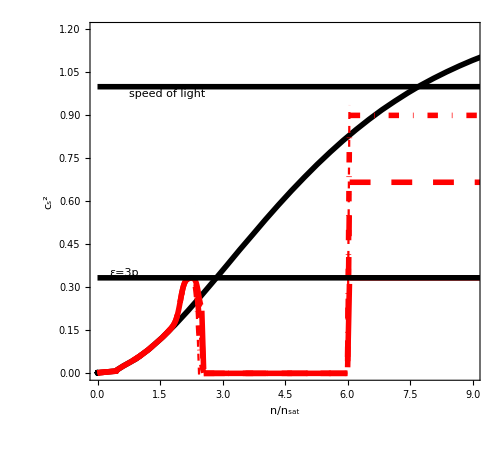

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/TW/peak_endhigh already exists.

$Aborted

```mathematica
tw1=cs0[cs2low,2,0.1,{2.5,6},0.05,0.05,0.1,0.1,2.5,1/3]
tw2=cs0[cs2low,2,0.1,{2.5,6},0.05,0.05,0.2,0.1,2.5,2/3]
tw3=cs0[cs2low,2,0.1,{2.5,6},0.05,0.05,0.3,0.1,2.5,0.9]
tw4=cs0[cs2low,2,0.1,{2.5,6},0.05,0.05,0.5,0.1,2.5,1.]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/peak_endhigh",{tw1,tw2,tw3,tw4}]
```

### peak at low nB

```mathematica
cs0[cs2nint_,tr_,b_,ns_,dn_,dn2_,mag_,width_,off_,cmax_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,fout,m,bb,x1,x2,y1,y2,mb,bbb,x1b,x2b,y1b,y2b},

fun[x_]:=cs2nint[x]-mag*Exp[-(x-off)^2/width^2];
y1=fun[ns[[1]]];
x1=ns[[1]];
x2=ns[[1]]+dn;
m=-y1/dn;
bb=-m*x2;


mb=cmax/dn2;
bbb=-mb*ns[[2]];

c1[x_]:=s[x,tr,b] fun[x]+(1-s[x,tr,b])*cs2nint[x];

c2[x_]:=Which[x≤ ns[[1]],c1[x],ns[[1]]<  x< (ns[[1]]+dn),m*x+bb,(ns[[1]]+dn)≤ x≤ ns[[2]],0.0001,ns[[2]]< x≤( ns[[2]]+dn2),mb*x+bbb,x> (ns[[2]]+dn2),cmax];
Return[c2];
]
```

```mathematica
cslowPT[cs2nint_,tr_,b_,ns_,dn_,dn2_,mag_,width_,off_,cmax_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,fout,m,bb,x1,x2,y1,y2,mb,bbb,x1b,x2b,y1b,y2b},

fun[x_]:=cs2nint[x]-mag*Exp[-(x-off)^2/width^2];
y1=cs2nint[ns[[1]]];
x1=ns[[1]];
x2=ns[[1]]+dn;
m=-y1/dn;
bb=-m*x2;


mb=cs2nint[ns[[2]]]/dn2;
bbb=-mb*ns[[2]];

c1[x_]:=s[x,tr,b] fun[x]+(1-s[x,tr,b])*cs2nint[x];

c2[x_]:=Which[x≤ ns[[1]],cs2nint[x],ns[[1]]<  x< (ns[[1]]+dn),m*x+bb,(ns[[1]]+dn)≤ x≤ ns[[2]],0.0001,ns[[2]]< x≤( ns[[2]]+dn2),mb*x+bbb,ns[[3]]>x> (ns[[2]]+dn2),cs2nint[x],x≥  ns[[3]],c1[x]];
Return[c2];
]
```

```mathematica
csthird[cs2nint_,tr_,b_,ns_,dn_,dn2_,mag_,width_,off_,cmax_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,fout,m,bb,x1,x2,y1,y2,mb,bbb,x1b,x2b,y1b,y2b},

fun[x_]:=1./3-mag*Exp[-(x-off)^2/width^2];
y1=fun[ns[[1]]];
x1=ns[[1]];
x2=ns[[1]]+dn;
m=-y1/dn;
bb=-m*x2;


mb=cmax/dn2;
bbb=-mb*ns[[2]];

c1[x_]:=s[x,tr,b] fun[x]+(1-s[x,tr,b])*cs2nint[x];

c2[x_]:=Which[x≤ ns[[1]],c1[x],ns[[1]]<  x< (ns[[1]]+dn),m*x+bb,(ns[[1]]+dn)≤ x≤ ns[[2]],0.0001,ns[[2]]< x≤( ns[[2]]+dn2),mb*x+bbb,x> (ns[[2]]+dn2),cmax];
Return[c2];
]
```

c2$666457

c2$666458

c2$666459

c2$666460

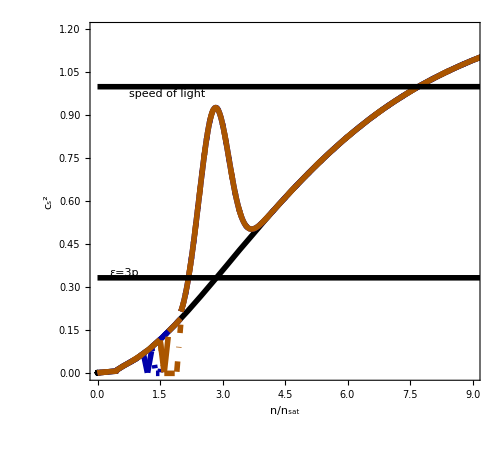

InterpolatingFunction::dmval: Input value {9.62} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.625} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: -0.6 3.01653×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.624] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.157] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
tw1=cslowPT[cs2low,2.,0.2,{1.1,1.2,2.},0.1,0.1,-0.6,0.5,2.8,0.8] 
tw2=cslowPT[cs2low,2.,0.2,{1.3,1.5,2.},0.1,0.1,-0.6,0.5,2.8,0.8] 
tw3=cslowPT[cs2low,2.,0.2,{1.5,1.6,2.},0.1,0.1,-0.6,0.5,2.8,0.8] 
tw4=cslowPT[cs2low,2.,0.2,{1.5,1.9,2.},0.1,0.1,-0.6,0.5,2.8,0.8] 
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
mrtest=wraperTW["TW/Blat_repeat2",{tw1,tw2,tw3,tw4}]
enter="TW/Blat_repeat2";
runlowM[enter,1]
runlowM[enter,2]
runlowM[enter,3]
runlowM[enter,4]
```

```mathematica
tw1=cslowPT[cs2low,2.,0.2,{0.5,1.,2.},0.1,0.1,-0.6,0.5,2.8,0.8] 
tw2=cslowPT[cs2low,2.,0.2,{0.8,1.,2.},0.1,0.1,-0.6,0.5,2.8,0.8] 
tw3=cslowPT[cs2low,2.,0.2,{0.9,1.,2.},0.1,0.1,-0.6,0.5,2.8,0.8] 
tw4=cslowPT[cs2low,2.,0.2,{1.,1.5,2.},0.1,0.1,-0.6,0.5,2.8,0.8] 
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
mrtest=wraperTW["TW/Blat_repeat",{tw1,tw2,tw3,tw4}]
enter="TW/Blat_repeat";
runlowM[enter,1];
runlowM[enter,2];
runlowM[enter,3];
runlowM[enter,4];
```

c2$459672

c2$459673

c2$459674

c2$459675

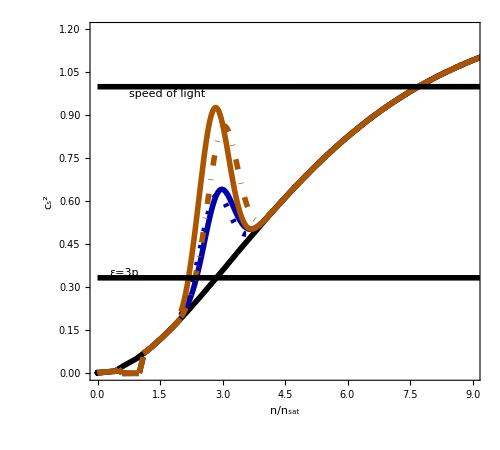

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/TW/low_n_peak already exists.

InterpolatingFunction::dmval: Input value {9.62} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.625} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: -0.3 5.13566×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -0.3 3.01653×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.624] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

```mathematica
tw1=cslowPT[cs2low,2.,0.5,{0.5,1.,2.},0.1,0.1,-0.3,0.5,2.9,0.4]
tw2=cslowPT[cs2low,2.,0.5,{0.5,1.,2.},0.1,0.1,-0.3,0.5,2.8,0.6] 
tw3=cslowPT[cs2low,2.,0.2,{0.5,1.,2.},0.1,0.1,-0.6,0.5,2.8,0.8] 
tw4=cslowPT[cs2low,2.,0.2,{0.5,1.,2.},0.1,0.1,-0.5,0.5,3,1.]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
mrtest=wraperTW["TW/low_n_peak",{tw1,tw2,tw3,tw4}]
```

```mathematica
enter="TW/low_n_peak";
runlowM[enter,1]
runlowM[enter,2]
runlowM[enter,3]
runlowM[enter,4]
```

NDSolve::precw: The precision of the differential equation ({{p'[rr]==If[rr>1/10000000,-((Gj Plus[«2»] Power[«2»]) (InterpolatingFunction[«5»][«1»] Power[«2»]+p[rr]))/(1+Times[«2»]),-((4 π Power[«2»]) Gj rr (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][9.×10^-7]+9.×10^-7) (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][9.×10^-7]+3 9.×10^-7))/Power[«2»]],M'[rr]==4 π rr^2 «1»[p[rr]],p[0]==9.×10^-7,M[0]==0},{},{},{},{WhenEvent[p[rr]≤minp$546942,{R=rr,Mmax=M[rr],StopIntegration},DetectionMethod→Interpolation]}}) is less than WorkingPrecision (26.).

InterpolatingFunction::dmval: Input value {20.3071} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.0892} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.8107} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{p'[rr]==If[rr>1/10000000,-((Gj Plus[«2»] Power[«2»]) (InterpolatingFunction[«5»][«1»] Power[«2»]+p[rr]))/(1+Times[«2»]),-((4 π Power[«2»]) Gj rr (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.×10^-6]+1.×10^-6) (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.×10^-6]+3 1.×10^-6))/Power[«2»]],M'[rr]==4 π rr^2 «1»,p[0]==1.×10^-6,M[0]==0},{},{},{},{WhenEvent[p[rr]≤minp$547023,{R=rr,Mmax=M[rr],StopIntegration},DetectionMethod→Interpolation]}}) is less than WorkingPrecision (26.).

NDSolve::precw: The precision of the differential equation ({{p'[rr]==If[rr>1/10000000,-((Gj Plus[«2»] Power[«2»]) (InterpolatingFunction[«5»][«1»] Power[«2»]+p[rr]))/(1+Times[«2»]),-((4 π Power[«2»]) Gj rr (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.5×10^-6]+1.5×10^-6) (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.5×10^-6]+3 1.5×10^-6))/Power[«2»]],M'[rr]==«1»,p[0]==1.5×10^-6,M[0]==0},{},{},{},{WhenEvent[p[rr]≤minp$547100,{R=rr,Mmax=M[rr],StopIntegration},DetectionMethod→Interpolation]}}) is less than WorkingPrecision (26.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

InterpolatingFunction[…]

{{23.727,0.109003,110.397,1.00424,0.0456248,102.979},{23.2555,0.114883,114.834,1.11582,0.0394186,107.104},{21.7325,0.132228,167.634,1.67373,0.0270588,122.776},{20.6221,0.145447,176.041,2.23164,0.0205207,170.819},{16.4372,0.182714,190.246,3.34745,0.0774337,186.768},{14.3026,0.225296,202.864,4.46327,0.356369,200.145},{13.2827,0.268563,214.226,5.57909,4.73,211.81},{12.7268,0.310922,224.648,6.69491,15.4309,222.363},{12.4083,0.351797,234.333,7.81073,34.1762,232.097},{12.2091,0.391003,243.421,8.92654,58.1484,241.194},{12.0772,0.428527,251.973,10.0424,78.8445,249.747}}

NDSolve::precw: The precision of the differential equation ({{p'[rr]==If[rr>1/10000000,-((Gj Plus[«2»] Power[«2»]) (InterpolatingFunction[«5»][«1»] Power[«2»]+p[rr]))/(1+Times[«2»]),-((4 π Power[«2»]) Gj rr (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][9.×10^-7]+9.×10^-7) (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][9.×10^-7]+3 9.×10^-7))/Power[«2»]],M'[rr]==4 π rr^2 InterpolatingFunction[{{1.69063×10^-25,0.0704203}},«3»,{Automatic}][p[rr]],p[0]==9.×10^-7,M[0]==0},{},{},{},{WhenEvent[p[rr]≤minp$547928,{R=rr,Mmax=M[rr],StopIntegration},DetectionMethod→Interpolation]}}) is less than WorkingPrecision (26.).

InterpolatingFunction::dmval: Input value {20.3071} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.0892} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.8107} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{p'[rr]==If[rr>1/10000000,-((Gj Plus[«2»] Power[«2»]) (InterpolatingFunction[«5»][«1»] Power[«2»]+p[rr]))/(1+Times[«2»]),-((4 π Power[«2»]) Gj rr (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.×10^-6]+1.×10^-6) (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.×10^-6]+3 1.×10^-6))/Power[«2»]],M'[rr]==«1»,p[0]==1.×10^-6,M[0]==0},{},{},{},{WhenEvent[p[rr]≤minp$548009,{R=rr,Mmax=M[rr],StopIntegration},DetectionMethod→Interpolation]}}) is less than WorkingPrecision (26.).

NDSolve::precw: The precision of the differential equation ({{p'[rr]==If[rr>1/10000000,-((Gj Plus[«2»] Power[«2»]) (InterpolatingFunction[«5»][«1»] Power[«2»]+p[rr]))/(1+Times[«2»]),-((4 π Power[«2»]) Gj rr (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.5×10^-6]+1.5×10^-6) (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.5×10^-6]+3 1.5×10^-6))/Power[«2»]],M'[rr]==«1»,p[0]==1.5×10^-6,M[0]==0},{},{},{},{WhenEvent[p[rr]≤minp$548086,{R=rr,Mmax=M[rr],StopIntegration},DetectionMethod→Interpolation]}}) is less than WorkingPrecision (26.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

InterpolatingFunction[…]

{{23.727,0.109003,110.397,1.00424,0.0456248,102.979},{23.2555,0.114883,114.834,1.11582,0.0394186,107.104},{21.7325,0.132228,167.634,1.67373,0.0270588,122.776},{20.6221,0.145447,176.041,2.23164,0.0205207,170.819},{16.4372,0.182714,190.246,3.34745,0.0774337,186.768},{14.3026,0.225296,202.864,4.46327,0.356369,200.145},{13.2827,0.268563,214.226,5.57909,4.73,211.81},{12.7268,0.310922,224.648,6.69491,15.4309,222.363},{12.4083,0.351797,234.333,7.81073,34.1762,232.097},{12.2091,0.391003,243.421,8.92654,58.1484,241.194},{12.0772,0.428527,251.973,10.0424,78.8445,249.747}}

NDSolve::precw: The precision of the differential equation ({{p'[rr]==If[rr>1/10000000,-((Gj Plus[«2»] Power[«2»]) (InterpolatingFunction[«5»][«1»] Power[«2»]+p[rr]))/(1+Times[«2»]),-((4 π Power[«2»]) Gj rr (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][9.×10^-7]+9.×10^-7) (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][9.×10^-7]+3 9.×10^-7))/Power[«2»]],M'[rr]==4 π rr^2 InterpolatingFunction[{{1.69063×10^-25,0.0777921}},«3»,{Automatic}][p[rr]],p[0]==9.×10^-7,M[0]==0},{},{},{},{WhenEvent[p[rr]≤minp$548914,{R=rr,Mmax=M[rr],StopIntegration},DetectionMethod→Interpolation]}}) is less than WorkingPrecision (26.).

InterpolatingFunction::dmval: Input value {20.3071} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.0892} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.8107} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{p'[rr]==If[rr>1/10000000,-((Gj Plus[«2»] Power[«2»]) (InterpolatingFunction[«5»][«1»] Power[«2»]+p[rr]))/(1+Times[«2»]),-((4 π Power[«2»]) Gj rr (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.×10^-6]+1.×10^-6) (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.×10^-6]+3 1.×10^-6))/Power[«2»]],M'[rr]==«1»,p[0]==1.×10^-6,M[0]==0},{},{},{},{WhenEvent[p[rr]≤minp$548995,{R=rr,Mmax=M[rr],StopIntegration},DetectionMethod→Interpolation]}}) is less than WorkingPrecision (26.).

NDSolve::precw: The precision of the differential equation ({{p'[rr]==If[rr>1/10000000,-((Gj Plus[«2»] Power[«2»]) (InterpolatingFunction[«5»][«1»] Power[«2»]+p[rr]))/(1+Times[«2»]),-((4 π Power[«2»]) Gj rr (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.5×10^-6]+1.5×10^-6) (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.5×10^-6]+3 1.5×10^-6))/Power[«2»]],M'[rr]==«1»,p[0]==1.5×10^-6,M[0]==0},{},{},{},{WhenEvent[p[rr]≤minp$549072,{R=rr,Mmax=M[rr],StopIntegration},DetectionMethod→Interpolation]}}) is less than WorkingPrecision (26.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

InterpolatingFunction[…]

{{23.727,0.109003,110.397,1.00424,0.0456248,102.979},{23.2555,0.114883,114.834,1.11582,0.0394186,107.104},{21.7325,0.132228,167.634,1.67373,0.0270588,122.776},{20.6221,0.145447,176.041,2.23164,0.0205207,170.819},{16.4372,0.182714,190.246,3.34745,0.0774337,186.768},{14.3026,0.225296,202.864,4.46327,0.356369,200.145},{13.2827,0.268563,214.226,5.57909,4.73,211.81},{12.7268,0.310922,224.648,6.69491,15.4309,222.363},{12.4083,0.351797,234.333,7.81073,34.1762,232.097},{12.2091,0.391003,243.421,8.92654,58.1484,241.194},{12.0772,0.428527,251.973,10.0424,78.8445,249.747}}

NDSolve::precw: The precision of the differential equation ({{p'[rr]==If[rr>1/10000000,-((Gj Plus[«2»] Power[«2»]) (InterpolatingFunction[«5»][«1»] Power[«2»]+p[rr]))/(1+Times[«2»]),-((4 π Power[«2»]) Gj rr (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][9.×10^-7]+9.×10^-7) (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][9.×10^-7]+3 9.×10^-7))/Power[«2»]],M'[rr]==4 π rr^2 InterpolatingFunction[{{1.69063×10^-25,0.0748883}},«3»,{Automatic}][p[rr]],p[0]==9.×10^-7,M[0]==0},{},{},{},{WhenEvent[p[rr]≤minp$549900,{R=rr,Mmax=M[rr],StopIntegration},DetectionMethod→Interpolation]}}) is less than WorkingPrecision (26.).

InterpolatingFunction::dmval: Input value {20.3071} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.0892} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.8107} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{p'[rr]==If[rr>1/10000000,-((Gj Plus[«2»] Power[«2»]) (InterpolatingFunction[«5»][«1»] Power[«2»]+p[rr]))/(1+Times[«2»]),-((4 π Power[«2»]) Gj rr (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.×10^-6]+1.×10^-6) (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.×10^-6]+3 1.×10^-6))/Power[«2»]],M'[rr]==«1»,p[0]==1.×10^-6,M[0]==0},{},{},{},{WhenEvent[p[rr]≤minp$549981,{R=rr,Mmax=M[rr],StopIntegration},DetectionMethod→Interpolation]}}) is less than WorkingPrecision (26.).

NDSolve::precw: The precision of the differential equation ({{p'[rr]==If[rr>1/10000000,-((Gj Plus[«2»] Power[«2»]) (InterpolatingFunction[«5»][«1»] Power[«2»]+p[rr]))/(1+Times[«2»]),-((4 π Power[«2»]) Gj rr (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.5×10^-6]+1.5×10^-6) (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.5×10^-6]+3 1.5×10^-6))/Power[«2»]],M'[rr]==«1»,p[0]==1.5×10^-6,M[0]==0},{},{},{},{WhenEvent[p[rr]≤minp$550058,{R=rr,Mmax=M[rr],StopIntegration},DetectionMethod→Interpolation]}}) is less than WorkingPrecision (26.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

InterpolatingFunction[…]

{{23.727,0.109003,110.397,1.00424,0.0456248,102.979},{23.2555,0.114883,114.834,1.11582,0.0394186,107.104},{21.7325,0.132228,167.634,1.67373,0.0270588,122.776},{20.6221,0.145447,176.041,2.23164,0.0205207,170.819},{16.4372,0.182714,190.246,3.34745,0.0774337,186.768},{14.3026,0.225296,202.864,4.46327,0.356369,200.145},{13.2827,0.268563,214.226,5.57909,4.73,211.81},{12.7268,0.310922,224.648,6.69491,15.4309,222.363},{12.4083,0.351797,234.333,7.81073,34.1762,232.097},{12.2091,0.391003,243.421,8.92654,58.1484,241.194},{12.0772,0.428527,251.973,10.0424,78.8445,249.747}}

```mathematica
tw2=csthird[cs2low,1.2,0.1,{1.5,4},0.1,0.1,-0.65,0.3,1.4,1.] (*keep*)
tw3=csthird[cs2low,1.6,0.1,{1.9,2.5},0.1,0.1,-0.65,0.3,1.8,1.] (*keep*)
```

```mathematica
runlowM["TW/low_n_peak1st",2]
```

NDSolve::precw: The precision of the differential equation ({{p'[rr]==If[rr>1/10000000,-((Gj Plus[«2»] Power[«2»]) (InterpolatingFunction[«5»][«1»] Power[«2»]+p[rr]))/(1+Times[«2»]),-((4 π Power[«2»]) Gj rr (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][9.×10^-7]+9.×10^-7) (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][9.×10^-7]+3 9.×10^-7))/Power[«2»]],M'[rr]==4 π rr^2 InterpolatingFunction[{{1.69063×10^-25,0.0549259}},«3»,{Automatic}][p[rr]],p[0]==9.×10^-7,M[0]==0},{},{},{},{WhenEvent[p[rr]≤minp$105771,{R=rr,Mmax=M[rr],StopIntegration},DetectionMethod→Interpolation]}}) is less than WorkingPrecision (26.).

InterpolatingFunction::dmval: Input value {20.2629} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.0275} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.8078} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{p'[rr]==If[rr>1/10000000,-((Gj Plus[«2»] Power[«2»]) (InterpolatingFunction[«5»][«1»] Power[«2»]+p[rr]))/(1+Times[«2»]),-((4 π Power[«2»]) Gj rr (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.×10^-6]+1.×10^-6) (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.×10^-6]+3 1.×10^-6))/Power[«2»]],M'[rr]==«1»,p[0]==1.×10^-6,M[0]==0},{},{},{},{WhenEvent[p[rr]≤minp$105864,{R=rr,Mmax=M[rr],StopIntegration},DetectionMethod→Interpolation]}}) is less than WorkingPrecision (26.).

NDSolve::precw: The precision of the differential equation ({{p'[rr]==If[rr>1/10000000,-((Gj Plus[«2»] Power[«2»]) (InterpolatingFunction[«5»][«1»] Power[«2»]+p[rr]))/(1+Times[«2»]),-((4 π Power[«2»]) Gj rr (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.5×10^-6]+1.5×10^-6) (InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][1.5×10^-6]+3 1.5×10^-6))/Power[«2»]],M'[rr]==«1»,p[0]==1.5×10^-6,M[0]==0},{},{},{},{WhenEvent[p[rr]≤minp$105941,{R=rr,Mmax=M[rr],StopIntegration},DetectionMethod→Interpolation]}}) is less than WorkingPrecision (26.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

InterpolatingFunction[…]

{{23.7119,0.109246,109.757,1.00424,0.045435,102.72},{23.2102,0.115276,114.008,1.11582,0.0394275,106.714},{21.0244,0.145842,130.808,1.67373,0.0246112,125.86},{18.394,0.177443,142.432,2.23164,0.0446281,138.501},{15.2757,0.239062,160.391,3.34745,0.327094,158.016},{14.124,0.299365,171.281,4.46327,6.42653,169.935},{13.5736,0.360874,177.629,5.57909,24.5152,176.783},{13.305,0.424057,181.892,6.69491,56.5655,181.266},{13.196,0.488433,185.124,7.81073,85.6212,184.609},{13.1587,0.553421,187.772,8.92654,104.457,187.325},{13.1782,0.61853,190.058,10.0424,119.866,189.646}}

c2$288649

c2$288650

c2$288651

c2$288652

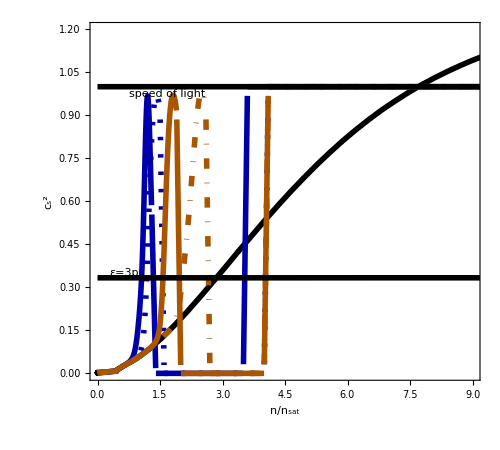

here

Part::partw: Part {1,3,7,8,9,15,20,21,25,26,27,30,31,32,33,34,35,36,38,41,44} of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
tw1=csthird[cs2low,1,0.1,{1.3,3.5},0.1,0.1,-0.65,0.1,1.2,1.]
tw2=csthird[cs2low,1.2,0.1,{1.5,4},0.1,0.1,-0.65,0.3,1.4,1.]
tw3=csthird[cs2low,1.6,0.1,{1.9,4},0.1,0.1,-0.65,0.3,1.8,1.]
tw4=csthird[cs2low,2,0.1,{2.6,4},0.1,0.1,-0.65,0.3,2.5,1.]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
mrtest=wraperTW["TW/low_n_peak1st",{tw1,tw2,tw3,tw4}];
```

```mathematica
(*first run
tw1=cs0[cs2low,1,0.1,{1.3,3.5},0.1,0.1,-0.5,0.1,1.2,1.]
tw2=cs0[cs2low,1.2,0.1,{1.5,4},0.1,0.1,-0.5,0.3,1.4,1.]
tw3=cs0[cs2low,1.6,0.1,{1.9,4},0.1,0.1,-0.5,0.3,1.8,1.]
tw4=cs0[cs2low,2,0.1,{2.6,4},0.1,0.1,-0.5,0.3,2.5,1.]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]*)
```

### endpoint of cs=0

```mathematica
cs0[cs2nint_,tr_,b_,ns_,dn_,dn2_,mag_,width_,off_,cmax_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,fout,m,bb,x1,x2,y1,y2,mb,bbb,x1b,x2b,y1b,y2b},

fun[x_]:=1/3.-mag*Exp[-(x-off)^2/width^2];
y1=fun[ns[[1]]];
x1=ns[[1]];
x2=ns[[1]]+dn;
m=-y1/dn;
bb=-m*x2;


mb=cmax/dn2;
bbb=-mb*ns[[2]];

c1[x_]:=s[x,tr,b] fun[x]+(1-s[x,tr,b])*cs2nint[x];

c2[x_]:=Which[x≤ ns[[1]],c1[x],ns[[1]]<  x< (ns[[1]]+dn),m*x+bb,(ns[[1]]+dn)≤ x≤ ns[[2]],0.0001,ns[[2]]< x≤( ns[[2]]+dn2),mb*x+bbb,x> (ns[[2]]+dn2),cmax];
Return[c2];
]
```

c2$377864

c2$377865

c2$377866

c2$377867

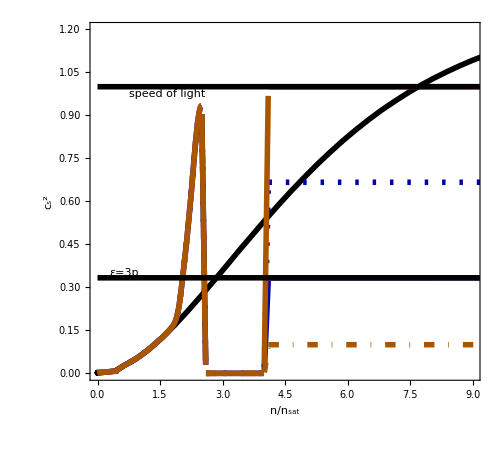

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/TW/endpoint already exists.

here

InterpolatingFunction::dmval: Input value {5858.04} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {6137.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {6415.95} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Part::partw: Part {1,3,7,8,9,15,20,21,25,26,27,30,31,32,33,34,35,36,38,41,44} of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
tw1=cs0[cs2low,2.,0.1,{2.5,4.},0.1,0.1,-0.6,0.3,2.5,1./3]
tw2=cs0[cs2low,2.,0.1,{2.5,4.},0.1,0.1,-0.6,0.3,2.5,2./3]
tw3=cs0[cs2low,2.,0.1,{2.5,4.},0.1,0.1,-0.6,0.3,2.5,1.]
tw4=cs0[cs2low,2.,0.1,{2.5,4.},0.1,0.1,-0.6,0.3,2.5,0.1]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/endpoint",{tw1,tw2,tw3,tw4}]
```

### slant endpoint of cs=0

c2$419262

c2$419263

c2$419264

c2$419265

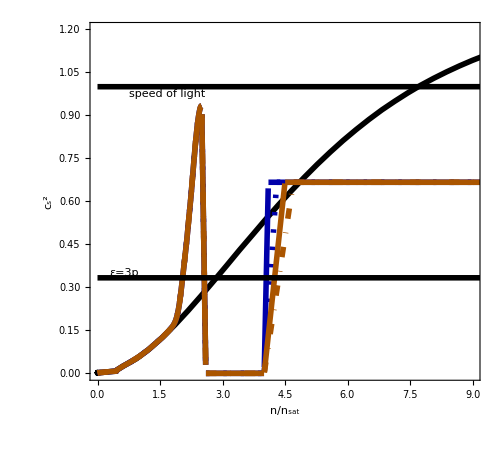

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/TW/slantendpoint already exists.

here

Part::partw: Part {1,3,7,8,9,15,20,21,25,26,27,30,31,32,33,34,35,36,38,41,44} of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
tw1=cs0[cs2low,2.,0.1,{2.5,4.},0.1,0.1,-0.6,0.3,2.5,2./3]
tw2=cs0[cs2low,2.,0.1,{2.5,4.},0.1,0.3,-0.6,0.3,2.5,2./3]
tw3=cs0[cs2low,2.,0.1,{2.5,4.},0.1,0.5,-0.6,0.3,2.5,2./3]
tw4=cs0[cs2low,2.,0.1,{2.5,4.},0.1,0.7,-0.6,0.3,2.5,2./3]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/slantendpoint",{tw1,tw2,tw3,tw4}]
```

### peak width of cs=0

```mathematica
cs0[cs2nint_,tr_,b_,ns_,dn_,dn2_,mag_,width_,off_,cmax_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,fout,m,bb,x1,x2,y1,y2,mb,bbb,x1b,x2b,y1b,y2b,c0},

fun[x_]:=1/3.-mag*Exp[-(x-off)^2/width^2];
c0=0.001;
y1=fun[ns[[1]]];
x1=ns[[1]];
x2=ns[[1]]+dn;
m=(c0-y1)/dn;
bb=c0-m*x2;


mb=cmax/dn2;
bbb=-mb*ns[[2]];

c1[x_]:=s[x,tr,b] fun[x]+(1-s[x,tr,b])*cs2nint[x];
c2[x_]:=Which[x≤ ns[[1]],c1[x],ns[[1]]<  x< (ns[[1]]+dn),m*x+bb,(ns[[1]]+dn)≤ x≤ ns[[2]],c0,ns[[2]]< x≤( ns[[2]]+dn2),mb*x+bbb,x> (ns[[2]]+dn2),cmax];
Return[c2];
]
```

c2$539921

c2$539922

c2$539923

c2$539924

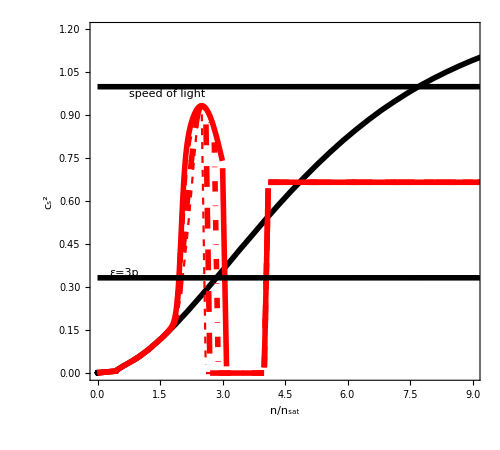

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/TW/peakwidth already exists.

here

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
tw4=cs0[cs2low,2,0.1,{2.5,4},0.1,0.1,-0.6,0.3,2.5,2./3]
tw2=cs0[cs2low,2,0.1,{2.6,4},0.1,0.1,-0.6,0.4,2.5,2./3]
tw3=cs0[cs2low,2,0.1,{2.8,4},0.1,0.1,-0.6,0.7,2.5,2./3]
tw1=cs0[cs2low,2,0.1,{3,4},0.1,0.1,-0.6,0.8,2.5,2./3]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/peakwidth",{tw1,tw2,tw3,tw4}]
```

Test with cs2=0 same length of period

c2$312559

c2$312560

c2$312561

c2$312562

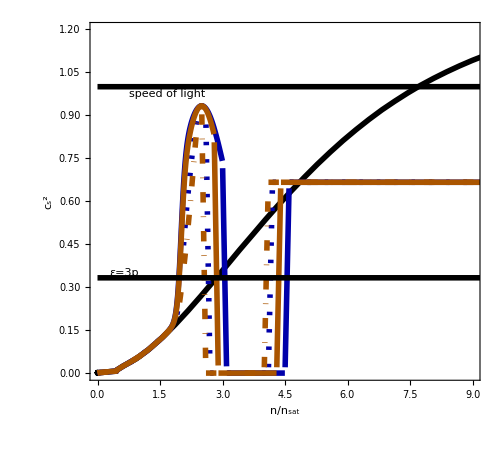

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/TW/peakwidthFIXL already exists.

here

Part::partw: Part {1,3,7,8,9,15,20,21,25,26,27,30,31,32,33,34,35,36,38,41,44} of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
tw4=cs0[cs2low,2,0.1,{2.5,4},0.1,0.1,-0.6,0.3,2.5,2./3]
tw2=cs0[cs2low,2,0.1,{2.6,2.6+1.5},0.1,0.1,-0.6,0.4,2.5,2./3]
tw3=cs0[cs2low,2,0.1,{2.8,2.8+1.5},0.1,0.1,-0.6,0.7,2.5,2./3]
tw1=cs0[cs2low,2,0.1,{3,4.5},0.1,0.1,-0.6,0.8,2.5,2./3]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/peakwidthFIXL",{tw1,tw2,tw3,tw4}]
```

```mathematica
Select[edconv*scale*a[[All,2]],(0.000186747182283805-0.0000001)<#<(0.000186747182283805+0.0000001)&]
```

{0.000186707,0.000186747,0.000186747,0.000186751,0.000186754,0.000186757,0.000186761,0.000186764,0.000186768,0.000186771,0.000186774,0.000186778,0.000186781,0.000186785,0.000186788,0.000186792,0.000186795,0.000186799,0.000186802,0.000186806,0.000186809,0.000186812,0.000186816,0.000186819,0.000186823,0.000186826,0.00018683,0.000186833,0.000186837,0.000186841,0.000186844}

```mathematica
ConvertInterpolate[tabMeVfm3_]:=Module[{entab,enint,e0},
entab=Table[{edconv*scale*tabMeVfm3[[i,2]],edconv*scale*tabMeVfm3[[i,3]]},{i,Length[tabMeVfm3]}]; (* table of energy density in terms of pressure *)
e0=DeleteDuplicatesBy[entab,First];

enint=Interpolation[e0,InterpolationOrder->1]; (*interpolation function, too high of order causes issues *)
Return[enint];
]
```

```mathematica
tw4=cs0[cs2low,2,0.1,{2.8,9},0.1,0.1,-0.6,0.7,2.5,2./3]
a=comblowden[sly,tw4,0.8]
out=ConvertInterpolate[a]
```

c2$575568

{{7.86638×10^-15,1.88644×10^-19,7.37866×10^-12,0.000753254,938.},{2.48757×10^-14,1.20285×10^-18,2.33334×10^-11,0.000753254,938.},{7.86638×10^-14,7.66973×10^-18,7.37866×10^-11,0.000753254,938.},9905,{7.9984,13702.7,22210.5,0.666667,4490.05},{7.9992,13705.1,22214.1,0.666667,4490.35}}
 |  |  |  |

InterpolatingFunction[…]

c2$239393

c2$239394

c2$239395

c2$239396

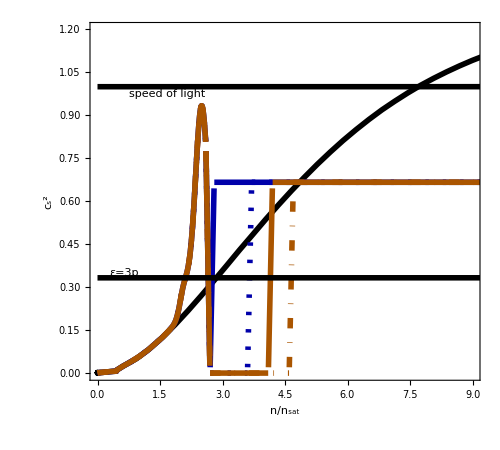

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/TW/pickFIX_PTwidth already exists.

here

Part::partw: Part {1,3,7,8,9,15,20,21,25,26,27,30,31,32,33,34,35,36,38,41,44} of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

-Graphics-

```mathematica
tw1=cs0[cs2low,2,0.1,{2.6,2.6+0.1},0.1,0.1,-0.6,0.2,2.5,2./3]
tw2=cs0[cs2low,2,0.1,{2.6,2.6+1.},0.1,0.1,-0.6,0.2,2.5,2./3]
tw3=cs0[cs2low,2,0.1,{2.6,2.6+1.5},0.1,0.1,-0.6,0.2,2.5,2./3]
tw4=cs0[cs2low,2,0.1,{2.6,2.6+2.},0.1,0.1,-0.6,0.2,2.5,2./3]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/pickFIX_PTwidth",{tw4,tw2,tw3,tw1}]
```

c2$10360

c2$10361

c2$10362

c2$10363

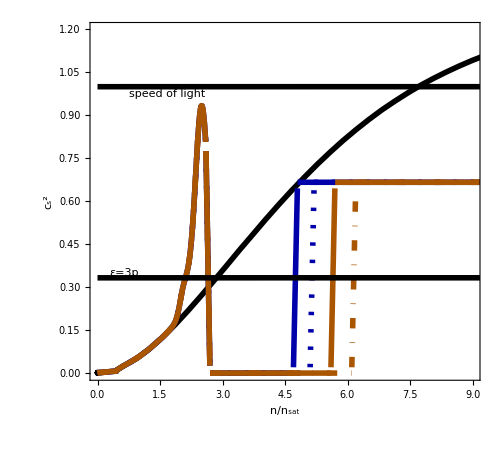

here

Part::partw: Part {1,3,7,8,9,15,20,21,25,26,27,30,31,32,33,34,35,36,38,41,44} of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

-Graphics-

```mathematica
tw1=cs0[cs2low,2,0.1,{2.6,2.6+2.1},0.1,0.1,-0.6,0.2,2.5,2./3]
tw2=cs0[cs2low,2,0.1,{2.6,2.6+2.5},0.1,0.1,-0.6,0.2,2.5,2./3]
tw3=cs0[cs2low,2,0.1,{2.6,2.6+3.},0.1,0.1,-0.6,0.2,2.5,2./3]
tw4=cs0[cs2low,2,0.1,{2.6,2.6+3.5},0.1,0.1,-0.6,0.2,2.5,2./3]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/pickFIX_PTwidth2",{tw4,tw2,tw3,tw1}]
```

c2$71308

c2$71309

c2$71310

c2$71311

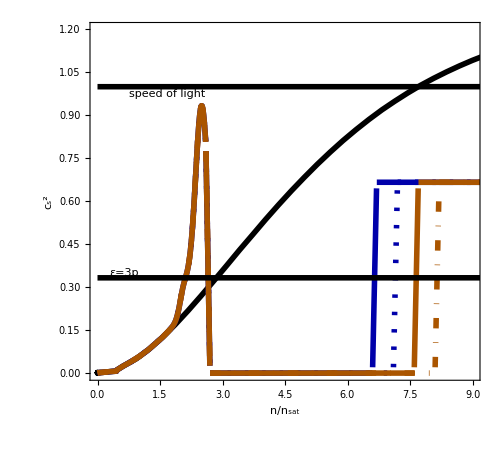

InterpolatingFunction::dmval: Input value {-0.000174516} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-0.000174516} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-0.00015844} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-0.00015844} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-0.000132376} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-0.000132376} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

here

Part::partw: Part {1,3,7,8,9,15,20,21,25,26,27,30,31,32,33,34,35,36,38,41,44} of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

-Graphics-

```mathematica
tw1=cs0[cs2low,2,0.1,{2.6,2.6+4.},0.1,0.1,-0.6,0.2,2.5,2./3]
tw2=cs0[cs2low,2,0.1,{2.6,2.6+4.5},0.1,0.1,-0.6,0.2,2.5,2./3]
tw3=cs0[cs2low,2,0.1,{2.6,2.6+5.},0.1,0.1,-0.6,0.2,2.5,2./3]
tw4=cs0[cs2low,2,0.1,{2.6,2.6+5.5},0.1,0.1,-0.6,0.2,2.5,2./3]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/pickFIX_PTwidth3",{tw4,tw2,tw3,tw1}]
```

c2$113044

c2$113045

c2$113046

c2$113047

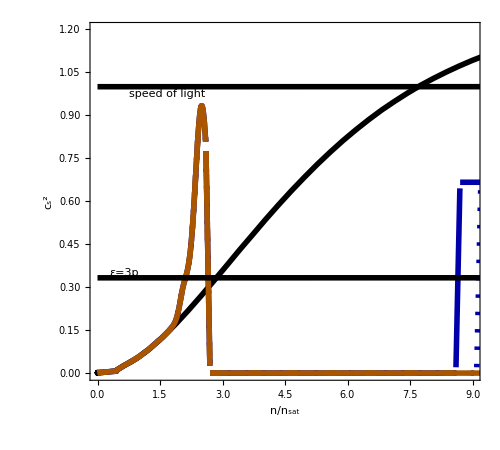

Interpolation::inddp: The point 0.000088412 in dimension 1 is duplicated.

$Aborted

```mathematica
tw1=cs0[cs2low,2,0.1,{2.6,2.6+6.},0.1,0.1,-0.6,0.2,2.5,2./3]
tw2=cs0[cs2low,2,0.1,{2.6,2.6+6.5},0.1,0.1,-0.6,0.2,2.5,2./3]
tw3=cs0[cs2low,2,0.1,{2.6,2.6+7.},0.1,0.1,-0.6,0.2,2.5,2./3]
tw4=cs0[cs2low,2,0.1,{2.6,2.6+7.5},0.1,0.1,-0.6,0.2,2.5,2./3]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/pickFIX_PTwidth4",{tw4,tw2,tw3,tw1}]
```

c2$285084

c2$285085

c2$285086

c2$285087

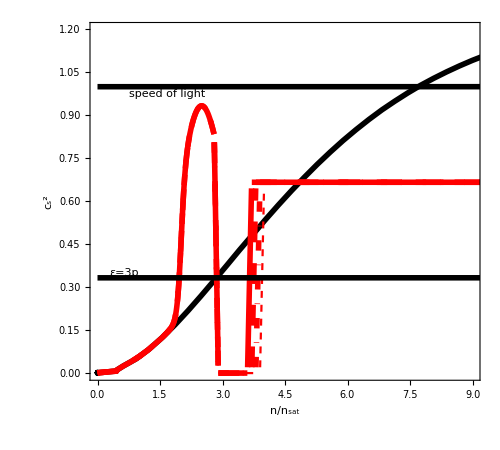

here

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
tw1=cs0[cs2low,2,0.1,{2.8,3.6},0.1,0.1,-0.6,0.7,2.5,2./3]
tw2=cs0[cs2low,2,0.1,{2.8,3.7},0.1,0.1,-0.6,0.7,2.5,2./3]
tw3=cs0[cs2low,2,0.1,{2.8,3.8},0.1,0.1,-0.6,0.7,2.5,2./3]
tw4=cs0[cs2low,2,0.1,{2.8,3.9},0.1,0.1,-0.6,0.7,2.5,2./3]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/checks",{tw4,tw2,tw3,tw1}]
```

```mathematica
6*10^6/30.
```

200000.

### 2 1 st order transitions

```mathematica
firsto2[cs2nint_,tr_,b_,ns_,dn_,dn2_,mag_,width_,off_,cmax_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,fout,m,bb,x1,x2,y1,y2,mb,bbb,x1b,x2b,y1b,y2b},

fun[x_]:=1/3.-mag*Exp[-(x-off)^2/width^2];
y1=fun[ns[[1]]];
x1=ns[[1]];
x2=ns[[1]]+dn;
m=-y1/dn;
bb=-m*x2;


mb=cmax[[1]]/dn2;
bbb=-mb*ns[[2]];

c1[x_]:=s[x,tr,b] fun[x]+(1-s[x,tr,b])*cs2nint[x];

c2[x_]:=Which[x≤ ns[[1]],c1[x],ns[[1]]<  x< (ns[[1]]+dn),m*x+bb,(ns[[1]]+dn)≤ x≤ ns[[2]],0.0001,ns[[2]]< x≤( ns[[2]]+dn2),mb*x+bbb,ns[[3]]>x> (ns[[2]]+dn2),cmax[[1]],ns[[3]]<=x<=ns[[4]],0.0001,x>ns[[4]],cmax[[2]]];
Return[c2];
]
```

c2$816992

c2$816993

c2$816994

c2$816995

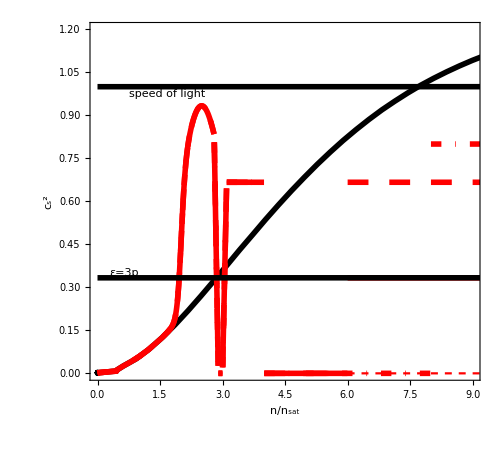

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/TW/2firstorder already exists.

here

InterpolatingFunction::dmval: Input value {6973.86} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7252.82} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7531.77} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
tw1=firsto2[cs2low,2,0.1,{2.8,3,4,6},0.1,0.1,-0.6,0.7,2.5,{2./3,1./3}]
tw2=firsto2[cs2low,2,0.1,{2.8,3,4,6},0.1,0.1,-0.6,0.7,2.5,{2./3,2./3}]
tw3=firsto2[cs2low,2,0.1,{2.8,3,4,8},0.1,0.1,-0.6,0.7,2.5,{2./3,0.8}]
tw4=firsto2[cs2low,2,0.1,{2.8,3,4,10},0.1,0.1,-0.6,0.7,2.5,{2./3,1}]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/2firstorder",{tw1,tw2,tw3,tw4}]
```

c2$858401

c2$858402

c2$858403

c2$858404

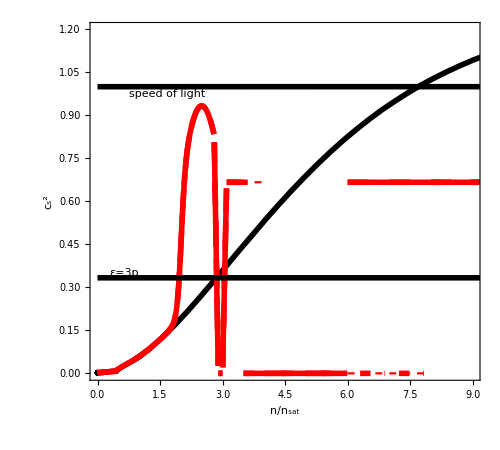

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/TW/2FO_long1 already exists.

here

InterpolatingFunction::dmval: Input value {21312.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {22427.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23543.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
tw1=firsto2[cs2low,2,0.1,{2.8,3,3.5,6},0.1,0.1,-0.6,0.7,2.5,{2./3,2./3}]
tw2=firsto2[cs2low,2,0.1,{2.8,3,4,6},0.1,0.1,-0.6,0.7,2.5,{2./3,2./3}]
tw3=firsto2[cs2low,2,0.1,{2.8,3,3.5,8},0.1,0.1,-0.6,0.7,2.5,{2./3,2./3}]
tw4=firsto2[cs2low,2,0.1,{2.8,3,4,8},0.1,0.1,-0.6,0.7,2.5,{2./3,2./3}]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/2FO_long1",{tw1,tw2,tw3,tw4}]
```

c2$899794

c2$899795

c2$899796

c2$899797

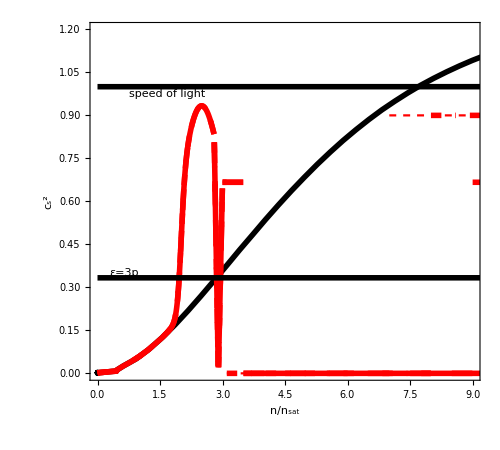

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/TW/2FO_short already exists.

here

InterpolatingFunction::dmval: Input value {14617.2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {15733.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {16848.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
tw1=firsto2[cs2low,2,0.1,{2.8,2.9,3.5,10},0.1,0.1,-0.6,0.7,2.5,{2./3,2./3}]
tw2=firsto2[cs2low,2,0.1,{2.8,2.9,3.5,9},0.1,0.1,-0.6,0.7,2.5,{2./3,2./3}]
tw3=firsto2[cs2low,2,0.1,{2.8,2.9,3.1,8},0.1,0.1,-0.6,0.7,2.5,{2./3,0.9}]
tw4=firsto2[cs2low,2,0.1,{2.8,2.9,3.1,7},0.1,0.1,-0.6,0.7,2.5,{2./3,0.9}]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/2FO_short",{tw1,tw2,tw3,tw4}]
```

c2$941203

c2$941204

c2$941205

c2$941206

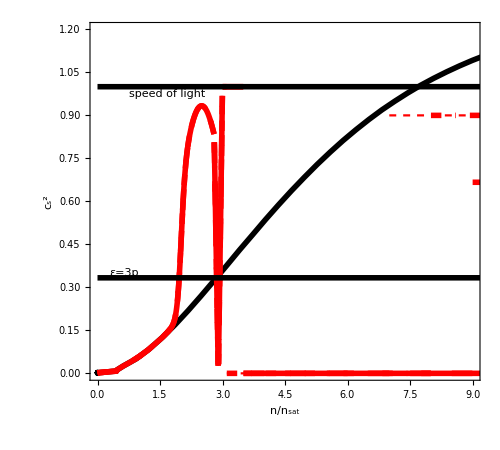

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/TW/2FO_high already exists.

here

InterpolatingFunction::dmval: Input value {15733.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {16848.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {17964.7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
tw1=firsto2[cs2low,2,0.1,{2.8,2.9,3.5,10},0.1,0.1,-0.6,0.7,2.5,{1.,2./3}]
tw2=firsto2[cs2low,2,0.1,{2.8,2.9,3.5,9},0.1,0.1,-0.6,0.7,2.5,{1.,2./3}]
tw3=firsto2[cs2low,2,0.1,{2.8,2.9,3.1,8},0.1,0.1,-0.6,0.7,2.5,{1.,0.9}]
tw4=firsto2[cs2low,2,0.1,{2.8,2.9,3.1,7},0.1,0.1,-0.6,0.7,2.5,{1.,0.9}]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/2FO_high",{tw1,tw2,tw3,tw4}]
```

### 2 1 st order transitions+2nd peak

```mathematica
c12[x_]:=s[x,6,0.5] 1./3 +(1-s[x,6,0.5])*Exp[-(x-6)^2/0.5^2];
```

```mathematica
firsto2[cs2nint_,tr_,b_,ns_,dn_,dn2_,mag_,width_,off_,cmax_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,fout,m,bb,x1,x2,y1,y2,mb,bbb,x1b,x2b,y1b,y2b,fun2},

fun[x_]:=1/3.-mag[[1]]*Exp[-(x-off)^2/width[[1]]^2];
y1=fun[ns[[1]]];
x1=ns[[1]];
x2=ns[[1]]+dn;
m=-y1/dn;
bb=-m*x2;


mb=cmax[[1]]/dn2;
bbb=-mb*ns[[2]];

c1[x_]:=s[x,tr,b] fun[x]+(1-s[x,tr,b])*cs2nint[x];

(*fun2[x_]:=s[x,ns[[4]],width[[2]]]*cmax[[2]] +(1-s[x,ns[[4]],width[[2]]])*mag[[2]]*Exp[-(x-ns[[4]])^2/width[[2]]^2];*)
fun2[x_]:=width[[2]]*(x-ns[[4]]-2)HeavisideTheta[(x-ns[[4]]-2)]+cmax[[2]];


c2[x_]:=Which[x≤ ns[[1]],c1[x],ns[[1]]<  x< (ns[[1]]+dn),m*x+bb,(ns[[1]]+dn)≤ x≤ ns[[2]],0.0001,ns[[2]]< x≤( ns[[2]]+dn2),mb*x+bbb,ns[[3]]>x> (ns[[2]]+dn2),cmax[[1]],ns[[3]]<=x≤(ns[[4]]-0*width[[2]]),0.0001,x>(ns[[4]]-0*width[[2]]),If[fun2[x]>1,1,fun2[x]]];
Return[c2];
]
```

c2$982597

c2$982598

c2$982599

c2$982600

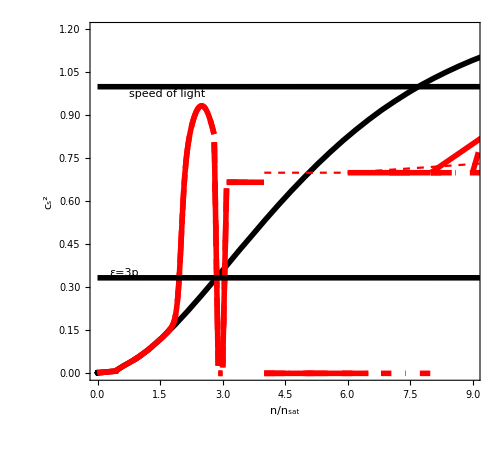

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/TW/2FO_2peak already exists.

here

InterpolatingFunction::dmval: Input value {50323.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {51439.2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {52555.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
tw1=firsto2[cs2low,2,0.1,{2.8,3,4,6},0.1,0.1,{-0.6,0.1},{0.7,0.1},2.5,{2./3,0.7}]
tw2=firsto2[cs2low,2,0.1,{2.8,3,4,7},0.1,0.1,{-0.6,0.05},{0.7,0.5},2.5,{2./3,0.7}]
tw3=firsto2[cs2low,2,0.1,{2.8,3,4,8},0.1,0.1,{-0.6,0.01},{0.7,0.7},2.5,{2./3,0.7}]
tw4=firsto2[cs2low,2,0.1,{2.8,3,4,4},0.1,0.1,{-0.6,0.5},{0.7,0.01},2.5,{2./3,0.7}]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
ck=wraperTW["TW/2FO_2peak",{tw1,tw2,tw3,tw4}]
```

```mathematica
firsto2[cs2nint_,tr_,b_,ns_,dn_,dn2_,mag_,width_,off_,cmax_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,fout,m,bb,x1,x2,y1,y2,mb,bbb,x1b,x2b,y1b,y2b,fun2},

fun[x_]:=1/3.-mag[[1]]*Exp[-(x-off)^2/width[[1]]^2];
y1=fun[ns[[1]]];
x1=ns[[1]];
x2=ns[[1]]+dn;
m=-y1/dn;
bb=-m*x2;


mb=cmax[[1]]/dn2;
bbb=-mb*ns[[2]];

c1[x_]:=s[x,tr,b] fun[x]+(1-s[x,tr,b])*cs2nint[x];

(*fun2[x_]:=s[x,ns[[4]],width[[2]]]*cmax[[2]] +(1-s[x,ns[[4]],width[[2]]])*mag[[2]]*Exp[-(x-ns[[4]])^2/width[[2]]^2];*)
fun2[x_]:=Which[(ns[[4]]+0.5)>x≥ ns[[4]],cmax[[2]],(ns[[4]]+1)≥ x≥ (ns[[4]]+0.5),0.0001,(ns[[4]]+1.5)> x> (ns[[4]]+1),cmax[[2]]+0.2,(ns[[4]]+2)≥ x≥ (ns[[4]]+1.5),0.0001,(ns[[4]]+2)< x,cmax[[2]]+0.4];


c2[x_]:=Which[x≤ ns[[1]],c1[x],ns[[1]]<  x< (ns[[1]]+dn),m*x+bb,(ns[[1]]+dn)≤ x≤ ns[[2]],0.0001,ns[[2]]< x≤( ns[[2]]+dn2),mb*x+bbb,ns[[3]]>x> (ns[[2]]+dn2),cmax[[1]],ns[[3]]<=x≤(ns[[4]]-0*width[[2]]),0.0001,x>(ns[[4]]-0*width[[2]]),If[fun2[x]>1,1,fun2[x]]];
Return[c2];
]
```

c2$1023990

c2$1023991

c2$1023992

c2$1023993

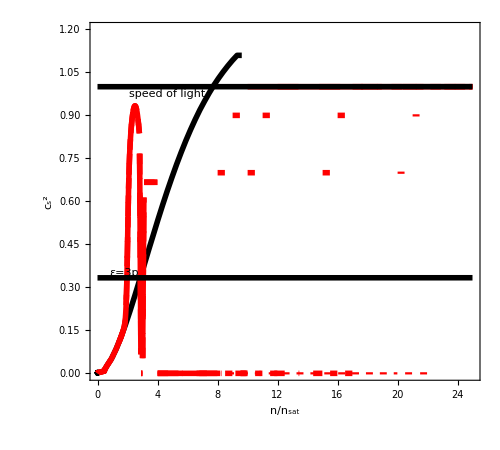

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/TW/2FO_steps already exists.

here

InterpolatingFunction::dmval: Input value {36933.6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {38049.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {39165.2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
tw1=firsto2[cs2low,2,0.1,{2.8,3,4,8},0.1,0.1,{-0.6,0.1},{0.7,0.1},2.5,{2./3,0.7}]
tw2=firsto2[cs2low,2,0.1,{2.8,3,4,10},0.1,0.1,{-0.6,0.05},{0.7,0.5},2.5,{2./3,0.7}]
tw3=firsto2[cs2low,2,0.1,{2.8,3,4,15},0.1,0.1,{-0.6,0.01},{0.7,0.7},2.5,{2./3,0.7}]
tw4=firsto2[cs2low,2,0.1,{2.8,3,4,20},0.1,0.1,{-0.6,0.5},{0.7,0.01},2.5,{2./3,0.7}]
csplotvar20[cs2low,{tw1,tw2,tw3,tw4}]
ck=wraperTW["TW/2FO_steps",{tw1,tw2,tw3,tw4}]
```

### width of cs=0

```mathematica
firsto2[cs2nint_,tr_,b_,ns_,dn_,dn2_,mag_,width_,off_,cmax_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,fout,m,bb,x1,x2,y1,y2,mb,bbb,x1b,x2b,y1b,y2b,fun2,c0},

fun[x_]:=1/3.-mag[[1]]*Exp[-(x-off)^2/width[[1]]^2];
c0=0.001;
y1=fun[ns[[1]]];
x1=ns[[1]];
x2=ns[[1]]+dn;
m=(c0-y1)/dn;
bb=c0-m*x2;


mb=cmax[[1]]/dn2;
bbb=-mb*ns[[2]];

c1[x_]:=s[x,tr,b] fun[x]+(1-s[x,tr,b])*cs2nint[x];

(*fun2[x_]:=s[x,ns[[4]],width[[2]]]*cmax[[2]] +(1-s[x,ns[[4]],width[[2]]])*mag[[2]]*Exp[-(x-ns[[4]])^2/width[[2]]^2];*)
fun2[x_]:=width[[2]]*(x-ns[[5]])HeavisideTheta[(x-ns[[5]])]+cmax[[2]];


c2[x_]:=Which[x≤ ns[[1]],c1[x],ns[[1]]<  x< (ns[[1]]+dn),m*x+bb,(ns[[1]]+dn)≤ x≤ ns[[2]],c0,ns[[2]]< x≤( ns[[2]]+dn2),mb*x+bbb,ns[[3]]>x> (ns[[2]]+dn2),c0,ns[[3]]<=x≤(ns[[4]]-0*width[[2]]),cmax[[1]],x>(ns[[4]]-0*width[[2]]),If[fun2[x]>1,1,fun2[x]]];
Return[c2];
]
```

c2$413194

c2$413195

c2$413196

c2$413197

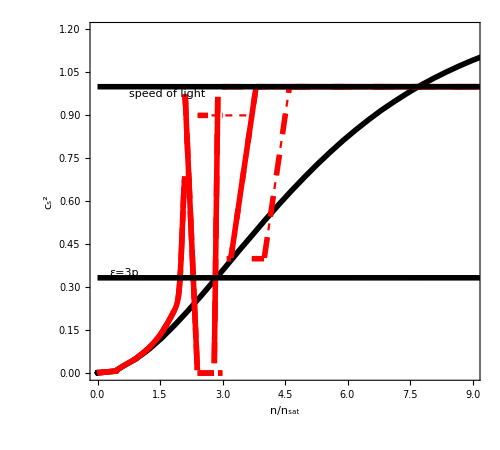

```mathematica
tw1=firsto2[cs2low,2.,0.4,{2.1,2.8,3.,3.1,3.2},0.3,0.09,{-0.65,1.},{0.1,0.99},2.1,{1.,0.4}]
tw2=firsto2[cs2low,2.,0.4,{2.1,2.8,3.,3.7,4.0},0.3,0.09,{-0.65,1.},{0.1,0.99},2.1,{1.,0.4}]
tw3=firsto2[cs2low,2.,0.4,{2.1,2.2,2.3,3.1,3.2},0.3,0.09,{-0.65,1.},{0.1,0.99},2.1,{0.9,0.4}]
tw4=firsto2[cs2low,2.,0.4,{2.1,2.2,2.3,3.7,4.0},0.3,0.09,{-0.65,1.},{0.1,0.99},2.1,{0.9,0.4}]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
(*wraperTW["TW/cs0high2FO",{tw1,tw2,tw3,tw4}]*)
```

```mathematica
(1./(6*10^22))^(-1/3)
```

3.91487×10^7

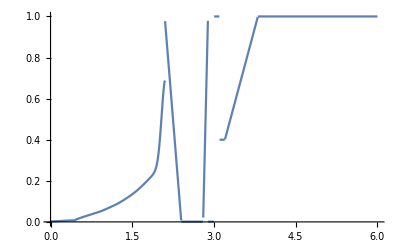

```mathematica
Plot[tw1[x],{x,0,6}]
```

```mathematica
cs0[cs2nint_,tr_,b_,ns_,dn_,dn2_,mag_,width_,off_,cmax_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,fout,m,bb,x1,x2,y1,y2,mb,bbb,x1b,x2b,y1b,y2b,c0},

fun[x_]:=1/3.-mag*Exp[-(x-off)^2/width^2];
c0=0.001;
y1=fun[ns[[1]]];
x1=ns[[1]];
x2=ns[[1]]+dn;
m=(c0-y1)/dn;
bb=c0-m*x2;


mb=cmax/dn2;
bbb=-mb*ns[[2]];

c1[x_]:=s[x,tr,b] fun[x]+(1-s[x,tr,b])*cs2nint[x];
Print[{ ns[[1]],(ns[[1]]+dn), ns[[2]],( ns[[2]]+dn2)}];
c2[x_]:=Which[x≤ ns[[1]],c1[x],ns[[1]]<  x< (ns[[1]]+dn),m*x+bb,(ns[[1]]+dn)≤ x≤ ns[[2]],c0,ns[[2]]< x≤( ns[[2]]+dn2),mb*x+bbb,x> (ns[[2]]+dn2),cmax];
Return[c2];
]
```

{2.5,2.6,6,6.1}

c2$10204

{2.6,2.9,3.5,3.59}

c2$10205

{2.6,3.1,3.5,4.5}

c2$10206

{2.6,2.9,3.5,4.5}

c2$10207

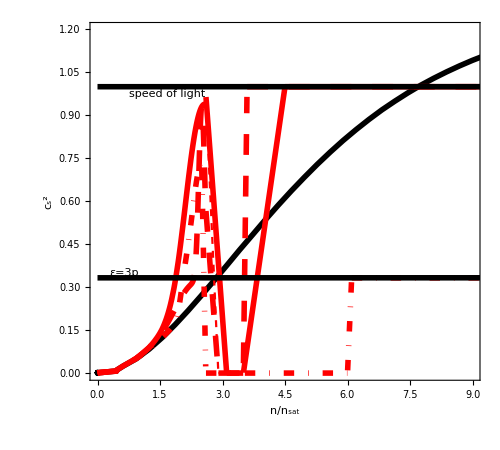

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/cs0high already exists.

here

InterpolatingFunction::dmval: Input value {4742.23} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5021.18} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5300.14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
tw1=cs0[cs2low,2,0.1,{2.5,6},0.1,0.1,-0.4,0.3,2.5,1./3]
tw2=cs0[cs2low,2,0.4,{2.6,3.5},0.3,0.09,-0.65,0.1,2.5,1.]
tw3=cs0[cs2low,2,0.4,{2.6,3.5},0.5,1.,-0.65,0.7,2.5,1.]
tw4=cs0[cs2low,2,0.4,{2.6,3.5},0.3,1.,-0.65,0.7,2.5,1.]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/cs0high",{tw1,tw2,tw3,tw4}]
```

{2.1,2.4,2.8,2.89}

c2$189114

{2.2,2.5,2.9,2.99}

c2$189115

{2.1,2.4,3.,3.09}

c2$189116

{2.1,2.4,3.5,3.59}

c2$189117

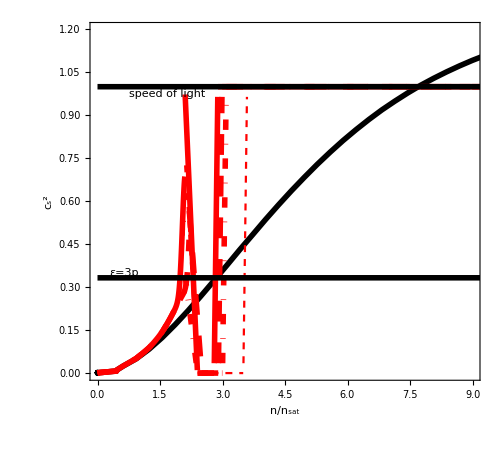

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/TW/highhyb already exists.

here

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
tw1=cs0[cs2low,2,0.4,{2.1,2.8},0.3,0.09,-0.65,0.1,2.1,1.]
tw2=cs0[cs2low,2,0.4,{2.2,2.9},0.3,0.09,-0.65,0.1,2.3,1.] 
tw3=cs0[cs2low,2,0.4,{2.1,3.0},0.3,0.09,-0.65,0.1,2.3,1.]
tw4=cs0[cs2low,2,0.4,{2.1,3.5},0.3,0.09,-0.4,0.1,2.1,1.]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/highhyb",{tw1,tw2,tw3,tw4}]
```

### 2 bumps

```mathematica
bump2[cs2nint_,tr_,b_,ns_,dn_,dn2_,mag_,width_,off_,cmax_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,fout,m,bb,x1,x2,y1,y2,mb,bbb,x1b,x2b,y1b,y2b,c0},

fun[x_]:=1/3.-mag*Exp[-(x-off)^2/width^2];
c0=0.001;
y1=fun[ns[[1]]];
x1=ns[[1]];
x2=ns[[1]]+dn;
m=(c0-y1)/dn;
bb=c0-m*x2;

c1[x_]:=s[x,tr,b] fun[x]+(1-s[x,tr,b])*cs2nint[x];

c2[x_]:=Which[x≤ ns[[1]],c1[x],ns[[1]]<  x< (ns[[1]]+dn),m*x+bb,(ns[[1]]+dn)≤ x≤ ns[[2]],c0,ns[[2]]< x≤ns[[3]],fun[x-(ns[[2]]+dn2)],x> ns[[3]],cmax];
Return[c2];
]
```

c2$55224

c2$55225

c2$55226

c2$55227

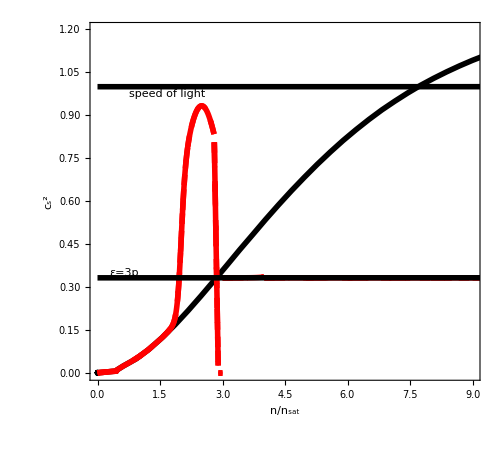

```mathematica
tw1=bump2[cs2low,2,0.1,{2.8,3,4},0.1,0.1,-0.6,0.7,2.5,1./3]
tw2=bump2[cs2low,2,0.1,{2.8,3,4},0.1,0.1,-0.6,0.7,2.5,1./3]
tw3=bump2[cs2low,2,0.1,{2.8,3,4},0.1,0.1,-0.6,0.7,2.5,1./3]
tw4=bump2[cs2low,2,0.1,{2.8,3,4},0.1,0.1,-0.6,0.7,2.5,1./3]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
(*wraperTW["TW/2bumps",{tw1,tw2,tw3,tw4}]*)
```

### Hybrids 2.5 Msun

```mathematica
tw1=cs0[cs2low,2,0.1,{2.8,3},0.1,0.1,-0.6,0.7,2.5,2./3]
tw2=cs0[cs2low,2,0.1,{2.8,3.5},0.1,0.1,-0.6,0.7,2.5,2./3]
tw3=cs0[cs2low,2,0.1,{2.8,8},0.1,0.1,-0.6,0.7,2.5,2./3]
tw4=cs0[cs2low,2,0.1,{2.8,9},0.1,0.1,-0.6,0.7,2.5,2./3]
csplotvar[cs2low,{tw1,tw2,tw3,tw4}]
wraperTW["TW/peakwide_longcs0",{tw4,tw2,tw3,tw1}]
```

```mathematica
ListPlot[c0mrk,PlotMarkers->{Automatic,Medium},PlotStyle->MyStyle[[1]]]
```

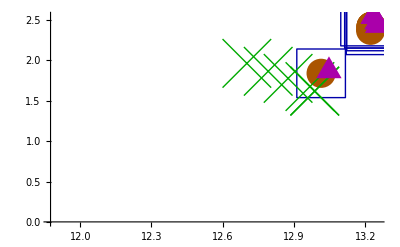

```mathematica
klist={2,5,7,9};
mark=ListPlot[{Join[hyb1[[3]],{{0.2,1.12}}],Join[hyb2[[3]],{{0.7,1.13}}],Join[hyb3[[3]],{{1.2,1.14}}],Join[hyb4[[3]],{{1.7,1.12}}]},PlotMarkers->{{"□",Offset[50]},{"●",Offset[30]},{"×",Offset[50]},{"▲",Offset[30]}},PlotStyle->MyStyle2[[{2,5,7,9}]]]
```

## Summary plots [only run after functional forms are generated]

### normal

#### functions

```mathematica
pMmax[mr_]:=pcen[[ Length[mr]]];
nBfind[eossub_]:=Interpolation[Table[{eossub[[i,2]],eossub[[i,1]]},{i,Length[eossub]}]];
nBmax[mr_,eos_]:=Module[{pM,fun,mc},
mc=mcut[mr];
pM=mc[[ Length[mc],4]];
fun=nBfind[eos];
Return[fun[pM]];
]
cout[cstab_,nb_]:=Module[{int},
int=Interpolation[cstab,InterpolationOrder->1];
Return[{{nb,int[nb]}}];
]
cspoint[dat_,nblist_]:=Module[{tab,out},
tab=Delete[dat,1];

out=Table[cout[tab[[i]],nblist[[i]]],{i,Length[nblist]}];
Return[out];
]
```

```mathematica
fname={"2bumpsfat","endpoint","adjustedwidth","peaklocation"}
```

{2bumpsfat,endpoint,adjustedwidth,peaklocation}

```mathematica
lamPlot[name_]:=Module[{in,out},
in=Table[Import[StringJoin["output_files/",name,"/eos",ToString[n],"_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"]][[All,{3,6}]],{n,4}];
out=Show[{lamERR,ListLogPlot[in,Joined->True,PlotStyle->MyStyle2[[{2,5,7,9}]]],txt["GW170817",0.02,0.25],txt["(d)",0.8,0.9]}];

Return[out];
]
```

```mathematica
miniplots[n_]:=Module[{out,sout,plots,len,sub,eosin,mrin,all,eosall,mrall,mout,lines,psly,p1,p2,p3,p4,dat,fin,str,klist,nBlist,endpoints,mark},
Clear[all];
all=readin[fname[[n]] ];
fin=4*n;
str=fin-3;
klist={2,5,7,9};


eosall=all[[1]];
mrall=all[[2]];
mout=Table[mcut[mrall[[i]]][[All,1;;2]],{i,Length[mrall]}];
Print["mout"];
len=Length[eosall];

nBlist=Table[nBmax[mrall[[j]],eosall[[j]]]/nsat,{j,len}];
Print["nBlist"];



sub[eossub_]:=Table[{gcm3toMeVfm3*eossub[[i,3]],1.6022*10^33*eossub[[i,2]]},{i,Length[eossub]}];
out=Table[sub[eosall[[j]]],{j,len}];
Print["ready to plot"];

p1=Show[{LIGO,ListLogLogPlot[out,AspectRatio->0.9,PlotStyle->MyStyle2[[klist]],Joined->True],txt["GW170817 Spec EoS",0.5,0.93],txt["(b)",0.9,0.1]}];

lines=Plot[{2.5+0.00001x,2.67+0.00001x},{x,0,30},PlotStyle->MyStyle[[{1,1,2,3,4,5,6}]],Filling->{1->{2}}];
p2=Show[{ListPlot[mout,AspectRatio->0.9,PlotRange->{{10,16},{0.5,3.1}},PlotStyle->MyStyle2[[klist]],FrameLabel->{Style["R [km]",20],Style["M [M_⊙]",20]},ImageSize->500,Frame->True,Joined->True,LabelStyle->Directive[20]],lines,Ligoplot,txt["J0740+6620",0.45,0.6],txt["GW190814",0.05,0.8],txt["GW170817",0.1,0.4],txt["J0030+0451",0.7,0.42],txt["(c)",0.9,0.1]}];

dat=Join[{cs2sly},csprint[eosall]];

endpoints=cspoint[dat,nBlist];

psly=ListLinePlot[csprint[eosall],PlotRange->{{0,9},{0,1.2}},AspectRatio->0.9,PlotStyle->MyStyle2[[klist]],FrameLabel->{Style["n_B/n_sat",20],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]];
lines=Plot[{1/3+0.00001x,1+0.00001x},{x,0,10},PlotStyle->MyStyle[[{1,1}]]];
mark=ListPlot[Join[endpoints,{{{2,1.15}}},{{{2.5,1.15}}},{{{3,1.15}}},{{{3.5,1.15}}}],PlotMarkers->{{"□",Offset[50]},{"●",Offset[30]},{"×",Offset[50]},{"▲",Offset[30]}},PlotStyle->MyStyle2[[klist]]];
p3=Show[Flatten[{psly,lines,txt["ε=3p",0.02,0.3],txt["causal limit",0.02,0.86],mark,txt["max central n_B/n_sat",0.47,0.96],txt["(a)",0.9,0.1]}],leg4[{"eos1","eos2","eos3","eos4"},{0,0.10,0.12}+0.7,{0.5,0.4,0.3,0.2,0.1}+0.2,MyStyle2[[klist]]]];
p4=lamPlot[fname[[n]]];

Export[StringJoin["output_files/",fname[[n]],"_stupidunitsplot.pdf"],p1];
Export[StringJoin["output_files/",fname[[n]],"_mrplot.pdf"],p2];
Export[StringJoin["output_files/",fname[[n]],"_cs2plot.pdf"],p3];
Export[StringJoin["output_files/",fname[[n]],"_LAMplot.pdf"],p4];


Return[{p1,p2,p3,p4}];
]
```

#### plots

```mathematica
0.1/3*100
(2.2-2.1)/2.2*100
(12.08-11.48)/12.08*100
(14.3-14.18)/14.3*100
```

3.33333

4.54545

4.96689

0.839161

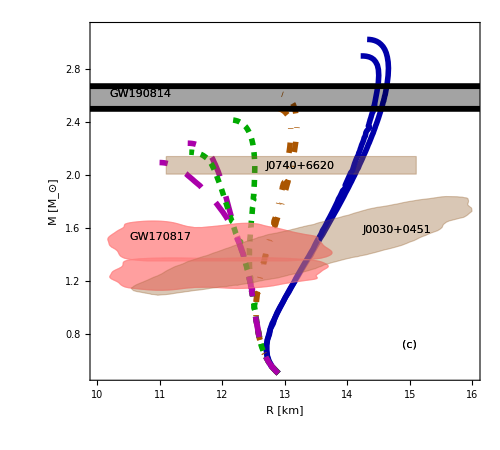

```mathematica
Show[{bump[[2]],b2[[2]]}]
```

```mathematica
fname
```

{2bumpsfat,endpoint,adjustedwidth,peaklocation}

mout

nBlist

ready to plot

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

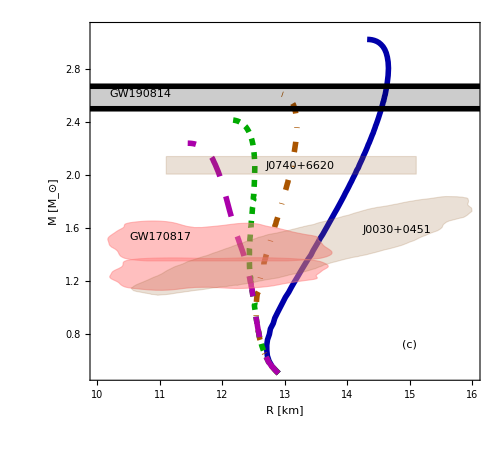
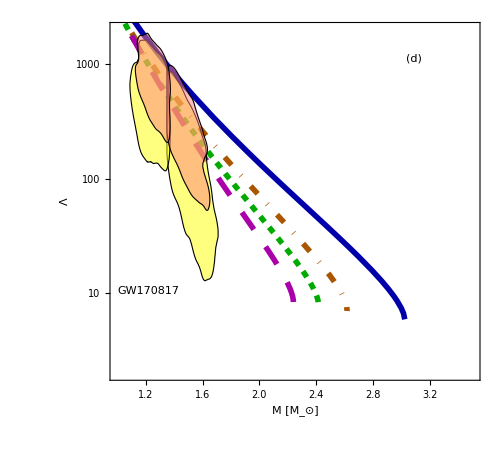
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
bump=miniplots[7]
```

```mathematica
For[ik=1,ik≤Length[fname],ik++,
miniplots[ik];
]
```

mout

nBlist

ready to plot

mout

nBlist

ready to plot

mout

nBlist

ready to plot

mout

nBlist

ready to plot

### twins

#### functions

```mathematica
(*TWname={"TW/sly","TW/cs0","TW/peak","TW/endpoint","TW/slantendpoint","TW/peakwidth","TW/peakwide_longcs0","TW/2firstorder","TW/2FO_long1","TW/2FO_short","TW/2FO_high","TW/2FO_2peak","TW/2FO_steps","TW/peakwidth","TW/cs0high","TW/highhyb","TW/cs0high2FO","TW/peakwidthFIXL","TW/hybs","TW/Blat_repeat","TW/Blat_repeat"}*)
TWname={"TW/endpoint","TW/slantendpoint","TW/peakwidthFIXL","TW/hybs","TW/pickFIX_PTwidth","TW/pickFIX_PTwidth2","TW/pickFIX_PTwidth3"}
```

{TW/endpoint,TW/slantendpoint,TW/peakwidthFIXL,TW/hybs,TW/pickFIX_PTwidth,TW/pickFIX_PTwidth2,TW/pickFIX_PTwidth3}

```mathematica
mcut2[mr0_]:=Module[{MM,pos,mout,mr,mout2},
mr=mr0;
MM=Table[{If[mr[[i-1,2]]<=mr[[i,2]]||mr[[i+1,2]]>=mr[[i,2]],mr[[i,1]],Nothing],If[mr[[i-1,2]]<=mr[[i,2]]||mr[[i+1,2]]>=mr[[i,2]],mr[[i,2]],Nothing],If[mr[[i-1,2]]<=mr[[i,2]]||mr[[i+1,2]]>=mr[[i,2]],mr[[i,5]],Nothing]},{i,2,Length[mr]-1}];
mout=Select[Split[MM,UnsameQ[#,{}]&],UnsameQ[#,{{}}]&]//.{}->Sequence[];


mout2=Select[mout,Length[#]>2&];


(*Return[Select[MM,#[[2]]>0.3&]];*)
Return[mout2];
]

mp[mr_]:=Module[{len,mas,mprev,i,mas2,mr2,mn,rad,rad2,rprev},

len=Length[mr];
mr2=mr;
For[i=2,i≤len,i++,
mas=mr2[[i,2]];
mprev=mr2[[i-1,2]];
(*mn=If[i+1≤len, mr2[[i+1,2]],0];*)
mas2=If[mas>0.5&& mas>(mprev+0.5),200,mas];
rad=mr2[[i,1]];
rprev=mr2[[i-1,1]];
rad2=If[mas>0.5&& rad>(rprev+0.5)||rad<(rprev-0.5),200,rad];
(*If[mas≠ mas2,Print[{mas,mas2}]];*)
(*mr[[i,2]]=mas2;*)
mr2=ReplacePart[mr2,{i,2}->mas2];
mr2=ReplacePart[mr2,{i,1}->rad2];
(*If[mas≠ mas2,Print[mr2[[i,2]]]];*)
];
Print[{"mp=",Select[mr2,#[[2]]≠ 200&&#[[1]]≠ 200&]}];
Return[Select[mr2,#[[2]]≠ 200&&#[[1]]≠ 200&]];
]
```

```mathematica
mprune[mr0_]:=Module[{N,mout,nmax,last,Mmax},
N=Length[mr0];
mout=Table[mr0[[i,All,1;;2]],{i,N}];
Print[{"mout",mout}];
last=Table[Length[mr0[[i]]],{i,N}];
Print[{"lasts",last}];
Print[mr0];
nmax=Table[mr0[[i,last[[i]],3]],{i,N}];
Print["hereD"];
Mmax=Table[mr0[[i,last[[i]],{2,1}]],{i,N}];
Print[Mmax];
Return[{mout,nmax,Mmax}];
]
```

```mathematica
cs1PT[eos_]:=Module[{tab,split,min,max},
tab=Select[Table[{eos[[i,1]]/nsat,eos[[i,4]]},{i,Length[eos]}],#[[1]]>2&&#[[2]]<0.01&][[All,1]];
split=Split[tab,#2-#1<0.1&];
min=Table[Min[split[[i]]],{i,Length[split]}];
max=Table[Max[split[[i]]],{i,Length[split]}];


Return[{min,max}];
]
```

```mathematica
ptmark[mr_,min_,max_]:=Module[{mrl,mrl2,out,mrlmid},


mrl=Select[Flatten[Table[{mr[[i,1]],mr[[i,2]],If[min[[j]]> mr[[i-1,5]]&& max[[j]]≤ mr[[i,5]],1,0]},{i,2,Length[mr]},{j,Length[min]}],1],#[[3]]==1&][[All,1;;2]];

mrl2=Select[Flatten[Table[{mr[[i,1]],mr[[i,2]],If[min[[j]]> mr[[i,5]]&& max[[j]]≤ mr[[i+1,5]],1,0]},{i,1,Length[mr]-1},{j,Length[min]}],1],#[[3]]==1&][[All,1;;2]];
mrlmid=Flatten[Table[Select[mr,min[[x]]≤ #[[5]]<=max[[x]]&],{x,Length[min]}],1][[All,1;;2]];

out=Join[mrl2,mrl,mrlmid];

Return[out];
]
```

```mathematica
maxcut[list_,max_]:=Module[{pos,out,max2},
max2=Nearest[list[[All,1;;2]],max]; (*find nearest in lisst to the endd M-R*)
pos=Position[list[[All,1;;2]],max2[[1]] ][[1,1]]; (*find position of the last sstable M-R*)
out=list[[1;;pos]]; (* cut list at last stable M-R*)
Return[out];
]
```

```mathematica
lamPlot[name_,eosNuM_,sty_]:=Module[{in,inorg,out,split},
inorg=Import[StringJoin["output_files/",name,"/eos",ToString[eosNuM],"_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"]];

split= Select[Split[inorg,UnsameQ[#,{}]&],UnsameQ[#,{{}}]&]//.{}->Sequence[];

in=Table[split[[i]][[All,{3,6}]],{i,Length[split]}];
(*[[All,{3,6}]]*)
out=Show[{lamERR,ListLogPlot[in,Joined->True,PlotStyle->MyStyle2[[sty]]],txt["GW170817",0.02,0.27]}];

Return[out];
]
```

```mathematica
find0[eos_,mr_,cor_]:=Module[{out,csint,mrs,pt,cs0,o2,tab,pts,dots},

cs0=cs1PT[eos];
pt=ptmark[mr,cs0[[1]],cs0[[2]]];


csint=Interpolation[Table[{eos[[i,1]]/nsat,eos[[i,4]]},{i,Length[eos]}],InterpolationOrder->1];
(*Print[Plot[csint[x],{x,0.1,10},FrameLabel->{Style["n_B/n_sat",20],Style["c_s^2",20]},PlotStyle->MyStyle,ImageSize->500,Frame->True,LabelStyle->Directive[20],PlotRange->{{0,10},{0,1}}]];
Print[ListPlot[mr[[1;;300,{5,2}]],PlotMarkers->Automatic,PlotRange->{{0,10},{0.5,2.5}},PlotStyle->MyStyle,FrameLabel->{Style["n_B/n_sat",20],Style["M",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]]];
Print[ListPlot[mr[[1;;300,{5,1}]],PlotMarkers->Automatic,PlotRange->{{0,10},{8,15}},PlotStyle->MyStyle,FrameLabel->{Style["n_B/n_sat",20],Style["R",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]]];*)
mrs=Table[{mr[[i,1]],mr[[i,2]],csint[mr[[i,5]]]},{i,Length[mr]}];
(*Print[ListPlot[mrs[[1;;300,{2,3}]],Joined->True,PlotRange->All,FrameLabel->{Style["M",20],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]]];*)
out=ListLinePlot[{mrs[[1;;300,1;;2]],pt},PlotRange->{{8,14},{0.2,3}},PlotStyle->MyStyle2[[cor]],FrameLabel->{Style["R",20],Style["M",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]];

tab=Table[{eos[[i,1]]/nsat,eos[[i,4]]},{i,Length[eos]}];
o2=ListLinePlot[{tab,pt},PlotRange->{{0,5},{0,1}},PlotStyle->MyStyle2[[cor]],FrameLabel->{Style["n_B/n_sat",20],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]];

pts={0.3839999999999953,0.44799999999999396,0.4631999999999936,0.4791999999999933,0.4967999999999929,0.5119999999999926}/nsat;
dots=Table[near[mr,pts[[i]]],{i,Length[pts]}];
Return[{out,o2,dots}];
]
```

```mathematica
near[mr_,nb_]:=Module[{out,p,mrsub},

p=Nearest[mr[[All,5]],nb][[1]];

out=Flatten[Select[mr,#[[5]]==p&][[All,1;;2]],1];
Return[out];
]
```

```mathematica
csprint0[eos_]:=Interpolation[Table[{eos[[i,1]],eos[[i,4]]},{i,Length[eos]}],InterpolationOrder->1]
mplotcsnum[mra_,eos_,n_]:=Module[{mlis,pl,nb,cp,cpend,Mmax},


mlis= mprune[mcut2[mp[mra] ] ];
Print["herez"];
pl=ListLinePlot[ mlis[[1]],PlotStyle->MyStyle2[[{n,n}]],PlotRange->All  ];
Print["hereb"];
nb=mlis[[2]];
cp=csprint0[eos ];
Print["herecc"];
cpend=Table[{nb[[i]],N[cp[nb[[i]]]]},{i,Length[nb]}];
Print["hered"];
Mmax=mlis[[3]];
Print["heree"];
Return[{pl,cpend,Mmax}];
]
```

```mathematica
PTpts[eos_,mr_]:=Module[{cs0,pt},

cs0=cs1PT[eos];
pt=ptmark[mr,cs0[[1]],cs0[[2]]];
Return[pt];
]

notwinMR[lis_,mr_]:={mr[[1;;lis[[2]],1;;2]],mr[[lis[[2]];;Length[mr],1;;2]]};
twinMR[lis_,mr_]:={mr[[1;;lis[[2]],1;;2]],mr[[lis[[2]];;lis[[3]],1;;2]],mr[[lis[[3]];;lis[[4]],1;;2]],mr[[lis[[4]];;Length[mr],1;;2]]};


findbreak[eos_,mr_]:=Module[{max,min,all,pos,nbc,out,next,pos2,cslist,tout,mrout,lastI,pos1},
max=FindPeaks[mr[[All,2]]];
min=FindPeaks[-mr[[All,2]]];
all=Join[min,max];



pos1=Sort[all[[All,1]]];

pos=If[Length[pos1]≤5,pos1,pos1[[1;;5]]];
Print[pos];


lastI=Length[mr[[1]]];
Print[lastI];
nbc=mr[[pos,lastI]];

Print[Length[pos]];
mrout=If[Length[pos]≤3,notwinMR[pos,mr],twinMR[pos,mr]];


next=Flatten[Table[Nearest[eos[[All,1]],nsat*nbc[[i]]],{i,Length[nbc]}],1]; (*finds nearest nB from central density in EOS table*)
pos2=Flatten[Table[Position[eos[[All,1]],next[[i]]],{i,Length[next]}]]; (*locates position in EOS table*)
cslist=Delete[eos[[pos2]],1]; (*spits out EOS info at breaking points *)

tout=Table[Flatten[{cslist[[i,1]]/nsat,Delete[cslist[[i]],1]}],{i,Length[cslist]}]; (*renormalized to nB/nsat*)


Return[{tout,mrout}];
]
```

```mathematica
MRsOUT=ListLinePlot[mrsly[[All,1;;2]],PlotStyle->MyStyle[[1]],PlotRange->All];
```

```mathematica
TWplots[n_]:=Module[{out,sout,plots,len,sub,eosin,mrin,all,eosall,mrall,mout,lines,psly,p1,p2,p3,p2b,p4,dat,fin,str,klist,nBlist,endpoints,mark,stmax,nameouot,mt,mrout,pl1,pl2,pl3,pl4,mlis1,mlis2,mlis3,mlis4,allmrcs,mrpsub,cpend,mrasub,mrtab,mrlin,mrlin2,mrlina,MasMax,cpBreak,ssep,mrlina1,mrlina2,mrlina3,mrlina4,lamtab},
all=readin[TWname[[n]] ];
nameouot=TWname[[n]] ;

klist={2,5,7,9};



eosall=all[[1]];
mrall=all[[2]];





(*mrtab=Table[PTpts[eosall[[i]],mrall[[i]]],{i,4}];



allmrcs=Table[mplotcsnum[Select[mrall[[i]],#[[7]]<50&],eosall[[i]],klist[[i]]],{i,4}];



mrpsub=allmrcs[[All,1]];

cpend=Join[allmrcs[[All,2]]];

MasMax=Join[allmrcs[[All,3]]];*)


ssep=Table[findbreak[eosall[[i]],mrall[[i]]],{i,4}];
cpBreak=ssep[[All,1]];
mrlin=ssep[[All,2]];

mrlina1=ListLinePlot[mrlin[[1]],PlotStyle->{MyStyle2[[klist[[1]]  ]],Blue}];
mrlina2=ListLinePlot[mrlin[[2]],PlotStyle->{MyStyle2[[klist[[2]]  ]],Brown}];
mrlina3=ListLinePlot[mrlin[[3]],PlotStyle->{MyStyle2[[klist[[3]]  ]],Green}];
mrlina4=ListLinePlot[mrlin[[4]],PlotStyle->{MyStyle2[[klist[[4]]  ]],Purple}];

(*mrlin=ListLinePlot[mrlin[[1]],PlotStyle->{MyStyle2[[klist[[1]]  ]],Blue, Brown, Green, Red}];
mrlin2=ListLinePlot[mrall[[All,All,1;;2]],PlotStyle->MyStyle2[[klist]]];*)



Print[{"cp break",cpBreak}];

(*Print[{"cp end",cpend}];*)
len=Length[eosall];

(*csprint makes table of cs2 in the format that we want*)




sub[eossub_]:=Table[{gcm3toMeVfm3*eossub[[i,3]],1.6022*10^33*eossub[[i,2]]},{i,Length[eossub]}];
out=Table[sub[eosall[[j]]],{j,len}];

sout=Table[{gcm3toMeVfm3*sly[[i,3]],1.6022*10^33*sly[[i,2]]},{i,Length[sly]}];


p1=Show[{LIGO,ListLogLogPlot[out,AspectRatio->0.9,PlotStyle->MyStyle2[[klist]],Joined->True],txt["GW170817 Spec EoS",0.5,0.93],txt["(b)",0.9,0.1]}];

(*mrall=Join[{mrsly[[All,1;;2]]},mout[[All,All,1;;2]]];*)
lines=Plot[{2.5+0.00001x,2.67+0.00001x},{x,0,30},PlotStyle->MyStyle[[{1,1,3,4,7}]],Filling->{1->{2}}];
(*p2=Show[{ListLinePlot[{0,0},AspectRatio->0.9,PlotRange->{{9,14},{0.5,2.7}},PlotStyle->MyStyle2[[klist]],FrameLabel->{Style["R [km]",20],Style["M [M_⊙]",20]},Joined->True,ImageSize->500,Frame->True,LabelStyle->Directive[20]],mrlin[[1]],mrlin[[2]],mrlin[[3]],mrlin[[4]],lines,txt["GW170817",0.37,0.45],txt["J0030+0451",0.45,0.33],txt["J0740+6620",0.58,0.71],txt["GW190814",0.1,0.95],Ligoplot}]; (*this one!!*) *)


(*mrasub=Table[Select[mrall[[i]],#[[5]]<25&][[All,1;;2]],{i,4}];*)


(*p2b=Show[{ListLinePlot[{0,0},AspectRatio->0.9,PlotRange->{{10,17},{0.5,2.7}},PlotStyle->MyStyle2[[klist]],FrameLabel->{Style["R [km]",20],Style["M [M_⊙]",20]},Joined->True,ImageSize->500,Frame->True,LabelStyle->Directive[20]],Ligoplot,mrlin,mrpsub[[1]],mrpsub[[2]],mrpsub[[3]],mrpsub[[4]],lines,txt["GW170817",0.28,0.45],txt["J0030+0451",0.3,0.33],txt["J0740+6620",0.4,0.71],txt["GW190814",0.1,0.95],MRsOUT}]; (*this one!!*) *)
p2b=Show[{ListLinePlot[{0,0},AspectRatio->0.9,PlotRange->{{10,14},{0.5,2.7}},PlotStyle->MyStyle2[[klist]],FrameLabel->{Style["R [km]",20],Style["M [M_⊙]",20]},Joined->True,ImageSize->500,Frame->True,LabelStyle->Directive[20]],Ligoplot,mrlina1,mrlina2,mrlina3,mrlina4,lines,txt["GW170817",0.18,0.45],txt["J0030+0451",0.74,0.57],txt["J0740+6620",0.6,0.71],txt["GW190814",0.1,0.95],txt["(c)",0.9,0.1]}];

p2=Show[{ListLinePlot[{0,0},AspectRatio->0.9,PlotRange->{{7,14},{0.5,2.7}},PlotStyle->MyStyle2[[klist]],FrameLabel->{Style["R [km]",20],Style["M [M_⊙]",20]},Joined->True,ImageSize->500,Frame->True,LabelStyle->Directive[20]],Ligoplot,mrlina1,mrlina2,mrlina3,mrlina4,lines,txt["GW170817",0.18,0.45],txt["J0030+0451",0.74,0.57],txt["J0740+6620",0.6,0.71],txt["GW190814",0.1,0.95],txt["(c)",0.9,0.1]}];



dat=Join[{cs2sly},csprint[eosall]];


(*endpoints=cspoint[dat,nBlist];*)

(*psly=ListLinePlot[csprint[eosall],PlotRange->{{0.5,4},{0,1.2}},AspectRatio->0.9,PlotStyle->MyStyle2[[klist]],FrameLabel->{Style["n_B/n_sat",20],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]];*)
psly=ListLinePlot[csprint[eosall],PlotRange->{{0,8},{0,1.2}},AspectRatio->0.9,PlotStyle->MyStyle2[[klist]],FrameLabel->{Style["n_B/n_sat",20],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]];
lines=Plot[{1/3+0.00001x,1+0.00001x},{x,0,25},PlotStyle->MyStyle[[{1,1}]]];
(*mark=ListPlot[cpend,PlotMarkers->{{"□",Offset[50]},{"●",Offset[30]},{"×",Offset[50]},{"▲",Offset[30]}},PlotStyle->MyStyle2[[klist]]];*)

mark=ListPlot[cpBreak[[All,All,{1,4}]] ,PlotMarkers->{{"□",Offset[50]},{"●",Offset[30]},{"×",Offset[50]},{"▲",Offset[30]}},PlotStyle->MyStyle2[[klist]]];


p3=Show[Flatten[{psly,lines,txt["ε=3p",0.02,0.3],txt["causal limit",0.02,0.86],mark,txt["max central n_B/n_sat",0.47,0.96],txt["(a)",0.9,0.1]}]];


lamtab=Table[lamPlot[nameouot,i,klist[[i]]],{i,4}];

p4=Show[Join[lamtab,{txt["(d)",0.9,0.1]}]]; (*fix lam!*)

(*mrout=If[n≤18,p2,p2b];*)
mrout=p2;

Print[nameouot];
Export[StringJoin["output_files/",nameouot,"_stupidunitsplot.pdf"],p1];
Export[StringJoin["output_files/",nameouot,"_mrplot.pdf"],mrout];
(*Export[StringJoin[nameouot,"_mrplotEX.pdf"],p2b];*)
Export[StringJoin["output_files/",nameouot,"_cs2plot.pdf"],p3];

Export[StringJoin["output_files/",nameouot,"_LAM.pdf"],p4];

Return[{mrout,p3,p4,p1}];
]
```

```mathematica
TWplots2[]:=Module[{out,sout,plots,len,sub,eosin,mrin,all,eosall,mrall,mout,lines,psly,p1,p2,p3,p2b,p4,dat,fin,str,klist,nBlist,endpoints,mark,stmax,nameouot,mt,mrout,pl1,pl2,pl3,pl4,mlis1,mlis2,mlis3,mlis4,allmrcs,mrpsub,cpend,mrasub,mrtab,mrlin,mrlin2,li,mrlina,MasMax,cpBreak,ssep,mrlina1,mrlina2,mrlina3,mrlina4,lamtab,lamtab1},
li={"TW/pickFIX_PTwidth","TW/pickFIX_PTwidth2","TW/pickFIX_PTwidth3"};

all1=readin2[li[[1]] ];
all2=readin2[li[[2]] ];
all3=readin2[li[[3]] ] ;
Print["read in" ];
nameouot="TW/pickFIX_PTwidth" ;

cor={Blue,Orange,Darker[Green],Magenta,Brown,Lighter[Green],Darker[Pink],Pink,Purple};


klist={3,4,7,9,10,11,12,13,14};



eosall=Join[all1[[1,{4,2,3,1}]],all2[[1,{3,1}]],all3[[1,{4,3,2,1}]] ][[1;;7]];
mrall=Join[all1[[2,{4,2,3,1}]],all2[[2,{3,1}]],all3[[2,{4,3,2,1}]] ][[1;;7]];

deflen=7;


ssep=Table[findbreak[eosall[[i]],mrall[[i]]],{i,deflen}];
Print["sep" ];
cpBreak=ssep[[All,1]];
mrlin=ssep[[All,2]];
Print["m plots" ];


mrlina=Table[ListLinePlot[mrlin[[i]],PlotStyle->{MyStyle2[[klist[[i]]  ]],cor[[i]]}],{i,deflen}];
Print["done" ];

(*mrlin=ListLinePlot[mrlin[[1]],PlotStyle->{MyStyle2[[klist[[1]]  ]],Blue, Brown, Green, Red}];
mrlin2=ListLinePlot[mrall[[All,All,1;;2]],PlotStyle->MyStyle2[[klist]]];*)



Print[{"cp break",cpBreak}];

(*Print[{"cp end",cpend}];*)
len=Length[eosall];

(*csprint makes table of cs2 in the format that we want*)




sub[eossub_]:=Table[{gcm3toMeVfm3*eossub[[i,3]],1.6022*10^33*eossub[[i,2]]},{i,Length[eossub]}];
out=Table[sub[eosall[[j]]],{j,len}];

sout=Table[{gcm3toMeVfm3*sly[[i,3]],1.6022*10^33*sly[[i,2]]},{i,Length[sly]}];


p1=Show[{LIGO,ListLogLogPlot[out,AspectRatio->0.9,PlotStyle->MyStyle2[[klist]],Joined->True],txt["GW170817 Spec EoS",0.5,0.93],txt["(b)",0.9,0.1]}];

lines=Plot[{2.5+0.00001x,2.67+0.00001x},{x,0,30},PlotStyle->MyStyle[[{1,1,3,4,7}]],Filling->{1->{2}}];


p2=Show[Flatten[{ListLinePlot[{0,0},AspectRatio->0.9,PlotRange->{{9.4,14},{0.5,2.7}},PlotStyle->MyStyle2[[klist]],FrameLabel->{Style["R [km]",20],Style["M [M_⊙]",20]},Joined->True,ImageSize->500,Frame->True,LabelStyle->Directive[20]],Ligoplot,mrlina,lines,txt["GW170817",0.21,0.42],txt["J0030+0451",0.74,0.57],txt["J0740+6620",0.75,0.71],txt["GW190814",0.1,0.95],txt["(c)",0.9,0.1]}]];



dat=csprint[eosall];


psly=ListLinePlot[csprint[eosall],PlotRange->{{0,11},{0,1.2}},AspectRatio->0.9,PlotStyle->MyStyle2[[klist]],FrameLabel->{Style["n_B/n_sat",20],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]];
lines=Plot[{1/3+0.00001x,1+0.00001x},{x,0,25},PlotStyle->MyStyle[[{1,1}]]];

mark=ListPlot[cpBreak[[All,All,{1,4}]] ,PlotMarkers->{{"▲",Offset[30]},{"●",Offset[30]},{"■",Offset[50]},{"♣",Offset[30]},{"×",Offset[50]},{"□",Offset[50]},{"○",Offset[30]},{"★",Offset[50]},{"▽",Offset[30]}},PlotStyle->MyStyle2[[klist]]];


p3=Show[Flatten[{psly,lines,txt["ε=3p",0.02,0.3],txt["causal limit",0.02,0.86],mark,txt["max central n_B/n_sat",0.47,0.96],txt["(a)",0.9,0.1]}]];


lamtab=Table[lamPlot["TW/pickFIX_PTwidth",i,klist[[i]]],{i,4,1,-1}];
lamtab1={lamPlot["TW/pickFIX_PTwidth2",3,klist[[3]]],lamPlot2["TW/pickFIX_PTwidth2",1,klist[[1]]],lamPlot2["TW/pickFIX_PTwidth3",4,klist[[4]]]};
Print[lamtab1[[1]]];
Print[lamtab1[[2]]];
Print[lamtab1[[3]]];
p4=Show[Join[lamtab,lamtab1,{txt["(d)",0.9,0.1]}]]; (*fix lam!*)

(*mrout=If[n≤18,p2,p2b];*)
mrout=p2;

Print[nameouot];
Export[StringJoin["output_files/",nameouot,"_stupidunitsplot.pdf"],p1];
Export[StringJoin["output_files/",nameouot,"_mrplot.pdf"],mrout];
(*Export[StringJoin[nameouot,"_mrplotEX.pdf"],p2b];*)
Export[StringJoin["output_files/",nameouot,"_cs2plot.pdf"],p3];

Export[StringJoin["output_files/",nameouot,"_LAM.pdf"],p4];

Return[{mrout,p3,p4,p1}];
]
```

#### Plots all (automatic)

```mathematica
For[i=1,i≤5,i++,
TWplots[i];
]
```

7

3

7

5

7

5

7

3

{cp break,{{{4.08,92.8737,722.258,0.266667,1248.67},{49.995,5635.17,17349.4,0.333333,2873.36}},{{4.06,93.2061,718.277,0.4,1249.2},{4.285,122.721,763.948,0.666667,1293.28},{7.39,646.75,1549.99,0.666667,1857.87},{33.38,10600.7,16480.9,0.666667,5070.69}},{{4.055,93.9048,717.283,0.55,1250.29},{4.15,111.259,736.44,1.,1276.66},{7.225,970.107,1595.29,1.,2219.2},{21.09,10602.,11227.2,1.,6469.08}},{{4.12,92.0595,730.218,0.1,1247.39},{49.995,1180.09,11610.6,0.1,1598.99}}}}

TW/endpoint

7

5

7

5

7

5

7

5

{cp break,{{{4.06,93.2061,718.277,0.4,1249.2},{4.285,122.721,763.948,0.666667,1293.28},{7.39,646.75,1549.99,0.666667,1857.87},{33.38,10600.7,16480.9,0.666667,5070.69}},{{4.09,92.508,724.248,0.2,1248.1},{4.545,145.,817.37,0.666667,1323.39},{7.56,658.085,1587.,0.666667,1856.05},{33.72,10601.2,16501.6,0.666667,5023.5}},{{4.1,92.0096,726.235,0.133333,1247.32},{4.725,156.303,854.43,0.666667,1336.95},{7.73,669.488,1624.21,0.666667,1854.54},{34.05,10599.8,16519.7,0.666667,4977.9}},{{4.12,92.0381,730.217,0.114286,1247.35},{4.98,178.551,908.007,0.666667,1363.65},{7.84,669.133,1643.88,0.666667,1843.92},{34.375,10599.2,16539.,0.666667,4934.21}}}}

TW/slantendpoint

7

3

7

5

7

3

7

5

{cp break,{{{4.56,211.899,902.88,0.4,1527.93},{30.985,10601.6,16489.2,0.666667,5464.51}},{{4.185,122.64,761.58,0.566667,1320.52},{5.35,301.098,1029.42,0.666667,1554.35},{5.615,345.699,1096.33,0.666667,1605.1},{32.655,10599.6,16477.1,0.666667,5182.33}},{{4.41,178.697,845.55,0.666667,1451.6},{31.5,10599.4,16476.6,0.666667,5372.22}},{{4.06,93.4683,718.345,0.4,1249.71},{4.285,122.996,764.035,0.666667,1293.8},{7.39,647.237,1550.4,0.666667,1858.62},{33.37,10599.8,16479.3,0.666667,5071.75}}}}

TW/peakwidthFIXL

5

5

5

3

5

3

5

3

{cp break,{{{5.35,747.62,1158.8,1.,2227.12},{13.19,5578.66,5989.84,1.,5481.66},{13.505,5858.08,6269.25,1.,5612.43},{18.03,10599.2,11010.4,1.,7490.85}},{{4.54,334.587,895.844,0.666667,1693.87},{28.48,10322.5,15877.7,0.666667,5749.7}},{{4.56,211.899,902.88,0.4,1527.93},{30.985,10601.6,16489.2,0.666667,5464.51}},{{4.55,434.688,931.302,0.666667,1876.36},{27.16,10599.1,16177.9,0.666667,6161.88}}}}

TW/hybs

Part::partw: Part 5 of {TW/endpoint,TW/slantendpoint,TW/peakwidthFIXL,TW/hybs} does not exist.

StringJoin::string: String expected at position 2 in ~/Dropbox/neutronStars/TOV_public/<>{TW/endpoint,TW/slantendpoint,TW/peakwidthFIXL,TW/hybs}⟦5⟧<>/eos1.dat.

Import::chtype: First argument ~/Dropbox/neutronStars/TOV_public/<>{TW/endpoint,TW/slantendpoint,TW/peakwidthFIXL,TW/hybs}⟦5⟧<>/eos1.dat is not a valid file, directory, or URL specification.

StringJoin::string: String expected at position 2 in ~/Dropbox/neutronStars/TOV_public/<>{TW/endpoint,TW/slantendpoint,TW/peakwidthFIXL,TW/hybs}⟦5⟧<>/eos2.dat.

Import::chtype: First argument ~/Dropbox/neutronStars/TOV_public/<>{TW/endpoint,TW/slantendpoint,TW/peakwidthFIXL,TW/hybs}⟦5⟧<>/eos2.dat is not a valid file, directory, or URL specification.

StringJoin::string: String expected at position 2 in ~/Dropbox/neutronStars/TOV_public/<>{TW/endpoint,TW/slantendpoint,TW/peakwidthFIXL,TW/hybs}⟦5⟧<>/eos3.dat.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Import::chtype: First argument ~/Dropbox/neutronStars/TOV_public/<>{TW/endpoint,TW/slantendpoint,TW/peakwidthFIXL,TW/hybs}⟦5⟧<>/eos3.dat is not a valid file, directory, or URL specification.

General::stop: Further output of Import::chtype will be suppressed during this calculation.

Part::partw: Part 5 of {TW/endpoint,TW/slantendpoint,TW/peakwidthFIXL,TW/hybs} does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

FindPeaks::arg: The argument Symbol[] at position 1 is not a consistent list of real values.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

FindPeaks::arg: The argument -Symbol[] at position 1 is not a consistent list of real values.

General::stop: Further output of FindPeaks::arg will be suppressed during this calculation.

Part::partw: Part 1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression FindPeaks[-Symbol[],Symbol[]] cannot be used as a part specification.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

2

Part::pkspec1: The expression 1⟦All,FindPeaks[-Symbol[],Symbol[]]⟧ cannot be used as a part specification.

3

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Nearest::near1: Symbol[] is neither a list of real points nor a valid list of rules.

General::stop: Further output of Nearest::near1 will be suppressed during this calculation.

Delete::partw: Part {1} of Symbol[] does not exist.

Part::partd: Part specification Delete[Symbol[],1]⟦2,1⟧ is longer than depth of object.

Delete::partw: Part 1 of 1 does not exist.

General::stop: Further output of Delete::partw will be suppressed during this calculation.

Part::pkspec1: The expression FindPeaks[-Symbol[],Symbol[]] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

2

3

2

3

2

3

{cp break,{{{6.25 Delete[Symbol[],1]⟦1,1⟧,Delete[Symbol[],1]},{6.25 Delete[Symbol[],1]⟦2,1⟧,Delete[1,1]}},{{6.25 Delete[Symbol[],1]⟦1,1⟧,Delete[Symbol[],1]},{6.25 Delete[Symbol[],1]⟦2,1⟧,Delete[1,1]}},{{6.25 Delete[Symbol[],1]⟦1,1⟧,Delete[Symbol[],1]},{6.25 Delete[Symbol[],1]⟦2,1⟧,Delete[1,1]}},{{6.25 Delete[Symbol[],1]⟦1,1⟧,Delete[Symbol[],1]},{6.25 Delete[Symbol[],1]⟦2,1⟧,Delete[1,1]}}}}

Transpose::nmtx: The first two levels of {6.25 Symbol[],Symbol[]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Delete::pkspec: The expression 1. cannot be used as a part specification. Use Key[1.] instead.

General::stop: Further output of Delete::pkspec will be suppressed during this calculation.

ListPlot::lpn: {{{6.25 Delete[Symbol[],1.]⟦1,1⟧,Delete[Symbol[],1.]},{6.25 Delete[Symbol[],1.]⟦2,1⟧,Delete[1.,1.]}},{{6.25 Delete[Symbol[],1.]⟦1,1⟧,Delete[Symbol[],1.]},{6.25 Delete[Symbol[],1.]⟦2,1⟧,Delete[1.,1.]}},{{6.25 Delete[Symbol[],1.]⟦1,1⟧,Delete[Symbol[],1.]},{6.25 Delete[Symbol[],1.]⟦2,1⟧,Delete[1.,1.]}},{{6.25 Delete[Symbol[],1.]⟦1,1⟧,Delete[Symbol[],1.]},{6.25 Delete[Symbol[],1.]⟦2,1⟧,Delete[1.,1.]}}}⟦All,All,{1,4}⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

Split::normal: Nonatomic expression expected at position 1 in Split[$Failed,#1=!={}&].

Split::normal: Nonatomic expression expected at position 1 in Split[$Failed,#1=!=Sequence[]&].

General::stop: Further output of Split::normal will be suppressed during this calculation.

{TW/endpoint,TW/slantendpoint,TW/peakwidthFIXL,TW/hybs}⟦5⟧

Export::chtype: First argument final_plots/<>{TW/endpoint,TW/slantendpoint,TW/peakwidthFIXL,TW/hybs}⟦5⟧<>_stupidunitsplot.pdf is not a valid file specification.

Export::chtype: First argument final_plots/<>{TW/endpoint,TW/slantendpoint,TW/peakwidthFIXL,TW/hybs}⟦5⟧<>_mrplot.pdf is not a valid file specification.

Export::chtype: First argument final_plots/<>{TW/endpoint,TW/slantendpoint,TW/peakwidthFIXL,TW/hybs}⟦5⟧<>_cs2plot.pdf is not a valid file specification.

General::stop: Further output of Export::chtype will be suppressed during this calculation.

read in

{1,284,392}

7

3

{1,291,388}

7

3

{1,213,252,296,387}

7

5

{1,200,261,300,388}

7

5

{1,200,280,306,369}

7

5

{1,200,291,304,355}

7

5

{1,200,345}

7

3

sep

m plots

done

{cp break,{{{5.135,502.128,1063.37,0.666667,1905.42},{12.925,2788.63,4493.12,0.666667,3521.16}},{{6.54,579.741,1360.38,0.666667,1854.09},{12.97,2231.01,3837.29,0.666667,2924.2}},{{4.175,101.475,742.827,0.5,1263.93},{4.415,134.045,792.187,0.666667,1311.2},{7.33,625.143,1528.83,0.666667,1836.61},{11.825,1674.34,3102.63,0.666667,2524.83}},{{4.61,97.6471,830.253,0.0666667,1258.},{5.605,234.443,1043.15,0.666667,1424.61},{8.115,669.731,1696.08,0.666667,1822.1},{12.525,1673.16,3201.22,0.666667,2432.33}},{{5.035,97.634,915.699,0.001,1257.86},{7.95,446.524,1562.03,0.666667,1579.05},{9.565,736.314,1996.71,0.666667,1785.82},{12.935,1450.45,3067.92,0.666667,2183.21}},{{5.035,97.634,915.699,0.001,1257.86},{9.315,591.636,1880.09,0.666667,1658.43},{10.11,736.129,2096.83,0.666667,1751.33},{12.96,1316.71,2967.7,0.666667,2066.17}},{{5.035,97.634,915.699,0.001,1257.86},{12.98,1193.93,2883.94,0.666667,1963.54}}}}

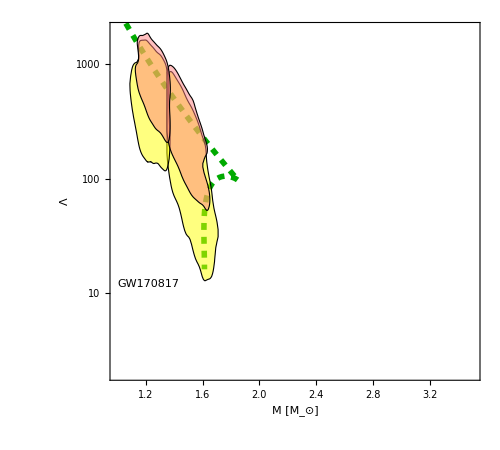

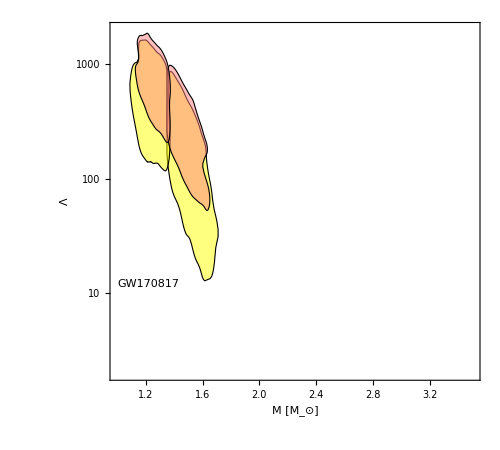

-Graphics-

TW/pickFIX_PTwidth

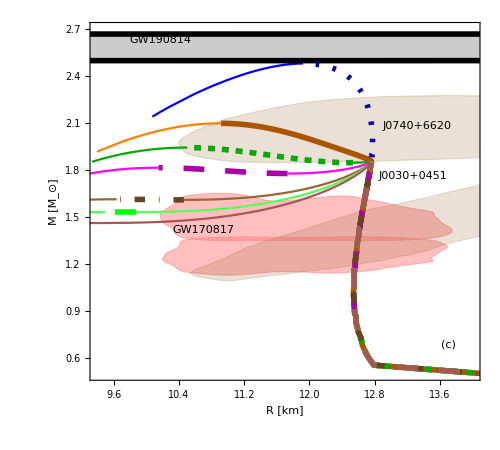
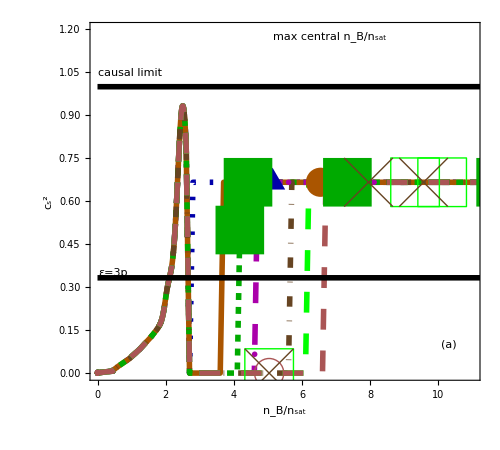
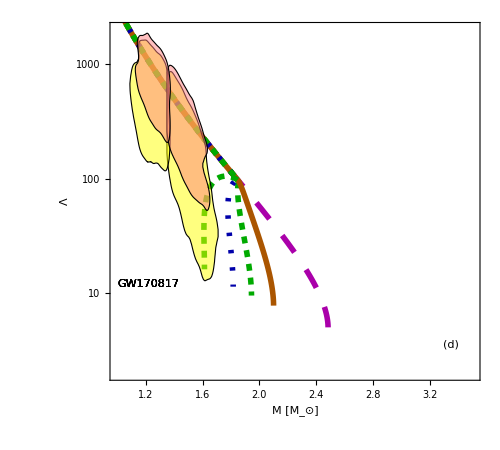
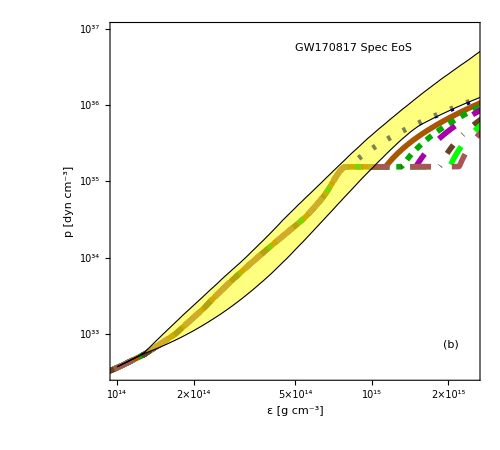

```mathematica
TWplots2[]
```

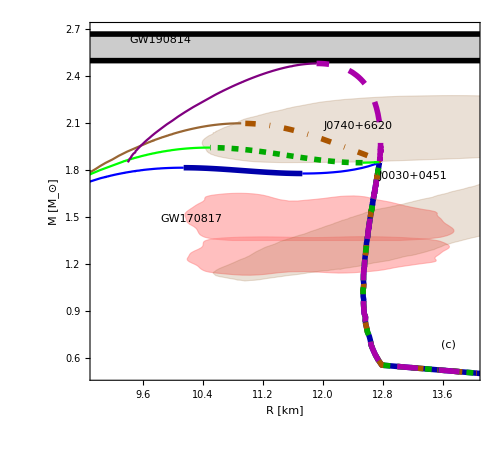
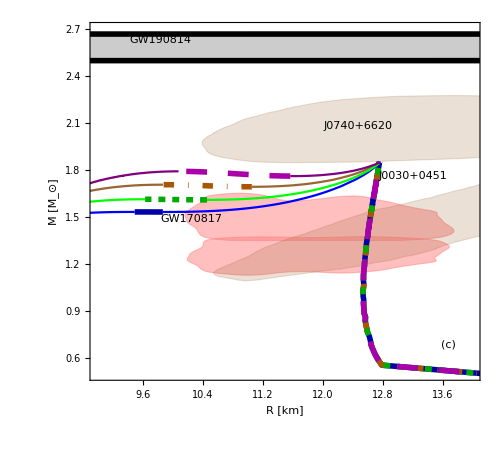

### low twins

```mathematica
lamPlot[name_,eosNuM_,sty_]:=Module[{in,inorg,out,split},
inorg=Import[StringJoin["output_files/",name,"/eos",ToString[eosNuM],"_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"]];

split= Select[Split[inorg,UnsameQ[#,{}]&],UnsameQ[#,{{}}]&]//.{}->Sequence[];

in=Table[split[[i]][[All,{3,6}]],{i,Length[split]}];
(*[[All,{3,6}]]*)
out=Show[{lamERR,ListLogPlot[in,Joined->True,PlotStyle->MyStyle[[sty]]],txt["GW170817",0.02,0.27]}];

Return[out];
]
```

```mathematica
MRsOUT=ListLinePlot[mrsly[[All,1;;2]],PlotStyle->MyStyle[[1]],PlotRange->All];
```

```mathematica
in1[n_]:=Import[StringJoin["output_files/TW/Blat_repeat/mr",ToString[n],".dat"]]
in2[n_]:=Import[StringJoin["output_files/TW/Blat_repeat2/mr",ToString[n],".dat"]]
in3[n_]:=Import[StringJoin["output_files/TW/low_n_peak1st/mr",ToString[n],".dat"]]
```

```mathematica
tcon[list_]:=Table[{list[[i,1]]/nsat,list[[i,4]]},{i,Length[list]}];
```

```mathematica
ein1[n_]:=tcon[Import[StringJoin["output_files/TW/Blat_repeat/eos",ToString[n],".dat"]]]
ein2[n_]:=tcon[Import[StringJoin["output_files/TW/Blat_repeat2/eos",ToString[n],".dat"]]]
ein3[n_]:=tcon[Import[StringJoin["output_files/TW/low_n_peak1st/eos",ToString[n],".dat"]]]
```

```mathematica
ein1b[n_]:=Import[StringJoin["output_files/TW/Blat_repeat/eos",ToString[n],".dat"]]
ein2b[n_]:=Import[StringJoin["output_files/TW/Blat_repeat2/eos",ToString[n],".dat"]]
ein3b[n_]:=Import[StringJoin["output_files/TW/low_n_peak1st/eos",ToString[n],".dat"]]
```

```mathematica
findbreak[eos_,mr_]:=Module[{max,min,all,pos,nbc,out,next,pos2,cslist,tout,mrout,lastI},
max=FindPeaks[mr[[All,2]]];
min=FindPeaks[-mr[[All,2]]];
all=Join[min,max];



pos=Sort[all[[All,1]]];


lastI=Length[mr[[1]]];

nbc=mr[[pos,lastI]];

Print[nbc];
mrout=If[Length[pos]≤3,notwinMR[pos,mr],twinMR[pos,mr]];


next=Flatten[Table[Nearest[eos[[All,1]],nsat*nbc[[i]]],{i,Length[nbc]}],1]; (*finds nearest nB from central density in EOS table*)
Print[next];
pos2=Flatten[Table[Position[eos[[All,1]],next[[i]]],{i,Length[next]}]]; (*locates position in EOS table*)

cslist=Delete[eos[[pos2]],1]; (*spits out EOS info at breaking points *)
Print[{pos2,cslist}];
tout=Table[Flatten[{cslist[[i,1]]/nsat,cslist[[i,4]]}],{i,Length[cslist]}]; (*renormalized to nB/nsat*)


Return[{tout,mrout}];
]
```

first

2nd

lasst

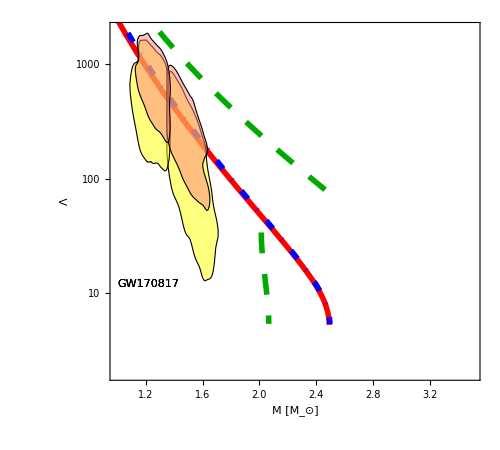

done

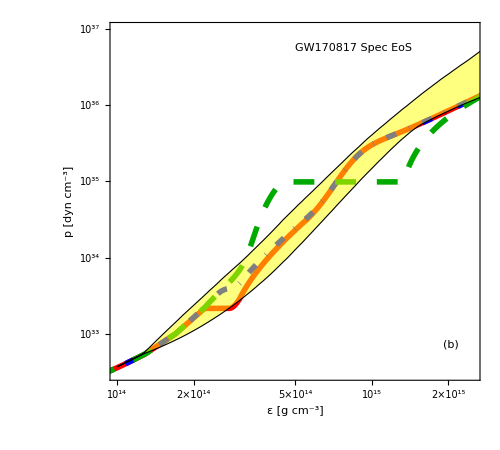

{0.229476,5.03343}

{0.0423733,0.8056}

{{66,918},{{0.8056,457.805,1021.34,0.694277,1836.08}}}

{0.229476,5.01047}

{0.0423733,0.8016}

{{66,913},{{0.8016,457.389,1020.97,0.690631,1844.26}}}

{0.712627,2.26371,5.10743,7.04241}

{0.128,0.3624,0.8168,1.1264}

{{71,364,932,1319},{{0.3624,61.649,392.39,0.0001,1252.87},{0.8168,300.658,987.924,1.,1577.6},{1.1264,880.66,1567.93,1.,2173.82}}}

{0.229476,5.03343}

{0.0423733,0.8056}

{{66,918},{{0.8056,457.805,1021.34,0.694277,1836.08}}}

{0.229476,5.01047}

{0.0423733,0.8016}

{{66,913},{{0.8016,457.389,1020.97,0.690631,1844.26}}}

{0.712627,2.26371,5.10743,7.04241}

{0.128,0.3624,0.8168,1.1264}

{{71,364,932,1319},{{0.3624,61.649,392.39,0.0001,1252.87},{0.8168,300.658,987.924,1.,1577.6},{1.1264,880.66,1567.93,1.,2173.82}}}

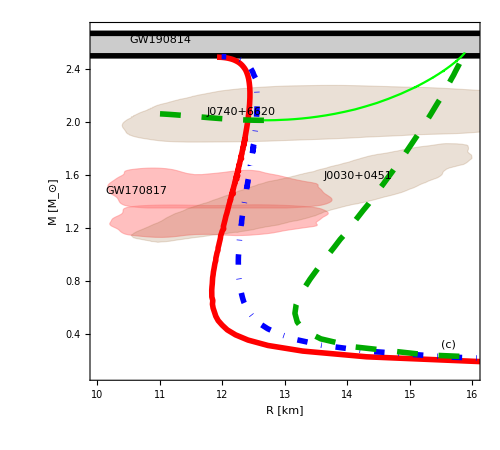

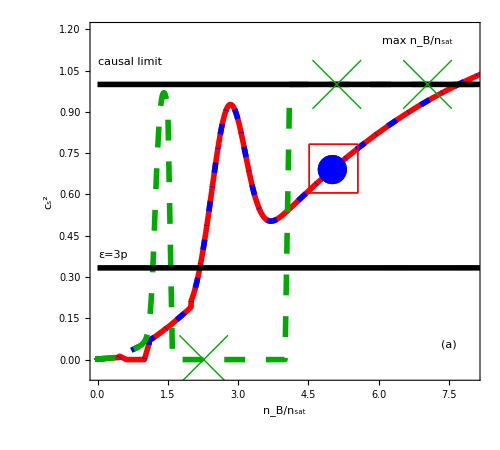

```mathematica
tab1=Table[in1[i],{i,4}];
tab2=Table[in2[i],{i,4}];
tab3=Table[in3[i],{i,4}];
mrall=Join[tab1,tab2,tab3];
Print["first"];
tab1=Table[in1[i][[All,1;;2]],{i,4}];
tab2=Table[in2[i][[All,1;;2]],{i,4}];
tab3=Table[in3[i][[All,1;;2]],{i,4}];
taball=Join[tab1,tab2,tab3];
Print["2nd"];
etab1=Table[ein1[i],{i,4}];
etab2=Table[ein2[i],{i,4}];
etab3=Table[ein3[i],{i,4}];
etaball=Join[etab1,etab2,etab3];
Print["lasst"];
etab1b=Table[ein1b[i],{i,4}];
etab2b=Table[ein2b[i],{i,4}];
etab3b=Table[ein3b[i],{i,4}];
eosallB=Join[etab1b,etab2b,etab3b][[{1,3,10}]];

lamBLAT=Show[{lamPlot["TW/Blat_repeat",1,2],lamPlot["TW/Blat_repeat",3,8],lamPlot["TW/low_n_peak1st",2,11]}]


Print["done"];

sub[eossub_]:=Table[{gcm3toMeVfm3*eossub[[i,3]],1.6022*10^33*eossub[[i,2]]},{i,Length[eossub]}];
eosoutB=Table[sub[eosallB[[j]]],{j,3}];

p1=Show[{LIGO,ListLogLogPlot[eosoutB,PlotRange->{{10^14,2.5*10^15},{10^32,10^37}},AspectRatio->0.9,PlotStyle->MyStyle[[{2,8,11}]],FrameLabel->{Style["ε [g cm^-3]",20],Style["p [dyn cm^-3]",20]},ImageSize->500,Frame->True,Joined->True,LabelStyle->Directive[20]],txt["GW170817 Spec EoS",0.5,0.93],txt["(b)",0.9,0.1]}]
mrlin={findbreak[eosallB[[1]],mrall[[1]] ][[2]],findbreak[eosallB[[2]],mrall[[3]] ][[2]],findbreak[eosallB[[3]],mrall[[10]] ][[2]]};
mrlina1=ListLinePlot[mrlin[[1]],PlotStyle->{MyStyle[[2 ]],Red}];
mrlina2=ListLinePlot[mrlin[[2]],PlotStyle->{MyStyle[[8 ]],Blue}];
mrlina3=ListLinePlot[mrlin[[3]],PlotStyle->{MyStyle[[11  ]],Green},PlotRange->All];

mark=ListPlot[{findbreak[eosallB[[1]],mrall[[1]] ][[1]],findbreak[eosallB[[2]],mrall[[3]] ][[1]],findbreak[eosallB[[3]],mrall[[10]] ][[1]]} ,PlotMarkers->{{"□",Offset[50]},{"●",Offset[30]},{"×",Offset[50]},{"▲",Offset[30]}},PlotStyle->MyStyle[[{2,8,11}]]];

(*mark=ListPlot[cpend,PlotMarkers->{{"□",Offset[50]},{"●",Offset[30]},{"×",Offset[50]},{"▲",Offset[30]}},PlotStyle->MyStyle2[[klist]]];*)
lines=Plot[{2.5+0.00001x,2.67+0.00001x},{x,0,30},PlotStyle->MyStyle[[{1,1,3,4,7}]],Filling->{1->{2}}];
mrBLAT=Show[{ListLinePlot[{0,0},PlotStyle->MyStyle[[{2,8,11}]],AspectRatio->0.9,PlotRange->{{10,16},{0.1,2.7}},FrameLabel->{Style["R [km]",20],Style["M [M_⊙]",20]},Joined->True,ImageSize->500,Frame->True,LabelStyle->Directive[20]],Ligoplot,lines,mrlina1,mrlina2,mrlina3,txt["GW170817",0.04,0.53],txt["J0030+0451",0.6,0.57],txt["J0740+6620",0.3,0.75],txt["GW190814",0.1,0.95],txt["(c)",0.9,0.1]}]
lines=Plot[{1/3+0.00001x,1+0.00001x},{x,0,25},PlotStyle->MyStyle[[{1,1}]]];
csBLAT=Show[{ListPlot[etaball[[{1,3,10}]],PlotStyle->MyStyle[[{2,8,11}]],Joined->True,PlotRange->{{0,8},{-0.05,1.2}},AspectRatio->0.9,FrameLabel->{Style["n_B/n_sat",20],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]],lines,txt["ε=3p",0.02,0.35],txt["causal limit",0.02,0.89],txt["max n_B/n_sat",0.75,0.95],mark,txt["(a)",0.9,0.1]}]
Export[StringJoin["output_files/TW/Blat_mrplot.pdf"],mrBLAT];
Export[StringJoin["output_files/TW/Blat_stupidunits.pdf"],p1];
Export[StringJoin["output_files/TW/Blat_csplot.pdf"],csBLAT];
Export[StringJoin["output_files/TW/Blat_LAMplot.pdf"],lamBLAT];
```

### Causal Limit and large Max Mass

#### functions

```mathematica
pMmax[mr_]:=pcen[[ Length[mr]]];
nBfind[eossub_]:=Interpolation[Table[{eossub[[i,2]],eossub[[i,1]]},{i,Length[eossub]}]];
nBmax[mr_,eos_]:=Module[{pM,fun,mc},
mc=mcuthi[mr];
Print[mc[[Length[mc]]]];
pM=mc[[ Length[mc],4]];

fun=nBfind[eos];
Return[fun[pM]];
]
cout[cstab_,nb_]:=Module[{int},

int=Interpolation[cstab,InterpolationOrder->1];


Return[{{nb,int[nb]}}];
]
cspoint[dat_,nblist_]:=Module[{tab,out},
tab=Delete[dat,1];

out=cout[tab,nblist];
Return[out];
]
csprint1[eos_]:=Table[{eos[[i,1]]/nsat,eos[[i,4]]},{i,Length[eos]}]
```

```mathematica
cs1PT[eos_]:=Module[{tab,split,min,max},
tab=Select[Table[{eos[[i,1]]/nsat,eos[[i,4]]},{i,Length[eos]}],#[[1]]>2&&#[[2]]<0.01&][[All,1]];
split=Split[tab,#2-#1<0.1&];
min=Table[Min[split[[i]]],{i,Length[split]}];
max=Table[Max[split[[i]]],{i,Length[split]}];


Return[{min,max}];
]
```

```mathematica
ptmark[mr_,min_,max_]:=Module[{mrl,mrl2,out,mrlmid},


mrl=Select[Flatten[Table[{mr[[i,1]],mr[[i,2]],If[min[[j]]> mr[[i-1,5]]&& max[[j]]≤ mr[[i,5]],1,0]},{i,2,Length[mr]},{j,Length[min]}],1],#[[3]]==1&][[All,1;;2]];

mrl2=Select[Flatten[Table[{mr[[i,1]],mr[[i,2]],If[min[[j]]> mr[[i,5]]&& max[[j]]≤ mr[[i+1,5]],1,0]},{i,1,Length[mr]-1},{j,Length[min]}],1],#[[3]]==1&][[All,1;;2]];
mrlmid=Flatten[Table[Select[mr,min[[x]]≤ #[[5]]<=max[[x]]&],{x,Length[min]}],1][[All,1;;2]];

out=Join[mrl2,mrl,mrlmid];

Return[out];
]
```

```mathematica
find0[eos_,mr_,cor_,ngau_]:=Module[{out,csint,mrs,pt,cs0,o2,tab,pts,dots,res,max,pos,res2,nBlist,endpoints},

cs0=cs1PT[eos];
pt=ptmark[mr,cs0[[1]],cs0[[2]]];

csint=Interpolation[Table[{eos[[i,1]]/nsat,eos[[i,4]]},{i,Length[eos]}],InterpolationOrder->1];
(*Print[Plot[csint[x],{x,0.1,10},FrameLabel->{Style["n_B/n_sat",20],Style["c_s^2",20]},PlotStyle->MyStyle,ImageSize->500,Frame->True,LabelStyle->Directive[20],PlotRange->{{0,10},{0,1}}]];
Print[ListPlot[mr[[1;;300,{5,2}]],PlotMarkers->Automatic,PlotRange->{{0,10},{0.5,2.5}},PlotStyle->MyStyle,FrameLabel->{Style["n_B/n_sat",20],Style["M",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]]];
Print[ListPlot[mr[[1;;300,{5,1}]],PlotMarkers->Automatic,PlotRange->{{0,10},{8,15}},PlotStyle->MyStyle,FrameLabel->{Style["n_B/n_sat",20],Style["R",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]]];*)
mrs=Table[{mr[[i,1]],mr[[i,2]],0},{i,Length[mr]}];
res=GaussianFilter[mrs[[All,1]],ngau];
max=Max[mrs[[All,2]]];
pos=Position[mrs[[All,2]],max][[1,1]];

res2=Table[{res[[i]],mrs[[i,2]]},{i,pos}];

nBlist=nBmax[mr,eos]/nsat;


endpoints=cspoint[csprint1[eos],nBlist];
Print[endpoints];


(*Print[ListPlot[{res2,mrs[[1;;200,1;;2]]},PlotStyle->MyStyle]];*)
(*Print[ListPlot[mrs[[1;;300,{2,3}]],Joined->True,PlotRange->All,FrameLabel->{Style["M",20],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]]];*)
out=ListLinePlot[res2,PlotRange->{{8,20},{0.5,4}},PlotStyle->MyStyle[[cor]],FrameLabel->{Style["R",20],Style["M",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]];

tab=Table[{eos[[i,1]]/nsat,eos[[i,4]]},{i,Length[eos]}];




o2=ListLinePlot[tab,PlotRange->{{0,5},{0,1}},PlotStyle->MyStyle[[cor]],FrameLabel->{Style["n_B/n_sat",20],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]];

Return[{out,o2,endpoints}];
]
```

```mathematica
convHung[mr_,eos_]:=Module[{pe,tab},

pe=Interpolation[eos[[All,{3,2}]],InterpolationOrder->1];

tab=Table[{mr[[i,2]],mr[[i,3]],mr[[i,1]],pe[mr[[i,1]]],mr[[i,4]],mr[[i,5]],mr[[i,6]]},{i,Length[mr]}];

Return[tab];
]
```

```mathematica
convHung2[mr_,eos_]:=Module[{pe,tab},

pe=Interpolation[eos[[All,{3,2}]],InterpolationOrder->1];

tab=Table[{mr[[i,2]],mr[[i,3]],mr[[i,1]],pe[mr[[i,1]]],0,0,0},{i,Length[mr]}];

Return[tab];
]
```

#### 3msun

```mathematica
lines=Plot[{2.5+0.00001x,2.67+0.00001x},{x,0,30},PlotStyle->MyStyle[[{1,1,3,4,7}]],Filling->{1->{2}}];
lines2=Plot[{2.91-0.08+0.00001x,2.91+0.08+0.00001x},{x,0,30},PlotStyle->MyStyle[[{1,1,3,4,7}]],Filling->{1->{2}}];
```

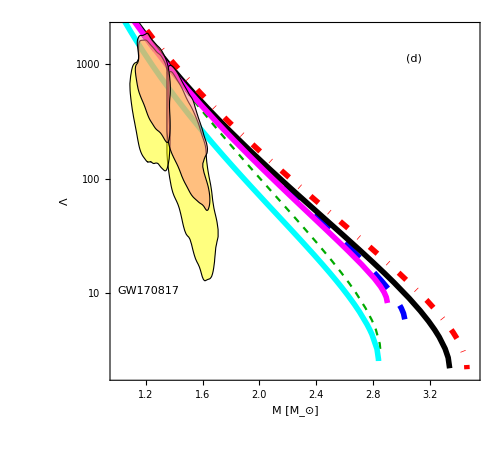

~/Dropbox/neutronStars/TOV_public/final_plots/3Msun_LAM.pdf

```mathematica
a0=Import["output_files/peaklocation/eos1_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"][[All,{3,6}]];
a1=Import["output_files/endpoint_maxfull/eos2_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"][[All,{3,6}]];
a2=Import["output_files/endpoint_maxfull/eos3_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"][[All,{3,6}]];
a3=Import["output_files/slanted/eos1_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"][[All,{3,6}]];
a4=Import["output_files/endpoint/eos4_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"][[All,{3,6}]];
a5=Import["output_files/2bumpsfat/eos1_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"][[All,{3,6}]];
out=Show[{lamERR,ListLogPlot[{a0,a1,a2,a3,a4,a5},Joined->True,PlotStyle->MyStyle[[{7,1,4,13,14,18}]]],txt["GW170817",0.02,0.25],txt["(d)",0.8,0.9]}]
(*Export["output_files/final_plots/3Msun_LAM.pdf",out]*)
```

{14.3143,3.02431,694.376,278.955,306.913,670.995}

{{3.47344,0.351276}}

{14.3949,3.33608,673.011,446.327}

{{3.22811,0.999}}

{14.7825,3.45674,668.377,457.485}

{{3.13123,0.999}}

{12.9217,2.85074,887.939,524.434}

{{4.20026,0.885886}}

{12.557,2.83651,923.966,580.225}

{{4.36737,0.93}}

{14.2112,2.89905,706.079,245.48}

{{3.57912,0.333333}}

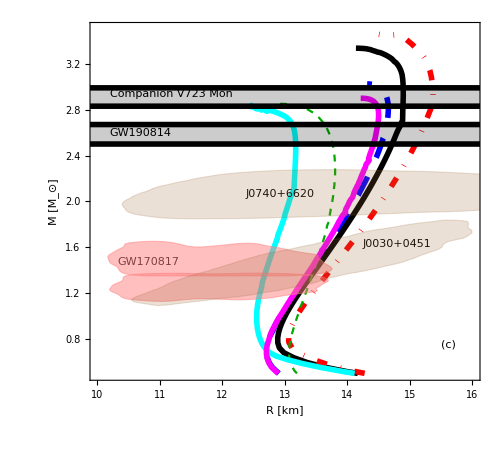

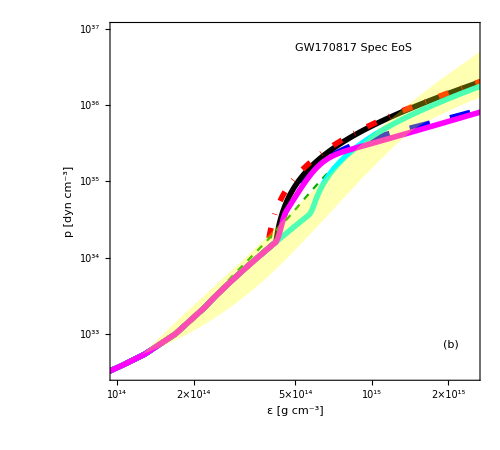

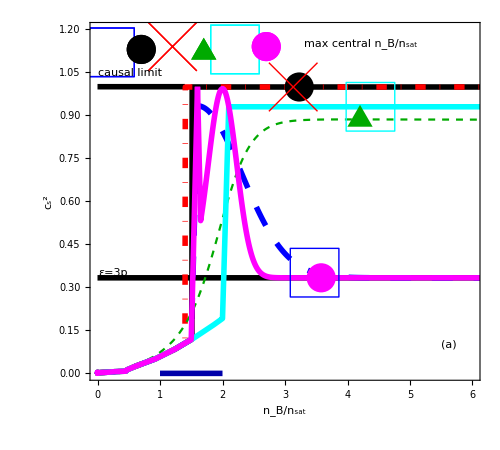

~/Dropbox/neutronStars/TOV_public/final_plots/3Msun.pdf

~/Dropbox/neutronStars/TOV_public/final_plots/3Msun_stupidunits.pdf

~/Dropbox/neutronStars/TOV_public/final_plots/3Msun_cs2.pdf

```mathematica
ain=Import["output_files/peaklocation/mr1.dat"];
bin1=Import["output_files/peaklocation/eos1.dat"];
cor=7;
hyb1=find0[bin1,ain,cor,1];
ain=Import["output_files/endpoint_maxfull/mr2.dat"];
bin2=Import["output_files/endpoint_maxfull/eos2.dat"];
cor=1;
hyb2=find0[bin2,ain,cor,11];
ain=Import["output_files/endpoint_maxfull/mr3.dat"];
bin3=Import["output_files/endpoint_maxfull/eos3.dat"];
cor=4;
hyb3=find0[bin3,ain,cor,11];
ain=Import["output_files/slanted/mr1.dat"];
bin4=Import["output_files/slanted/eos1.dat"];
cor=13;
hyb4=find0[bin4,ain,cor,1];
ain=Import["output_files/endpoint/mr4.dat"];
bin5=Import["output_files/endpoint/eos4.dat"];
cor=14;
hyb5=find0[bin5,ain,cor,11];
ain=Import["output_files/2bumpsfat/mr1.dat"];
bin6=Import["output_files/2bumpsfat/eos1.dat"];
cor=18;
hyb6=find0[bin6,ain,cor,1];
eosallB={bin1,bin2,bin3,bin4,bin5,bin6};



mark=ListPlot[{Join[hyb1[[3]],{{0.2,1.12}}],Join[hyb2[[3]],{{0.7,1.13}}],Join[hyb3[[3]],{{1.2,1.14}}],Join[hyb4[[3]],{{1.7,1.12}}],Join[hyb5[[3]],{{2.2,1.13}}],Join[hyb6[[3]],{{2.7,1.14}}]},PlotMarkers->{{"□",Offset[50]},{"●",Offset[30]},{"×",Offset[50]},{"▲",Offset[30]}},PlotStyle->MyStyle[[{7,1,4,13,14,18}]]];

lines=Plot[{2.5+0.00001x,2.67+0.00001x},{x,0,30},PlotStyle->MyStyle[[{1,1,3,4,7}]],Filling->{1->{2}}];
a=Show[{ListLinePlot[{0,-1},AspectRatio->0.9,PlotRange->{{10,16},{0.5,3.5}},PlotStyle->MyStyle3[[{2,3,4,5}]],FrameLabel->{Style["R [km]",20],Style["M [M_⊙]",20]},Joined->True,ImageSize->500,Frame->True,LabelStyle->Directive[20]],hyb1[[1]],hyb2[[1]],hyb3[[1]],hyb4[[1]],hyb5[[1]],hyb6[[1]],txt["GW190814",0.05,0.69],txt["Companion V723 Mon",0.05,0.8],txt["GW170817",0.07,0.33],txt["J0030+0451",0.7,0.38],txt["J0740+6620",0.4,0.52],lines,lines2,Ligoplot,txt["(c)",0.9,0.1]}]
lines=Show[{Plot[1/3+0.00001x,{x,0,10},PlotStyle->MyStyle[[{1,1}]]],Plot[1+0.00001x,{x,0,1.4},PlotStyle->MyStyle[[{1,1}]]]}];

sub[eossub_]:=Table[{gcm3toMeVfm3*eossub[[i,3]],1.6022*10^33*eossub[[i,2]]},{i,Length[eossub]}];
eosoutB=Table[sub[eosallB[[j]]],{j,Length[eosallB]}];

p1=Show[{LIGO,ListLogLogPlot[eosoutB,PlotRange->{{10^14,2.5*10^15},{10^32,10^37}},AspectRatio->0.9,PlotStyle->MyStyle[[{7,1,4,13,14,18}]],FrameLabel->{Style["ε [g cm^-3]",20],Style["p [dyn cm^-3]",20]},ImageSize->500,Frame->True,Joined->True,LabelStyle->Directive[20]],txt["GW170817 Spec EoS",0.5,0.93],txt["(b)",0.9,0.1]}]

b=Show[{ListLinePlot[{0,0},AspectRatio->0.9,PlotRange->{{0,6},{0,1.2}},PlotStyle->MyStyle2[[{2,3,4,5}]],FrameLabel->{Style["n_B/n_sat",20],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]],lines,txt["ε=3p",0.02,0.3],txt["causal limit",0.02,0.86],hyb1[[2]],hyb2[[2]],hyb3[[2]],hyb4[[2]],hyb5[[2]],hyb6[[2]],txt["max central n_B/n_sat",0.55,0.94],mark,txt["(a)",0.9,0.1]}]
Export["output_files/3Msun.pdf",a]
Export["output_files/3Msun_stupidunits.pdf",p1]
Export["output_files/3Msun_cs2.pdf",b]
```

#### crust

```mathematica
lines=Plot[{2.5+0.00001x,2.67+0.00001x},{x,0,30},PlotStyle->MyStyle[[{1,1,3,4,7}]],Filling->{1->{2}}];
lines2=Plot[{2.91-0.08+0.00001x,2.91+0.08+0.00001x},{x,0,30},PlotStyle->MyStyle[[{1,1,3,4,7}]],Filling->{1->{2}}];
```

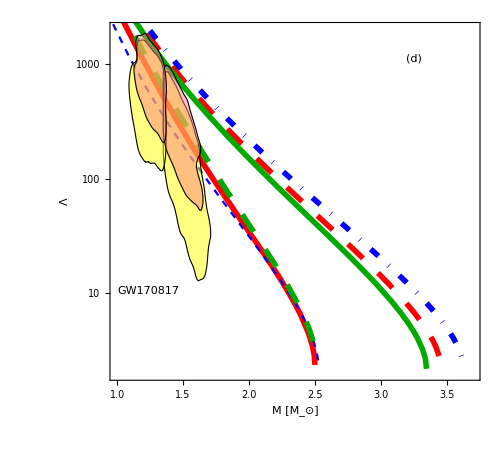

~/Dropbox/neutronStars/TOV_public/final_plots/crust_LAM.pdf

```mathematica
a0=Import["output_files/endpoint_maxfull/eos1_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"][[All,{3,6}]];
a1=Import["output_files/eos3_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"][[All,{3,6}]];
a2=Import["output_files/crust/QHC-125_eos_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"][[All,{3,6}]];
a3=Import["output_files/crust/QHC-275_eos_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"][[All,{3,6}]];
a4=Import["output_files/crust/SKA-150_eos_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"][[All,{3,6}]];
a5=Import["output_files/crust/SKA-300_eos_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"][[All,{3,6}]];
out=Show[{lamERRwide,ListLogPlot[{a0,a1,a2,a3,a4,a5},Joined->True,PlotStyle->MyStyle[[{2,3,8,9,10,11}]]],txt["GW170817",0.02,0.25],txt["(d)",0.8,0.9]}]
Export["output_files/final_plots/crust_LAM.pdf",out]
```

{11.2,2.50023,1205.63,792.231}

{{5.57198,0.999}}

{14.7825,3.45674,668.377,457.485}

{{3.13123,0.999}}

{15.4744,3.62966919182942799592,580,389.028,4.74674,1.33422,2.1686}

{{2.77881,1.}}

{11.0984,2.52839288505973457722,1180,781.836,4.7708,1.34793,2.29942}

{{5.52709,1.}}

{14.3836,3.3484635494841614533,680,455.125,4.75106,1.33671,2.192}

{{3.23585,1.}}

{11.2855,2.51098039380995388215,1180,766.319,4.81128,1.37179,2.53266}

{{5.45986,1.}}

-Graphics-

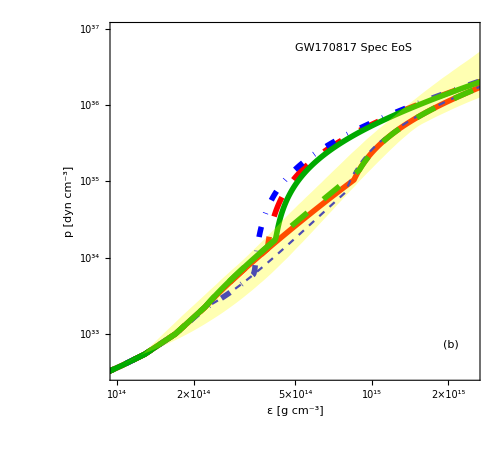

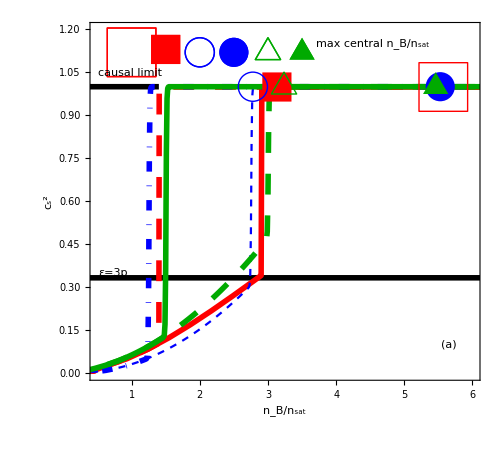

~/Dropbox/neutronStars/TOV_public/final_plots/crust_stupidunits.pdf

~/Dropbox/neutronStars/TOV_public/final_plots/crust.pdf

~/Dropbox/neutronStars/TOV_public/final_plots/crust_cs2.pdf

```mathematica
ain=Import["output_files/endpoint_maxfull/mr1.dat"];
bin1=Import["output_files/endpoint_maxfull/eos1.dat"];
cor=2;
hyb1=find0[bin1,ain,cor,11];
ain=Import["output_files/endpoint_maxfull/mr3.dat"];
bin2=Import["output_files/endpoint_maxfull/eos3.dat"];
cor=3;
hyb2=find0[bin2,ain,cor,11];
bin3=Import["output_files/crust/QHC-125_eos.dat"];
ain=convHung[Import["output_files/crust/QHC-125_eos_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"],bin3];
cor=8;
hyb3=find0[bin3,ain,cor,1];
bin4=Import["output_files/crust/QHC-275_eos.dat"];
ain=convHung[Import["output_files/crust/QHC-275_eos_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"],bin4];
cor=9;
hyb4=find0[bin4,ain,cor,1];
bin5=Import["output_files/crust/SKA-150_eos.dat"];
ain=convHung[Import["output_files/crust/SKA-150_eos_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"],bin5];
cor=10;
hyb5=find0[bin5,ain,cor,1];
bin6=Import["output_files/crust/SKA-300_eos.dat"];
ain=convHung[Import["output_files/crust/SKA-300_eos_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"],bin6];
cor=11;
hyb6=find0[bin6,ain,cor,1];
eosallB={bin1,bin2,bin3,bin4,bin5,bin6};


mark=ListPlot[{Join[hyb1[[3]],{{1,1.12}}],Join[hyb2[[3]],{{1.5,1.13}}],Join[hyb3[[3]],{{2,1.12}}],Join[hyb4[[3]],{{2.5,1.12}}],Join[hyb5[[3]],{{3,1.12}}],Join[hyb6[[3]],{{3.5,1.12}}]},PlotMarkers->{{"□",Offset[50]},{"■",Offset[30]},{"○",Offset[30]},{"●",Offset[30]},{"△",Offset[30]},{"▲",Offset[30]}},PlotStyle->MyStyle[[{2,3,8,9,10,11}]]];

lines=Plot[{2.5+0.00001x,2.67+0.00001x},{x,0,30},PlotStyle->MyStyle[[{1,1,3,4,7}]],Filling->{1->{2}}];
a=Show[{ListLinePlot[{0,-1},AspectRatio->0.9,PlotRange->{{10,16.5},{0.5,3.7}},PlotStyle->MyStyle3[[{2,3,4,5}]],FrameLabel->{Style["R [km]",20],Style["M [M_⊙]",20]},Joined->True,ImageSize->500,Frame->True,LabelStyle->Directive[20]],lines,lines2,sLigoplot,hyb1[[1]],hyb2[[1]],hyb3[[1]],hyb4[[1]],hyb5[[1]],hyb6[[1]],txt["GW190814",0.05,0.65],txt["Companion V723 Mon",0.05,0.75],txt["GW170817",0.04,0.31],txt["J0740+6620",0.4,0.49],leg3[{"Min QHC19","Min SLy","Min SKa"},{0.0,0.07,0.08}+0.02,{0.92,0.84,0.77}+0.04,MyStyle[[{9,2,11}]]] ,leg3[{"Max QHC19","Max SLy","Max SKa"},{0.0,0.07,0.08}+0.33,{0.92,0.84,0.77}+0.04,MyStyle[[{8,3,10}]]],txt["(c)",0.9,0.10]}]
lines=Show[{Plot[1/3+0.00001x,{x,0,10},PlotStyle->MyStyle[[{1,1}]]],Plot[1+0.00001x,{x,0,1.4},PlotStyle->MyStyle[[{1,1}]]]}];

sub[eossub_]:=Table[{gcm3toMeVfm3*eossub[[i,3]],1.6022*10^33*eossub[[i,2]]},{i,Length[eossub]}];
eosoutB=Table[sub[eosallB[[j]]],{j,Length[eosallB]}];

p1=Show[{LIGO,ListLogLogPlot[eosoutB,PlotRange->{{10^14,2.5*10^15},{10^32,10^37}},AspectRatio->0.9,PlotStyle->MyStyle[[{2,3,8,9,10,11}]],FrameLabel->{Style["ε [g cm^-3]",20],Style["p [dyn cm^-3]",20]},ImageSize->500,Frame->True,Joined->True,LabelStyle->Directive[20]],txt["GW170817 Spec EoS",0.5,0.93],txt["(b)",0.9,0.1]}]

b=Show[{ListLinePlot[{0,-1},AspectRatio->0.9,PlotRange->{{0.5,6},{0,1.2}},PlotStyle->MyStyle3[[{2,3,4,5}]],FrameLabel->{Style["n_B/n_sat",20],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]],lines,txt["ε=3p",0.02,0.3],txt["causal limit",0.02,0.86],hyb1[[2]],hyb2[[2]],hyb3[[2]],hyb4[[2]],hyb5[[2]],hyb6[[2]],txt["max central n_B/n_sat",0.58,0.94],mark,txt["(a)",0.9,0.1]}]

Export["output_files/crust_stupidunits.pdf",p1]
Export["output_files/crust.pdf",a]
Export["output_files/crust_cs2.pdf",b]
```

```mathematica
(3.64-3.35)/3.64 100
```

7.96703

```mathematica
(14.36-15.4)/15.4*100
```

-6.75325

#### spec vs uni

{11.2,2.50023,1205.63,792.231}

{{5.57198,0.999}}

{14.3949,3.33608,673.011,446.327}

{{3.22811,0.999}}

{14.7825,3.45674,668.377,457.485}

{{3.13123,0.999}}

-Graphics-

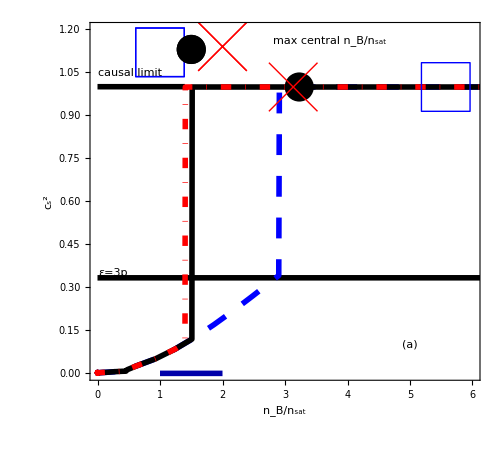

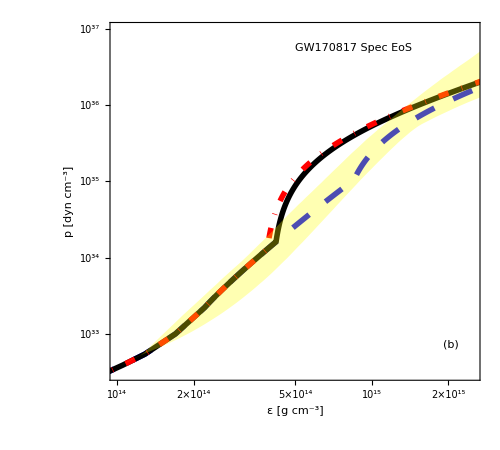

~/Dropbox/neutronStars/TOV_public/final_plots/EX.pdf

~/Dropbox/neutronStars/TOV_public/final_plots/EX_cs2.pdf

~/Dropbox/neutronStars/TOV_public/final_plots/EX_stupidunits.pdf

```mathematica
ain=Import["output_files/endpoint_maxfull/mr1.dat"];
bin1=Import["output_files/endpoint_maxfull/eos1.dat"];
cor=7;
hyb1=find0[bin1,ain,cor,11];
ain=Import["output_files/endpoint_maxfull/mr2.dat"];
bin2=Import["output_files/endpoint_maxfull/eos2.dat"];
cor=1;
hyb2=find0[bin2,ain,cor,11];
ain=Import["output_files/endpoint_maxfull/mr3.dat"];
bin3=Import["output_files/endpoint_maxfull/eos3.dat"];
cor=4;
hyb3=find0[bin3,ain,cor,11];
(*ain=Import["~/Dropbox/neutronStars/TOV_public/endpoint_maxfull/mr4.dat"];
bin=Import["~/Dropbox/neutronStars/TOV_public/endpoint_maxfull/eos4.dat"];
cor=13;
hyb4=find0[bin,ain,cor];*)
mark=ListPlot[{Join[hyb1[[3]],{{1,1.12}}],Join[hyb2[[3]],{{1.5,1.13}}],Join[hyb3[[3]],{{2,1.14}}]},PlotMarkers->{{"□",Offset[50]},{"●",Offset[30]},{"×",Offset[50]},{"▲",Offset[30]}},PlotStyle->MyStyle[[{7,1,4}]]];
eosallB={bin1,bin2,bin3};

lines=Plot[{2.5+0.00001x,2.67+0.00001x},{x,0,30},PlotStyle->MyStyle[[{1,1,3,4,7}]],Filling->{1->{2}}];
a=Show[{ListLinePlot[{0,0},AspectRatio->0.9,PlotRange->{{10,16},{0.5,3.5}},PlotStyle->MyStyle3[[{2,3,4,5}]],FrameLabel->{Style["R [km]",20],Style["M [M_⊙]",20]},Joined->True,ImageSize->500,Frame->True,LabelStyle->Directive[20]],hyb1[[1]],hyb2[[1]],hyb3[[1]],sLigoplot,txt["GW190814",0.05,0.69],leg3[{"Min","Max universal","Max spectral"},{0.0,0.07,0.08}+0.65,{0.92,0.84,0.75}-0.65,MyStyle[[{7,1,4,13}]]],txt["Companion V723 Mon",0.05,0.8],txt["GW170817",0.07,0.33],txt["J0740+6620",0.4,0.52],lines,lines2,txt["(c)",0.1,0.1]}]
lines=Show[{Plot[1/3+0.00001x,{x,0,10},PlotStyle->MyStyle[[{1,1}]]],Plot[1+0.00001x,{x,0,1.4},PlotStyle->MyStyle[[{1,1}]]]}];
b=Show[{ListLinePlot[{0,0},AspectRatio->0.9,PlotRange->{{0,6},{0,1.2}},PlotStyle->MyStyle2[[{2,3,4,5}]],FrameLabel->{Style["n_B/n_sat",20],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]],lines,txt["ε=3p",0.02,0.3],txt["causal limit",0.02,0.86],hyb1[[2]],hyb2[[2]],hyb3[[2]],txt["max central n_B/n_sat",0.47,0.95],mark,txt["(a)",0.8,0.1]}]

sub[eossub_]:=Table[{gcm3toMeVfm3*eossub[[i,3]],1.6022*10^33*eossub[[i,2]]},{i,Length[eossub]}];
eosoutB=Table[sub[eosallB[[j]]],{j,Length[eosallB]}];

p1=Show[{LIGO,ListLogLogPlot[eosoutB,PlotRange->{{10^14,2.5*10^15},{10^32,10^37}},AspectRatio->0.9,PlotStyle->MyStyle[[{7,1,4}]],FrameLabel->{Style["ε [g cm^-3]",20],Style["p [dyn cm^-3]",20]},ImageSize->500,Frame->True,Joined->True,LabelStyle->Directive[20]],txt["GW170817 Spec EoS",0.5,0.93],txt["(b)",0.9,0.1]}]

Export["output_files/EX.pdf",a]
Export["output_files/EX_cs2.pdf",b]
Export["output_files/EX_stupidunits.pdf",p1]
```

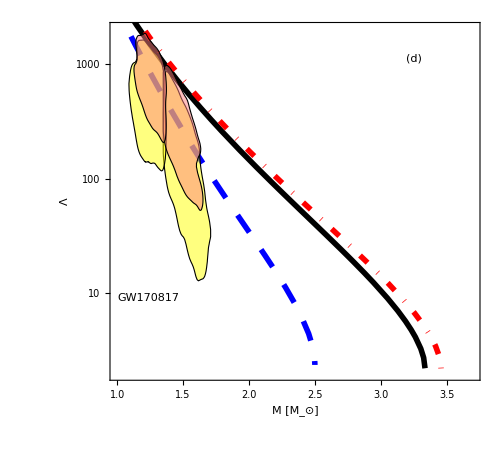

~/Dropbox/neutronStars/TOV_public/final_plots/EX_LAM.pdf

```mathematica
a0=Import["output_files/endpoint_maxfull/eos1_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"][[All,{3,6}]];
a1=Import["output_files/endpoint_maxfull/eos2_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"][[All,{3,6}]];
a2=Import["output_files/endpoint_maxfull/eos3_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"][[All,{3,6}]];
out=Show[{lamERRwide,ListLogPlot[{a0,a1,a2},Joined->True,PlotStyle->MyStyle[[{7,1,4,13}]]],txt["GW170817",0.02,0.23],txt["(d)",0.8,0.9]}]
Export["output_files/final_plots/EX_LAM.pdf",out]
```

### I - LOVE - Q Summary plot

#### functions

```mathematica
fname={"2bumpsfat","endpoint","adjustedwidth","peaklocation"};
TWname={"TW/endpoint","TW/slantendpoint","TW/peakwidthFIXL","TW/hybs"};
```

```mathematica
allname=Join[fname,TWname];
```

```mathematica
skip[tab_]:=Select[tab,UnsameQ[#,{}]&]
```

```mathematica
set4[name_,n_,m_]:=Module[{},
out=Table[skip[Import[StringJoin["output_files/",name,"/eos",ToString[i],"_CntDens[MeV]_R[km]_M[Msun]_Ibar_Qbar_Love.dat"]]][[All,{n,m}]],{i,4}];
(*Print[name];*)
Return[out];
]
```

```mathematica
plotILove[]:=Module[{taball,plot},
taball=Flatten[Table[set4[allname[[i]],6,4],{i,Length[allname]}],1];
plot=ListLogLogPlot[taball,AspectRatio->0.9,FrameLabel->{Style["Λ",20],Style["I",20]},ImageSize->500,RotateLabel->False,Frame->True,PlotMarkers->Automatic,LabelStyle->Directive[20]];
Export["~/Dropbox/neutronStars/ILove.pdf",plot];
Return[plot];
]
plotLoveQ[]:=Module[{taball,plot},
taball=Flatten[Table[set4[allname[[i]],6,5],{i,Length[allname]}],1];
plot=ListLogLogPlot[taball,AspectRatio->0.9,FrameLabel->{Style["Λ",20],Style["Q",20]},ImageSize->500,RotateLabel->False,Frame->True,PlotMarkers->Automatic,LabelStyle->Directive[20]];
Export["Dropbox/neutronStars/LoveQ.pdf",plot];
Return[plot];
]
```

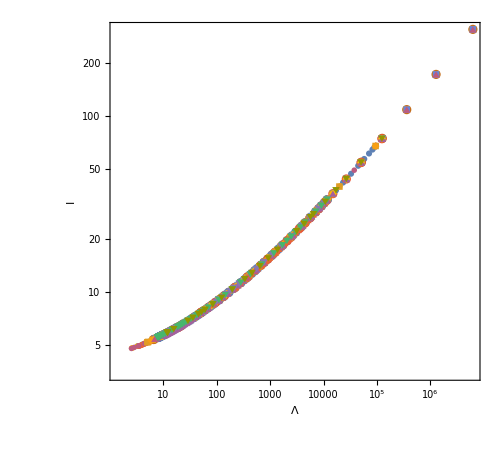
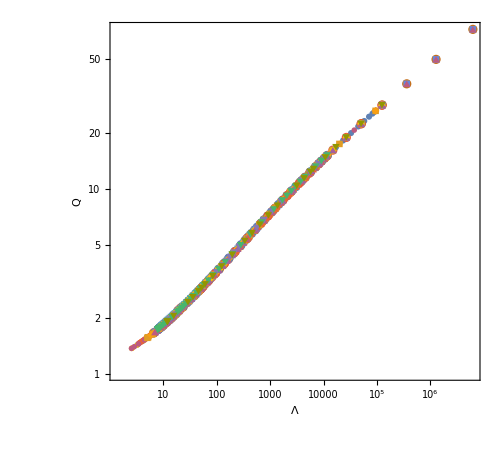

```mathematica
{plotILove[],plotLoveQ[]}
```

```mathematica
set4[allname[[1]],5,4][[1,1]]
set4[allname[[1]],6,4][[1,1]]
```

{26.3564,67.3748}

{94123.9,67.3748}

#### plot